# 第0章 绪论

## 目录

§0 .1 简介
§0 .2 初识Mathematica
§0 .3 输入和输出
§0 .4 文字处理和排版
§0 .5 获取帮助

## §0 .1 简介

1988 年6月 ， Mathematica 这一重要软件产品面世， 为计算机技术与科学、技术、 教育的有机结合及进一步的发展提出了新思路.

Mathematica 的目标非常简单:建立一个系统， 为各个领域各种水平的技术人员提供一个理想的工作助手.从许多方面来看， 数值计算 、图形处理、增添新函数是一个系统应该具有的最主要的功能.对一个文件管理和创新型的编程语言来说， 符号计算也是至关重要的.Mathematica 包含了所有这些功能.

软件特色
 1. mathematica可以访问广泛的wolfram知识库，其中包括数千个领域的最新实时数据；
2. 程序代码具明显的含义，类似英语的函数名称和一致的设计，wolfram语言易于阅读，编写和学习；
3. mathematica现在与云无缝集成 - 允许在独特而强大的混合云/桌面环境中实现共享，云计算等。
4. mathematica基于三十年的发展历程，擅长于所有技术计算领域 - 包括神经网络，机器学习，图像处理，几何，数据科学，可视化

课程简介
1.介绍软件的用户界面 ，简要说明软件的用法，输入输出，文档排版等内容。
2.介绍如何调用Mathematica的函数做初等数学、微积分、线性代数和微分方程中的计算题，验证数学公式的推导，演示函数和数据图形等。
3.按照计算机语言的结构，从简单的命令行输入到构建复杂的序包，学习过程编程和函数编程。

课程要求
1.安装Mathematica软件
2.按时上课
3.每周交作业包括书面作业和程序作业
4.期末总评成绩包括卷面50%+作业50%

## §0 .2 初识Mathematica

## §0 .3 输入和输出

### 1.输入希腊字母

使用 面板    特殊字符 或 全名输入

### 2.输入数学公式

幂函数 求和 连乘  微分 积分

### 3.输入运算函数

（1）自由格式输入

（2）“数学助手”输入

（3）完整函数语句输入

需要记住三条主要规则：
【1】Wolfram 语言指令以大写字母开头.
【2】函数参数用方括号[ ] 括起.
【3】列表，也用于存储定义域和范围，用花括号括起.
所有的 Wolfram 语言指令一般是完整的英文单词, 均以大写字母开头，如果指令名由多个单词组成，
例如 ListPlot, 则各个单词的首字母都要大写.指令名的单词之间没有空格.当然也有些例外，
如：N, GCD 等几个指令是为了简单起见而使用的缩写.

### 4.输入输出的格式

InputForm | 使用标准键盘上的字符能直接输人的格式
OutputForm | 使用标准键盘上恰当的字符，仅用于输出格式
StandardForm | 利用特殊字符和定位的输入输出格式
TraditionalForm | 使用传统数学符号的格式（主要用于输出）

```mathematica
Integrate[1/(1+x^4),x]//TraditionalForm
```

```mathematica
{Abs[x],ArcSin[x],BesselJ[0,x],Binomial[i,j]}//TraditionalForm
```

TeXForm[expr]可以将数学公式转化成适合LaTeX输入的格式，复制粘贴到自己的TeX文档中

```mathematica
TeXForm[%]
```

## §0 .4 文字处理和排版

### 1.笔记本的结构

笔记本是由单元构成，前面已经看到了输入单元（用来执行运算的指令，函数等），输出单元（执行的结果），此外还有一些加强笔记本可读性的文本单元,样式包括标题(Title),子标题(Subtitle),章标题（Section)、 小节标题 (Subsection)、 小节子标题(Subsubsection)、 文本和条目等

单元会根据层次结构自动分组.这个分组会通过笔记本右侧的括号显示.每个括号对应于一个单元，更大的、跨越性的括号对应于一组单元.单元括号可以通过双击来折叠或展开单元内容

### 2.添加文本单元

### 3.设定单元样式

### 4.编辑样式表

## §0 .5 获取帮助

1.通过帮助 菜单, 选择 Wolfram参考资料

2.使用指令时寻求帮助

3.与范例交互操作

4.网络资料：Wolfram 社区论坛： community.wolfram.com.
                         参考资料网站： reference.wolfram.com

# 第1章 Mathematica的基本量

## 1.1 数值

### 1.Mathematica 中建立了四种基本的数的类型.

Mathematica 中数的类型
"Integer" | "1234" | "任意长度的精确整数"
"Rational" | "1234/222" | "整数除整数的最简形式"
"Real" | "123.4" | "近似实数,具有任意指定的精度"
"Complex" | "12+34I" | "复数"
 
（1）	对整数或有理数进行四则运算，结果会给出精确值.
（2）	对实数进行四则运算，结果是具有指定精度的实数, 不指定时，给出6位有效数字，
（3）	如果使用复数， 应当注意当输入一个数如 123+0I.时， Mathematica 把它作为实数处理， 如果需要做复数运算，例如复数开根号，需要输入123+0.0I

```mathematica
Head[123+0I]
Head[123+0.0I]
```

### 2.不同形式之间的转换

(1)"N[x,n]" | "将转换为位精度的近似实数"
"Rationalize[x]" | "  给出的有理数近似值"
"Rationalize[x,dx]" | "给出的误差不超过的有理数近似值"

```mathematica
N[5/7,30]  
Rationalize[N[Pi]] 
 Rationalize[N[Pi],10^(-5)]
```

0.714285714285714285714285714286

3.14159

355/113

```mathematica
NumberQ[π]
```

```mathematica
Rationalize[N[Pi],0]
```

245850922/78256779

(2)
"IntegerPart[x]" | " X 的整数部分"
"FractionalPart[x]" | " X 的小数部分"
"Round[x]" | "最接近x的整数 "
"Floor[x]" | " 小于等于x 的最大整数"
"Ceiling[x]" | " 大于等于 X 的最小整数"

IntegrPart[x]和 FractionalPart[x]可以看作是提取小数点左边和右边的数字.Round[ x ]表示4舍5入的结果.Floor[x]和 Ceiling[x]常出现在计算一个具有非整数间隔的数列中有多少元素的事项中

```mathematica
Round[-3.1]
Round[2.6]
```

-3

3

```mathematica
Floor[-3.1]
Floor[2.6]
```

-4

2

(3)
"x+yI" | "复数" | "Conjugate[z]" | "z的共轭"
"Re[z]" | "实部" | "Im[z]" | "虚部"
"Abs[z]" | "模长" | "Arg[z]" | "辐角"

```mathematica
Re[12+3.0I]
```

12.

(4)角度与弧度转换

```mathematica
Sin[60 Degree]
```

(√3)/2

```mathematica
Sin[60 °]
```

Sin[60]

```mathematica
Sin[Pi/3]
```

(5)不同进制的转换
" b^^digits" | "b进制的数digits转为10进制"
"BaseForm[x,b]" | "10进制数 x 转为 b 进制数"
"IntegerDigits[n,b]" | "整数n在b进制下的数字列表，b缺省表示10进制"
"IntegerDigits[n,b,l]" | "左边补零使列表长度为l"
"RealDigits[n,b]" | "给出实数x在b进制下的数字列表及小数点左边位数，b缺省表示10进制 "

```mathematica
2^^100101
```

37

```mathematica
BaseForm[37, 2]
```

100101_2

```mathematica
16^^ff1faa00
```

4280265216

```mathematica
BaseForm[ N[Sqrt[2],30], 8]
```

1.324047463177167462204262766115467_8

```mathematica
RealDigits[123.456789012345678901234567]
```

{{1,2,3,4,5,6,7,8,9,0,1,2,3,4,5,6,7,8,9,0,1,2,3,4,5,6,7},3}

```mathematica
FromDigits[%]
```

123456789012345678901234567/1000000000000000000000000

```mathematica
IntegerDigits[56, 2,8]
```

{0,0,1,1,1,0,0,0}

### 3. 常用数值函数

(1) 
"Random[ ]" | "生成[0,1]中的一个伪随机数"
"Random[ Real,xmax ]
Random[ Real,{xmin ,xmax },l ]" | "生成[0,xmax]或[xmin,xmax] 中的一个伪随机数,
参数 l 是生成随机数的数字位数"
"Random[Complex]
Random[Complex,{zmin,zmax} ]" | "生成单位方形区域或zmin,zmax为对角顶点的矩形
区域中的一个伪随机数"
"Random[ Integer]" | "具有相同概率 的 0 或 1"
"Random[ Integer, {imin , imax} ]" | "生成 [xmin,xmax] 中的一个伪随机数"
"SeedRandom[ ]
SeedRandom[ s]" | "将伪随机数生成器的起点重设为时钟时刻或整数s "

```mathematica
Table[Random[ ],{5}]
```

{0.240591,0.140657,0.0854972,0.856496,0.35773}

```mathematica
Random[Real,{ 0,10},10]
```

7.337521872

```mathematica
Table[Random[ Integer, {100, 200} ] ,{8} ]
```

{109,110,145,139,198,118,183,140}

用法：(1)使用伪随机数的一个常见方法是进行数值假设检验.例如， 如果用户相信两个符号表达式在数学上是相等的.可以通过给符号参数插上"典型"数值的值.然后比较数值结果来进行检验。

(2)其它常见用法包括模拟随机过程， 概率空间的采样.
Mathematica 生成的伪随机数总是在指定范围上的均匀分布.

由 Random[ ]得到的序列在多数意义下并不是"真正随机的"， 尽管实际上它们应当是"足够随机的".如果用户想确定总是得到相同的伪随机数序列， 可以使用 SeedRandom[]给伪随机数一个起点.

```mathematica
SeedRandom[100];Table[Random[],{5}]
```

{0.185898,0.242848,0.20331,0.0515874,0.440317}

```mathematica
Table[Random[],{5}]
```

{0.239615,0.817663,0.23069,0.986929,0.262161}

```mathematica
SeedRandom[100];Table[Random[],{5}]
```

{0.185898,0.242848,0.20331,0.0515874,0.440317}

每调用一次 Random,伪随机数生成器的内部状态就被改变， 这意味着在辅助运算中调用 Random,将会影响主运算中 Random 返回的数.要避免这个问题， 可以在辅助运算之前保存 $StateRandom 的值，以后再恢复它.

```mathematica
Block[{$RandomState} ,{Random[ ],Random[ ]}]
 {Random[ ], Random[]}
```

{0.239615,0.817663}

{0.239615,0.817663}

(2)
" GCD[n1,n2,.85...],LCM[n1,n2,.85...]" | "-最大公约数，最小公倍数"
"Mod[k,n]" | "k/n 的余数"
"Quotient[k,n]" | "k/n 的商（整数部分）"

```mathematica
GCD[192, 456,91324]
```

4

```mathematica
LCM[192, 456,91324]
```

83287488

```mathematica
Mod[56473, 87,-90]
```

-77

```mathematica
Quotient[56473, 87]
```

(3)
" FactorInteger[n]" | "n 的素因子和相应指数的列表"
"Divisors[n]" | "整除n的整数列表"
"Prime[k]" | "第k个素数"
"PrimePi[x]" | "小于等于 x 的素数的个数"
"PrimeQ[n]" | "判断n是否为素数 "

```mathematica
FactorInteger[1200000]
```

{{2,7},{3,1},{5,5}}

```mathematica
Divisors[1200000]
```

{1,2,3,4,5,6,8,10,12,15,16,20,24,25,30,32,40,48,50,60,64,75,80,96,100,120,125,128,150,160,192,200,240,250,300,320,375,384,400,480,500,600,625,640,750,800,960,1000,1200,1250,1500,1600,1875,1920,2000,2400,2500,3000,3125,3200,3750,4000,4800,5000,6000,6250,7500,8000,9375,9600,10000,12000,12500,15000,16000,18750,20000,24000,25000,30000,37500,40000,48000,50000,60000,75000,80000,100000,120000,150000,200000,240000,300000,400000,600000,1200000}

```mathematica
PrimePi[234242423]
```

12862644

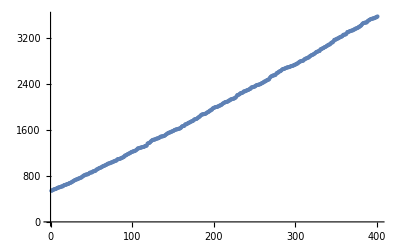

```mathematica
ListPlot[ Table[ Prime[n] ,{n, 100,500} ] ]
```

```mathematica
PrimeQ[207]
```

False

```mathematica
FactorInteger[207]
```

{{3,2},{23,1}}

## 1.2 字符串

1.字符串运算
 "StringJoin[{s1,s2,...]" | ".85将几个字符串连接在一起"
"StringLength[s]" | "给出一个串中的字符数"
"StringReverse[s]" | "颠倒串中字符的顺序"
"StringTake[s,n]" | "n>0时，由 s 的前 n 个字符形成字符串
n<0,取后面|n|个字符形成字符串"
"StringTake[s,{n}]" | "取出 s 中的第 n 个字符"
"StringTake[s,{n1,n2}]" | "取出 n1 到 n2 的字符"
"StringDrop[s,n]" | "删除前n个字符"
"StringDrop[s,{n1,n2}]" | "删除n1 到n2的字符"

```mathematica
alpha=".94ABCDEFGHIJKLMNOPQRSTUVWXYZ";
StringTake[alpha , 6]
  StringTake[alpha ,{ 6}]
  StringTake[alpha , -6] 
StringTake[alpha, {2,20,3}]
StringDrop[alpha ,{-10,-2} ]
```

.94ABCDE

E

UVWXYZ

ADGJMPS

.94ABCDEFGHIJKLMNOPZ

```mathematica
StringTake[alpha ,{1}]
```

.94

```mathematica
StringTake[".94abcdefgh" , 6]
```

.94abcde

2.  插入替换字符串     "StringInsert[s,snew,n]" | " 将字符串snew插在s 中第n 个字符之前的位置"
"StringInsert[s,snew,{n1,n2,...}]" | "将字符串snew插在s中多个位置"
"StringReplacePart[s,snew,{m,n}]" | "用字符串snew替换字符串s中的第m到n个字符"
"StringReplacePart[s,snew,{{m1,n1},{m2,n2},…}]" | "用字符串snew替换字符串s中的第m1到n1,m2到n2,…等位置的字符"
"StringReplace[s,{规则}]" | " 按规则替换字符串的部分"

```mathematica
StringInsert[alpha, "**", {2, 3, -2}]
```

.94**A**BCDEFGHIJKLMNOPQRSTUVWXY**Z

```mathematica
StringReplacePart[alpha," xxx", {3, 7}]
```

.94A xxxGHIJKLMNOPQRSTUVWXYZ

```mathematica
StringReplace["The cat in the hat. ", "the" -> "a", IgnoreCase -> True]
```

a cat in a hat.

3.字符串的位置
StringPosition[s, sub]              给出 s 中子串出现的起始和结束位置的列表
StringPosition[s, sub, k]         给出 s 中子串出现的前k次位置的列表
StringCount[s, sub]                  给出 s 中子串出现的次数

```mathematica
s="They worked on the land with much difficulty and were beset by a devastating plague in which half of the Pilgrim died in the long winter of 1620. In the spring of 1621，an Indian brave named Squanto and her Wampanoag tribe came to their help.The tribe taught the Pilgrims how to work the earth and plant corn，beans，pumpkins，squash and other crops.";
StringPosition[s,"the"]
```

{{16,18},{102,104},{122,124},{150,152},{231,233},{259,261},{284,286},{336,338}}

```mathematica
StringCount[s, "in"]
```

6

4.大小写转换
ToUpperCase[s]                         所有字符转为大写
ToLowercase[s]                          所有字符转为小写

## 1.3 变量

### 1. 变量名的定义规则：

(1) 以英文字母开头，后跟字母数字，希腊字母，中文词都可以做变量名，变量名中不能有空格和一些特殊字符。例如 x y 一般表示变量x, y的乘积。

(2) Mathematica系统的变量名区分大小写，A，a是不同的变量。系统内置函数一般是大写字母开头的，所以自己定义变量尽量避免使用系统已使用的字符如 D，N，E，I…

### 2. 变量赋值

```mathematica
a = b = 5
```

5

```mathematica
{x, y, z} = {1, 2, 3}
```

{1,2,3}

```mathematica
y
```

2

```mathematica
E^x
```

ⅇ

```mathematica
u = Table[i^2, {i, 5}]
```

{1,4,9,16,25}

```mathematica
u[[3]]
```

9



```mathematica
g = Plot[Sin[x], {x, 0, 2 Pi}]; Show[g]
```

对于已赋值的变量，用Unset[var] 或者 var =. 清除赋值
Clear[var] 清除变量的值和定义。以免笔记本中使用了重复变量名产生错误.

```mathematica
Clear[x,y,z];
```

```mathematica
u=.
```

```mathematica
u[[1]]
```

Part::partd: Part specification u⟦1⟧ is longer than depth of object.

u⟦1⟧

```mathematica
x = 3
x^2 + 1
E^x
x = 1 + a
x^2 + 1
```

变量一旦赋值，后续运算中同一变量都将代入此值运算，除非重新赋值。所以在一个笔记本中，我们需要及时清除变量，以免后面忘记而造成错误.

```mathematica
x =.
x^2 + 1
```

3. 要对一个特定的表达式进行局部赋值，使用 "替换算符" /., 它是由两个字符组成，中间没有空格

```mathematica
t = 1 + 2 x
```

1+2 x

```mathematica
t /. x -> 3
```

7

```mathematica
t
```

1+2 x

```mathematica
x=3
```

3

```mathematica
t
```

7

```mathematica
x=.;a=.
```

可同时替换多个变量的值，将替换规则用 {} 括起来即可.

```mathematica
(x + y) (x - y) /. {x -> 1, y -> 1 + a}
```

-a (2+a)

## 1.4 列表

列表是Mathematica中的基本对象，通常用来表示：数组 （向量）、矩阵、集合、数据库中的记录、数据结构中的树和图等。列表形式：用花括号围起来的有限个元素，元素之间用逗号分割。一个列表可以包含任意多个元素，列表中的元素可以是不同类型的任何Mathematica对象。Mathematica 列表本质上是提供一种把任何类型的表达式收集在一起的方法.

```mathematica
t={2,3,4}
t x+1
```

{2,3,4}

{1+2 x,1+3 x,1+4 x}

### 1. 列表的生成

" Range[n]" | "生成由前 n 个相邻整数组成的列表"
"Range[m,n]" | "生成由从m到 n 的相邻整数组成的列表"
"Range[m,n,d]" | "生成由从m到 n 的间隔为d的整数组成的列表"

```mathematica
Range[25,5,-2]
```

{25,23,21,19,17,15,13,11,9,7,5}

```mathematica
Range[1/3,1,1/12]
```

{1/3,5/12,1/2,7/12,2/3,3/4,5/6,11/12,1}

"Table[expr，{n}]" | "由表达式的 n 份拷贝生成的列表"
"Table[expr，{k,n}]" | " 由表达式在 k 从 1 取到 n 时的值生成成的列表"
"Table[expr，{k,m,n}]" | "由表达式在 k 从 m 取到 n 时的值生成成的列表"
"Table[expr，{k,m,n,d}] " | "由表达式在 k从 m 到 n步长为d 时的值生成列表"
"Table[expr，{i,m1,n1},{j,m2,n2}]" | " 生成嵌套的列表"

```mathematica
Table[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

```mathematica
Table[x^2,{x,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[1/x,{x,3,13}]
```

{1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13}

```mathematica
Table[Sqrt[x],{x,3,13,2}]
```

{√3,√5,√7,3,√11,√13}

```mathematica
Table[i+j,{i,1,3},{j,1,5}]
```

```mathematica
{{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8}}//MatrixForm
```

(2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8)

"Array[f,n]" | "由n个值f[1],f[2],…,f[n] 组成的列表"
"Array[f,n,r]" | "由f[r],f[r+1],.85,f[r+n-1] 组成的列表"
"Array[f,{m,n}]" | "由 f[i,j],i=1,.85,m,j=1,.85,n 组成"
"Array[f,{m,n},{r,s}]" | "{{f[r,s],f[r,s+1] .85f[r,s+n-1]} ...f[r+m-1,s],f[r+m-1,s+1],.85f[r+m-1,s+n-1]}} "

```mathematica
f[x_] = x^2
```

x^2

```mathematica
Array[f,3,7]
```

{49,64,81}

```mathematica
Clear[g]
```

```mathematica
g[x_,y_]=x^2+2y
Array[g,{3,5}]
Array[g,{5,3}]
Array[g,{5,3},{2,2}]
```

x^2+2 y

{{3,5,7,9,11},{6,8,10,12,14},{11,13,15,17,19}}

{{3,5,7},{6,8,10},{11,13,15},{18,20,22},{27,29,31}}

{{8,10,12},{13,15,17},{20,22,24},{29,31,33},{40,42,44}}

### 2. 列表元素提取

"First[list],Last[list]" | "返回列表的第一个 （最后一个） 元素"
"Part[list,k] 或 list[[k]]" | "返回list 中第k 个元素"
"Part[list,-k] 或 list[[-k]]" | "返回list 中倒数第k 个元素"

```mathematica
ClearAll
```

ClearAll

```mathematica
list={{a,b,c,d},{e,f,g,h},{i,j,k,l}};
```

```mathematica
list[[1]](* 第一个列表元素*)
```

{a,5,c,d}

```mathematica
list[[1,2]]
```

5

```mathematica
list[[{2,3}]]
```

{{e,f,g,h},{i,j,k,l}}

```mathematica
list[[{2,3},{1}]] (*第二，三个列表中第1个元素*)
```

{{e},{i}}

```mathematica
b=.
```

### 3. 列表元素修改

"Rest[list]" | "去掉list第一个元素"
"Drop[list,n]" | "去掉list的前n个元素"
"Drop[list,-n]" | "去 掉 list的 后n个元素"
"Drop[list,{m,n,s}]" | "去掉list的从第m到第n个之间,步长为s的元素"
"Delete[list,i]" | "删去list的第 i个元素"
"Delete[list,{i,j,...}]" | "删去 list的第 i，j，… 个元素 "

```mathematica
Delete[{a,b,c,d},3]
```

{a,b,d}

```mathematica
Drop[{a,b,c,d},{3,3}]
```

{a,b,d}

"Prepend[list,s]" | "在 list 的开头添加元素s"
"Append[list,s]" | "在 list 的末尾添加元素 s"
"Insert[list,s,i]" | "在 list 的第i位添加元素s"
"Insert[list,s,-i]" | "在 list 的倒数第i位添加元素 s"
"Insert[list,s,{{i},{j},...}]" | "在 list 的第 i，j，… 个位置上插人 s "

```mathematica
Prepend[{a,b,c},x]
```

{x,a,b,c}

```mathematica
Append[{a,b,c},x]
```

{a,b,c,x}

```mathematica
Insert[{a,b,c},x,2]
```

{a,x,b,c}

```mathematica
Insert[{a,b,c},x,{{2},{3}}]
```

{a,x,b,x,c}

" ReplacePart[list,new,i]" | "用 new 替换list 中第i个元素"
"ReplacePart[list,new,{i,j,...}]" | "用 new 替换 list[[i,j,.85]]"
"PadLeft[list,length]" | "通过在左边填充0得到长度length的列表"
"PadLeft[list,length,x]" | "通过在左边填充x得到长度length的列表"
"PadLeft[list,length,{x1,x2,...}]" | " 通过在左边循环填充x1,x2,.85得到长度length的列表"
"Padright[list,length,.85...]" | " 在右边填充"

```mathematica
PadLeft[{a,b,c},10]
```

{0,0,0,0,0,0,0,a,b,c}

```mathematica
PadLeft[{a,b,c},10,{x,y}]
```

{x,y,x,y,x,y,x,a,b,c}

### 4. 列表元素查找

"Position[list,s]" | "s 在list 中的位置"
"Count[list,s]" | "s 作为list 的元素所给出的次数"
"MemberQ[list,s]" | "检测s 是否为 list 的元素"
"FreeQ[list,s]" | "检测 s是 否 不 在 中"

```mathematica
Position[{a,b,c,a,b},a]
```

{{1},{4}}

```mathematica
Count[{a,b,c,a,b},a]
```

2

```mathematica
MemberQ[{a,b,c},d]
```

False

### 5. 列表组合与拆分

"Join[list1,list2,.85...]" | "把列表连接在一起"
"Union[list1,list2,.85...]" | "列表的并 (合并列表，删除重复的元素)"
"Intersection[list1,list2,.85...]" | "给出listi中共有的元素的列表"
"Complement[s,list1,list2,....85]" | "给出在s 中，但不在listi中的元素的列表"

```mathematica
Join[{c,a,b},{d,a,c},{a,e}]
```

{c,a,b,d,a,c,a,e}

```mathematica
Union[{c,a,b},{d,a,c},{a,e}]
```

{a,b,c,d,e}

```mathematica
Intersection[{c,a,b},{d,a,c},{a,e}]
```

{a}

```mathematica
Complement[{c,a,b},{d,a,c},{a,e}]
```

{b}

"Partition[list,n]" | "把列表分成n 个元素一组"
"Partition[list,n,d]" | "使用偏移 d 进行逐次分组"
"Partition[list,{n1,n2,...}]" | "把嵌套列表拆分成{n1,n2,…}大小的子块"
"Split[list]" | "把list按邻接的相同元素进行分组 "

```mathematica
t={a,b,c,d,e,f,g}
Partition[t,2]
```

{a,b,c,d,e,f,g}

{{a,b},{c,d},{e,f}}

```mathematica
Partition[t,3,1]
```

{{a,b,c},{b,c,d},{c,d,e},{d,e,f},{e,f,g}}

```mathematica
Split[{a,a,b,b,b,a,a,a,b}]
```

{{a,a},{b,b,b},{a,a,a},{b}}

### 6. 重排列表

"Sort[list]" | "把列表元素整理成标准顺序"
"Reverse[list]" | "对 list 的元素进行反向排序"
"RotateLeft[list,n]" | "把列表元素向左轮换 n 个位置"
"RotateRight[list,n]" | "把列表元素向右轮换 n 个位置"

```mathematica
Sort[{b,c,c,a,b,a}]
```

{a,a,b,b,c,c}

```mathematica
Reverse[{9,3,1,42,71,67,15}]
```

{15,67,71,42,1,3,9}

```mathematica
RotateLeft[{9,3,1,42,71,67,15},3]
```

{42,71,67,15,9,3,1}

#### 嵌套列表的重排

"Transpose[list]" | "交换列表的前两层"
"Flatten[list]" | "压平list的所有层"
"Flatten[list,n]" | "压平 list 的前n层"
"FlattenAt[list,i]" | "压平位置i处的子列表"

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
Transpose[A]
```

{{1,4,7},{2,5,8},{3,6,9}}

```mathematica
Flatten[A]
```

{1,2,3,4,5,6,7,8,9}

## 1.5 表达式

多种不同形式的运算对象:  数学公式、列表、字符串、图形等 都可以称为表达式.
典型例子是f[x,y]， 不需要经常将表示式写为f[x,y,…]的形式，
 例如:x+y 也是一个表达式.当输入 x+ y 时， Mathematica 将它转换成标准形式 Plus[x，y] .
 当输出时， Mathematica 仍然给出 x + y.
  对 +，-，*，/ ^ 等运算也是一样的.事实上， 对任何输入， Mathematica 总是把它当作表达式处理.

```mathematica
FullForm[x^n]
```

Power[x,n]

```mathematica
FullForm[{a,b,c}]
```

List[a,b,c]

```mathematica
FullForm[a=b]
```

b

```mathematica
FullForm[a x^2+(y+z)^2+E^x]
```

Plus[Power[E,x],Times[b,Power[x,2]],Power[Plus[y,z],2]]

对象f是表达式f[x,y,￿]的头.可以用Head[expr] 去分离此表达式的头部， 特别当用 Mathematica 编程时， 经常要测试一个表达式的头以确定这个表达式是什么.

```mathematica
Head[(y+z)^2]
```

Power

```mathematica
Head[23432]
```

Integer

### 1. 表达式的特殊输入方式：

Mathematica 语言有确定的语法规则， 按照这些规则将你的输入转化为内部格式。
（1）	将单个输入进行分组  例如 a+x2^b+x^2 先算指数运算， 再算加法， x1被理解成1个变量而不是 x* 2^b, 具有较高优先级的变量比优先级低的变量先进行分组.

（2）	表达式4种输入方式

f[x,y] | f[x,y] 标准形式
f@x | f[x] 的前缀格式
x//f | f[x] 的后缀格式
x~f~y | f[x,y] 的嵌入格式

```mathematica
x+y//f
```

(x+y)^2

```mathematica
3/7+Pi//N
```

3.57016

```mathematica
{a,b,c}~Join~{1,2,3}
```

{b,b,c,1,2,3}

// f    放在任何表达式末尾时， 则f是相对整个表达式的， f@x 的优先级更高，

```mathematica
f@x+y 
 f@(x+y)
```

x^2+y

(x+y)^2

### 2. 算术表达式

算术运算的优先级遵从数学习惯，同级运算符按照从左到右的顺序，赋值则按照从右到左的顺序.
Mathematica提供了两种类型的赋值
（1）lhs = rhs 是一个即时赋值语句，这里在进行赋值时，就对 rhs 进行计算
（2）lhs:=rhs 是一个延时赋值语句,以后每次调用时才计算 rhs
例如 定义

```mathematica
f[1]=Sqrt[2];
f[n_]:=Sqrt[2+f[n-1]];
f[10]
```

√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√(2+√2)))))))))

有时候， 想计算表达式的值， 而又不想给某个符号賦值， 那么可以用替换符号/.
例如： 计算 x^2+2x+5在 x=3的值，但不想将x赋值为3.

```mathematica
x^2+2 x+5/.x->3
```

### 3. 逻辑表达式

取值为True， False的表达式称为逻辑表达式。

(1) Equal[x, y] 或 x == y 的值为True当且仅当 x 与 y 有相同的值

(2) Unequal[x,y] 或 x!=y  的值为真当且仅当 x 与 y的值不同

(3) Less[x,y] 或 x <y 的值为真当且仪当在数值上 x 小于 y

(4) Greater[x, y] 或 x >y 的值为真当且仅当在数值上 x 大于 y

(5) LessEqual[x, y] 或 x<= y 的值为真当且仅当在数值上 x 小于或等于y

(6) GreaterEqual[x,y] 或 x>=y 的值为真当且仅当在数值上 x 大于或等于y

逻辑操作：p,q是逻辑表达式
And[p,q], p&&q | p与q的值都为 True 时，它的值为 True
Or[p,q],p||q | p或q的值(或两者同时)为True 时,它的值为 True
Xor[p,q] | p或q的值仅有一个为True 时,它的值为 True
Not[p], !p | p的值为False时，它的值为True
 Implies[p,q], p=>q | 如果p为True，q为False，它的值为True
Equivalent[p,q] | Or[And[p,q],Nor[p,q]]

```mathematica
Solve[x+2y==1&&3x+y==2,{x,y}]
```

{{x→3/5,y→1/5}}

# 第2章 初等函数运算

## 2.1 多项式运算

### 1. 多项式基本运算

多项式的基本代数运算有加法、减法、乘法、除法、模运算

```mathematica
t1=x^2-2x-3;t2=x-3;
t1+t2
t1-t2
t1*t2
t1/t2
```

-6-x+x^2

-3 x+x^2

(-3+x) (-3-2 x+x^2)

(-3-2 x+x^2)/(-3+x)

给定两个单变量多项式a (x) 和b (x)，存在唯一的多项式q (x) 和r (x) 使得a (x) = b (x) q (x) + r (x)

"PolynomialQuotient[a(x),b(x),x]" | "两个多项式相除的商式"
"PolynomialRemainder[a(x),b(x),x]" | "两个多项式相除的余式"
"PolynomialQuotientRemainder[a(x),b(x),x]" | "同时给出两个多项式相除的商式和余式"

```mathematica
PolynomialQuotient[x^3+y^3,x-y,x]
PolynomialRemainder[x^3+y^3,x-y,x]
PolynomialQuotientRemainder[x^3+y^3,x-y,x]
```

x^2+x y+y^2

2 y^3

{x^2+x y+y^2,2 y^3}

### 2. 多项式元素提取

"PolynomialQ[expr,x]
PolynomialQ[expr,{x,y,...}]" | "检验expr是否关于变元x,y,...的多项式"
"Variables[poly]" | "多项式poly的变元列表"
"Exponent[poly,x]" | "poly中x的最大指数"
"Coefficient[poly,expr]" | "poly 中expr 的系数"
"Coefficient[poly,expr,n]" | "poly 中expr^n 的系数"
"Coefficient[poly，expr，0]" | "poly 中expr 与无关的项"
"CoefficientList[poly，{x1,x2,...}]" | "生成一个 poly中x1,x2,…的系数的数组"
"MonomialList[poly]" | "给出所有单项式的列表"

```mathematica
PolynomialQ[x^2-y^2,{x,y}]
```

True

```mathematica
PolynomialQ[x^2+x+2/y,{x,y}]
```

False

```mathematica
PolynomialQ[x^2+x+2/y,x]
```

True

```mathematica
poly1=(x-1)^(15);poly2=x^4+5 x^3 y^2-3 x y+6 y^4;
Variables[poly2]
```

{x,y}

```mathematica
Coefficient[poly1,x,5]
CoefficientList[poly2,x]
```

3003

{6 y^4,-3 y,0,5 y^2,1}

```mathematica
Coefficient[(x+y+z)^6,x^2*y*z^3]
```

60

### 3. 多项式展开与合并

"Expand[poly]" | "展开乘积和幂"
"Factor[poly]" | "完全因式分解"
"FactorTerms[poly]" | "提取数值因式"
"Collect[poly,x]" | "将多项式排列成x的幂的和的形式"
"Collect[poly,{x,y,...}]" | " 将多项式排列成x,y,.85 的幂的和的形式"

```mathematica
p1=(1+x^2)^3(4x-2)^2;
t1=Expand[p1]
```

4-16 x+28 x^2-48 x^3+60 x^4-48 x^5+52 x^6-16 x^7+16 x^8

```mathematica
p2=(1+2x+3y)^4;
t2=Expand[p2]
```

```mathematica
Collect[t2,y]
```

1+8 x+24 x^2+32 x^3+16 x^4+(12+72 x+144 x^2+96 x^3) y+(54+216 x+216 x^2) y^2+(108+216 x) y^3+81 y^4

```mathematica
p3=(1+x+2y+3z)^2
Collect[Expand[p3],{x,y}]
```

(1+x+2 y+3 z)^2

1+x^2+4 y^2+6 z+9 z^2+x (2+4 y+6 z)+y (4+12 z)

```mathematica
Factor[t1]
```

4 (-1+2 x)^2 (1+x^2)^3

```mathematica
Factor[x^2-  x-1/2]
```

1/2 (-1-2 x+2 x^2)

```mathematica
Factor[x^2-  x-1/2,Extension->Sqrt[3]]
```

-1/4 (1+√3-2 x) (-1+√3+2 x)

```mathematica
Factor[x^8-41x^4+400,GaussianIntegers->True]
```

(-2+x) (-2 ⅈ+x) (2 ⅈ+x) (2+x) (-5+x^2) (5+x^2)

```mathematica
Factor[x^8-41x^4+400,Extension->{I,Sqrt[5]}]
```

-(√5-x) (√5-ⅈ x) (√5+ⅈ x) (-2+x) (-2 ⅈ+x) (2 ⅈ+x) (2+x) (√5+x)

```mathematica
FactorTerms[t1]
```

4 (1-4 x+7 x^2-12 x^3+15 x^4-12 x^5+13 x^6-4 x^7+4 x^8)

#### 有控制地展开，合并

"Expand[poly,patt]" | "展开poly,保持其中不与patt匹配的部分不变"
"PowerExpand[expr]" | "展 开 expr 中 的(ab)^c 和(a^b)^c"
"Collect[poly,patt]" | "将涉及与patt匹配的每个对象的分散的项合并起来"

```mathematica
Expand[(x+l)^2(y+1)^2,x]
```

l^2 (1+y)^2+2 l x (1+y)^2+x^2 (1+y)^2

```mathematica
Expand[(a[1]+a[2]+1)^2(b[1]+b[2]+1)^2,b[_]]
```

(1+a[1]+a[2])^2+2 (1+a[1]+a[2])^2 b[1]+(1+a[1]+a[2])^2 b[1]^2+2 (1+a[1]+a[2])^2 b[2]+2 (1+a[1]+a[2])^2 b[1] b[2]+(1+a[1]+a[2])^2 b[2]^2

除了c为整数，Mathematica 并不自动展开形如 (ab)^c 的表达式.一般，仅当a 和b 是正实数时，这样的展开才是正确的.然而，函数 PowerExpand 有效地假定a 和b 是正实数，并进行这样的展开

```mathematica
Expand[(x y)^n]
```

(x y)^n

```mathematica
PowerExpand[(x y)^n]
```

x^n y^n

```mathematica
PowerExpand[Log[x^n y^n]]
```

n Log[x]+n Log[y]

```mathematica
Expand[Log[x^n y^n]]
```

Log[x^n y^n]

```mathematica
t=a[1] x^2+a[2] y^2+2 a[1] x y+a[2]+a[3]
Collect[t,a[_]]
```

x^2 a[1]+2 x y a[1]+a[2]+y^2 a[2]+a[3]

(x^2+2 x y) a[1]+(1+y^2) a[2]+a[3]

### 4. 有理式的运算

"ExpandNumerator[expr]" | "仅展开分子"
"ExpandDenominator[expr]" | "展开表达式expr中的分式的分母"
"Expand[expr]" | "展开分子，每一项除以分母"
"ExpandAll[expr]" | "完全展开分子和分母"
"ExpandAll[expr,patt]" | "避免展开不含与patt匹配的项的部分"

```mathematica
t=(1-x)/((x+1)^2)+(x+1)2/(x (1-x));
ExpandDenominator[t]
```

(2 (1+x))/(x-x^2)+(1-x)/(1+2 x+x^2)

```mathematica
ExpandNumerator[t]
```

(1-x)/(1+x)^2+(2+2 x)/((1-x) x)

```mathematica
ExpandAll[(x+1)^2/(y+2)^3+(z+1)^2/(z-3)^2,z]
```

(1+x)^2/(2+y)^3+1/(9-6 z+z^2)+(2 z)/(9-6 z+z^2)+z^2/(9-6 z+z^2)

"Together[expr]" | "对所有项进行通分"
"Apart[expr]" | "将表达式写为具有最简分母的项的和"
"Cancel[expr]" | "约去分子分母的公因式"
"Factor[expr]" | "进行完全因式分解"

```mathematica
u=(4x+x^2)/(-x+x^2)+(x^2+3x+2)/(x^2+1);
Together[u]
Factor[u]
```

(2 (1+3 x^2+x^3))/((-1+x) (1+x^2))

(2 (1+3 x^2+x^3))/((-1+x) (1+x^2))

```mathematica
Cancel[(x^2+5x+6)/(x^2+3x+2)]
```

(3+x)/(1+x)

```mathematica
Cancel[(x^2+2 √2 x+2)/(x^2-2)]
```

(2+2 √2 x+x^2)/(-2+x^2)

```mathematica
Cancel[(x^2+2 √2 x+2)/(x^2-2),Extension->Automatic]
```

(-√2-x)/(√2-x)

```mathematica
Apart[(x^2+5x)/(x^4+x^3-x-1)]
```

1/(-1+x)+2/(1+x)+(-1-3 x)/(1+x+x^2)

#### 5. 化简

"Simplify[expr]" | "简化表达式"
"Simplify[expr,assum]" | "依据假设条件assum化简表达式"
"FullSimplify[expr]" | "尝试用更广泛的变换化简"
"FullSimplify[expr,assum]" | "依据假设条件assum深入化简表达式"
"Assuming[assum,expr]" | "依据假设条件assum执行表达式"

```mathematica
Simplify[(1-x)/(1-x^2)]
```

1/(1+x)

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
Simplify[1/Sqrt[x]-Sqrt[1/x]]
```

-√(1/x)+1/(√x)

```mathematica
Simplify[1/Sqrt[x]-Sqrt[1/x],x>0]
```

0

```mathematica
Simplify[(x+y)/2≥Sqrt[x y],x≥0&&y≥0]
```

True

```mathematica
Simplify[Sin[n Pi],n∈Integers]
```

0

```mathematica
Simplify[Sin[n Pi]]
```

Sin[n π]

### 6. 多项式组的运算

"PolynomialQuotient[poly1,poly2,x]" | "求多项式poly1除以poly2 的结果，去掉余项"
"PolynomialRemainder[poly1,poly2,x]" | "求 x 的多项式poly1 除以poly2 的余项"
"PolynomialGCD[poly1,poly2]" | "求两个多项式的最大公因式"
"PolynomialLCM[poly1,poly2]" | "求两个多项式的最小公倍式"

```mathematica
PolynomialRemainder[x^2,x+1,x]
```

```mathematica
PolynomialQuotient[x^2,x+1,x]
```

```mathematica
PolynomialGCD[(1-x)^2 (1+x) (2+x),(l-x) (2+x)(3+x)]
```

2+x

## 2.2 三角函数运算

"TrigExpand[expr]" | "将三角函数式展开成Sin[x],Cos[x] 的表达式"
"TrigFactor[expr]" | "将三角函数分解因式成为项的积"
"TrigFactorList[expr]" | "给出各项及其指数的列表"
"TrigReduce[expr]" | "用三角恒等式等化简"
"TrigToExp[expr]" | "用指数函数表示三角函数"
"ExpToTrig[expr]" | "用三角函数表示指数函数 "

```mathematica
?Trig*
```

```mathematica
TrigExpand[Sin[ x/2]Cos[2 y]]
```

Cos[y]^2 Sin[x/2]-Sin[x/2] Sin[y]^2

```mathematica
Expand[Sin[2 x]Cos[2 y],Trig->True]
```

2 Cos[x] Cos[y]^2 Sin[x]-2 Cos[x] Sin[x] Sin[y]^2

```mathematica
TrigFactor[Sin[2 x]Cos[2 y]]
```

4 Cos[x] Sin[x] Sin[π/4-y] Sin[π/4+y]

```mathematica
TrigReduce[Sin[2 x]Cos[2 y]]
```

1/2 (Sin[2 x-2 y]+Sin[2 x+2 y])

对双曲函数也能进行运算.

```mathematica
TrigExpand[Tanh[x+y]]
```

(Cosh[y] Sinh[x])/(Cosh[x] Cosh[y]+Sinh[x] Sinh[y])+(Cosh[x] Sinh[y])/(Cosh[x] Cosh[y]+Sinh[x] Sinh[y])

```mathematica
Sin[x]^2/Cos[x]
TrigFactorList[%]
```

Sin[x] Tan[x]

{{1,1},{Sin[x],2},{Cos[x],-1}}

```mathematica
TrigToExp[Tan[x]]
```

(ⅈ (ⅇ^(-ⅈ x)-ⅇ^(ⅈ x)))/(ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))

```mathematica
ExpToTrig[Exp[x]-Exp[-x]]
```

2 Sinh[x]

## 2.3 方程运算

### 1 方程的表示

方程通常表示为:      ”lhs==rhs”------逻辑表达式.

方程组通常表示为      ￿{eqn1,eqn2,...}  ￿或￿eqn1 && eqn2 && .

将方程中的等号”==”换成不等号”<”, “>”,”<=”,  “>=”, “!=”就得到不等式.

方程和不等式也可以被展开、合并、或化简

```mathematica
eqn=(1-x)(1+y)==(1+x)(1-y);Expand[eqn]
```

1-x+y-x y==1+x-y-x y

```mathematica
Collect[eqn,x]
```

1+y-x (1+y)==1+x (1-y)-y

对于逻辑结构比较复杂的方程或不等式 “LogicalExpand[expr]”将逻辑表
      达式expr 展开为  “expr1||expr2||...”    的形式.  其中 ||   表示逻辑“ 或” 运算

```mathematica
eqn=(x+y>2||x-y<1)&&(x+y<1||x-y>2);
LogicalExpand[eqn]
```

(x-y>2&&x+y>2)||(x-y>2&&x-y<1)||(x+y>2&&x+y<1)||(x-y<1&&x+y<1)

Eliminate[eqns,vars]          将方程组eqns中的部分变元消去

```mathematica
p1=x^2+y^2+z^2-(a^2+b^2+c^2);p2=x+y+z-(a+b+c);
p3=a^2+b^2+c^2-2a+2b+1;p4=a+b-2c;
Eliminate[{p1,p2,p3,p4}=={0,0,0,0},{a,b,c}]
```

3 x^4+x (16 y+16 z)+x^2 (-10+6 y^2+6 z^2)==-3+10 y^2-3 y^4-16 y z+10 z^2-6 y^2 z^2-3 z^4

### 2 一般方程的求解

Solve[eqns,vars]   求方程（组）eqns的所有准确解vars
方程中只有一个未知量时，vars可不写。

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

例题：求解方程组{2 x+3 y=7
3x+4y=10

```mathematica
Solve[2 x+3 y==7&&3 x+4 y==10, {x,y}]
```

{{x→2,y→1}}

```mathematica
Solve[{2 x+3 y==7,3 x+4 y==10},{x,y}]
```

{{x→2,y→1}}

说明：1.如果要利用方程的解代入表达式求值，可直接用取代运算符/.
            2.方程的解以列表形式给出，可以用Part提取列表元素.

例题： 求解方程组{x^2+y=4
2x-y=1, 并计算表达式√(x^2+y^2)在这些解上的值.

```mathematica
solution=Solve[{x^2+y==4, 2x-y==1},{x,y}]
```

{{x→-1-√6,y→-3-2 √6},{x→-1+√6,y→-3+2 √6}}

```mathematica
√(x^2+y^2)/.solution
```

{√((-3-2 √6)^2+(-1-√6)^2),√((-1+√6)^2+(-3+2 √6)^2)}

```mathematica
Simplify[%]
```

{√(40+14 √6),√(40-14 √6)}

例题：计算方程-735+1337 x-778 x^2+198 x^3-23 x^4+x^5=0所有根的平方和.

```mathematica
solution=Solve[-735+1337 x-778 x^2+198 x^3-23 x^4+x^5==0,x]
```

{{x→1},{x→3},{x→5},{x→7},{x→7}}

```mathematica
solution[[1]]
```

{x→1}

```mathematica
solution[[1,1]]
```

x→1

```mathematica
solution[[1,1,2]]
```

1

```mathematica
Sum[solution[[k,1,2]]^2,{k,1,5}]
```

133

对三次或二次方程,Mathematica 总能给出解的显式公式，这些公式的一个重要特点是它们仅包含根式。然而，作为基本的数学事实， 五次及五次以上的方程，一般不再可能给出仅含根式的解的显式公式.虽然在一些特殊情形可以做到这一点， 但绝大多数情形是不行的

NSolve[eqns, vars]  求方程eqns的所有数值解vars

NSolve[eqns, vars,n]  
求方程eqns的所有数值解vars, 达到n位精度

```mathematica
NSolve[x^5==x+1,x]
```

{{x→-0.764884-0.352472 ⅈ},{x→-0.764884+0.352472 ⅈ},{x→0.181232-1.08395 ⅈ},{x→0.181232+1.08395 ⅈ},{x→1.1673}}

```mathematica
NSolve[x^5==x+1,x,20]
```

{{x→-0.76488443360058472603-0.3524715460317262493 ⅈ},{x→-0.76488443360058472603+0.3524715460317262493 ⅈ},{x→0.1812324444698753839-1.0839541013177106684 ⅈ},{x→0.1812324444698753839+1.0839541013177106684 ⅈ},{x→1.1673039782614186843}}

Roots[eqn, var]
求一元多项式方程eqn的所有准确解var

NRoots[eqn, var]
求一元多项式方程eqn的所有数值解var

Root[f,k]
求一元多项式f的第k个根

```mathematica
Roots[x^3-5x+4==0,x]
```

x==1/2 (-1-√17)||x==1/2 (-1+√17)||x==1

```mathematica
NRoots[x^5==x+1.0,x,20]
```

x==-0.7648844336005847-0.352471546031726 ⅈ||x==-0.7648844336005847+0.352471546031726 ⅈ||x==0.181232444469875-1.083954101317711 ⅈ||x==0.181232444469875+1.083954101317711 ⅈ||x==1.167303978261419

例：求出方程x^4 + x^3-8 x^2 - 5 x - 15 = 0 的所有大于 2 的解

```mathematica
solutions=Roots[x^4+x^3-8x^2-5x+15==0,x]
```

x==1/2 (-1-√13)||x==1/2 (-1+√13)||x==√5||x==-√5

```mathematica
solutions&&x>2//Simplify
```

x==√5

将形如 lhs= = rhs 的方程转换为形如 lhs->rhs 的变换规则

```mathematica
u=Roots[x^2+3 x==2,x]
```

x==1/2 (-3-√17)||x==1/2 (-3+√17)

```mathematica
{ToRules[u]}
```

{{x→1/2 (-3-√17)},{x→1/2 (-3+√17)}}

```mathematica
Clear[a]
```

```mathematica
x^2+ a x/.%
```

{1/4 (-3-√17)^2+1/2 (-3-√17) a,1/4 (-3+√17)^2+1/2 (-3+√17) a}

### 包含函数的方程求解

当方程能被化简为纯代数形式时， 能够使用 Solve 系统地求解该方程.但至少在缺省选项设置 InverseFunction- >True 下,Solve 也偿试处理一些其它类型的方程

```mathematica
Solve[ArcSin[x]==a,x]
```

{{x→ConditionalExpression[Sin[a],(Re[a]==-π/2&&Im[a]≥0)||-π/2<Re[a]<π/2||(Re[a]==π/2&&Im[a]≤0)]}}

大部分包含超越函数的方程不能精确求解.有些场合可以求出部分解，但也不能求出全部
解.

FindRoot[f,{x,a}]  以a为初值，求函数f(x)的一个根x

FindRoot[eqns,{x,a}]以a为初值，求方程eqns的一个解x

例题：求解方程 sin x =x^2-1

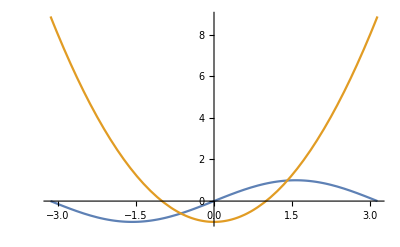

```mathematica
Plot[{Sin[x], x^2-1},{x,-Pi,Pi}]
```

```mathematica
FindRoot[Sin[x]==x^2-1, {x,-1}]
```

{x→-0.636733}

例题：求方程x*sin (x) = 1 在区间[-10，10] 上的解。

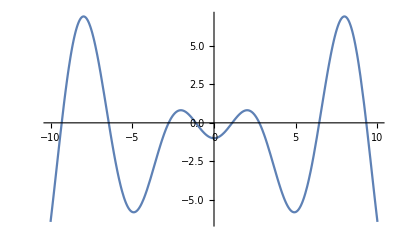

```mathematica
Plot[x*Sin[x]-1,{x,-10,10}]
```

```mathematica
a={-9,-6,-3,-1,1,3,6,9}
```

{-9,-6,-3,-1,1,3,6,9}

```mathematica
Table[FindRoot[x*Sin[x]==1,{x,a[[i]]}],{i,8}]
```

{{x→-9.31724},{x→-6.43912},{x→-2.7726},{x→-1.11416},{x→1.11416},{x→2.7726},{x→6.43912},{x→9.31724}}

例题： 求方程组{e^x+ln y=2
sin x+sin y=1的近似解.

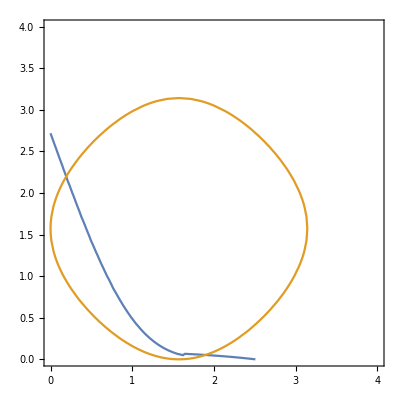

```mathematica
ContourPlot[{Exp[x]+Log[y]==2, Sin[x]+Sin[y]==1},{x,0,4},{y,0,4}]
```

```mathematica
sol1=FindRoot[{Exp[x]+Log[y]==2, Sin[x]+Sin[y]==1},{x,0.4},{y,2}]
```

{x→0.192202,y→2.19918}

Reduce[expr, vars, dom]  
 化简方程或不等式expr并求所有解vars

FindInstance[expr, vars, dom, n]
求方程或不等式expr的n个特解vars

```mathematica
Reduce[a*x^2+b*x+c==0,x]
```

(a≠0&&(x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)))||(a==0&&b≠0&&x==-c/b)||(c==0&&b==0&&a==0)

Reduce 给出的结果是表示方程的所有可能解的逻辑语句,  弄清参数在什么值下解存在

```mathematica
Reduce[3x-2y>a&&x+y<b,{x,y}]
```

(a|b)∈ℝ&&((x≤1/5 (a+2 b)&&y<1/2 (-a+3 x))||(x>1/5 (a+2 b)&&y<b-x))

```mathematica
FindInstance[x^2+y^2==z^2&&0<x<y<z<20,{x,y,z},Integers,3]
```

{{x→3,y→4,z→5},{x→9,y→12,z→15},{x→5,y→12,z→13}}

### 3 递归方程的求解

RecurrenceTable[eqns, expr, nspec]
由递归关系eqns求表达式expr生成的数列

RSolve[eqns, a[n], n]
由递归关系eqns求数列an的通项公式

```mathematica
RecurrenceTable[{a[n+2]==a[n+1]+a[n],a[1]==a[2]==1},a[n],{n,10,20}]
```

{55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
RSolve[b[1+n]==1/3 (x* b[n]+y),b[n],n]
```

{{b[n]→-(3^-n (3^n-x^n) y)/(-3+x)+3^(1-n) x^(-1+n) C[1]}}

## 2.4 求和与乘积运算

### 1 求和

Sum[f,{i,m,n,d}]   
求和f(i)，其中i在区间[m,n]上以步长d变化

Sum[f,{i,list}]
求和f(i)，其中i为列表list中的元素

Sum[f,{i1,m1,n1,d1},{i2,m2,n2,d2},...]
多指标求和f(i1,i2,...)，其中i1为最外层循环指标

Sum[f,i]
形式求和，结果g满足g(i)-g(i-1)=f(i)

```mathematica
Sum[1/(n^3),{n,10}]		(* 计算∑_(n=1)^10 1/n^3 准确值*)
```

19164113947/16003008000

```mathematica
NSum[1/n^3,{n,10}]                 (* 计算∑_(n=1)^10 1/n^3 近似值*)
```

```mathematica
N[Sum[1/(n^3),{n,10}],20]
```

1.1975319856741932517

```mathematica
Sum[1/n^2,{n,Infinity}]   (*Sum可无穷求和*)
```

π^2/6

```mathematica
Sum[i^2,{i,m,n}]      (*求和界限可以是变元*)
```

-1/6 (-1+m-n) (-m+2 m^2+n+2 m n+2 n^2)

### 2 求乘积

Product[f,{i,m,n,d}]   
乘积f(i)，其中i在区间[m,n]上以步长d变化

Product[f,{i,list}]
乘积f(i)，其中i为列表list中的元素

Product[f,{i1,m1,n1,d1},{i2,m2,n2,d2},...]
多指标乘积f(i1,i2,...)，其中i1为最外层循环指标

Product[f,i]
形式乘积，结果g满足g(i)/g(i-1)=f(i)

```mathematica
Product[n^2,{n,10}]
```

13168189440000

# 第3章 微积分

## 3.1 求极限

计算函数极限的形式：Limit [ expr, x -> x0]

例1 ： 求下列极限
(1) lim_(x→0) sin(a x)/x       (2)lim_(x→1) (m/(1-x^m)-n/(1-x^n))

```mathematica
Limit[Sin[a x]/x, x -> 0]
```

a

```mathematica
Limit[m/(1-x^m)-n/(1-x^n), x->1]
```

(m-n)/2

不是所有的函数都有确定的极限，例如 , 极限不存在，在0附近，函数在[-1, 1] 之间波动，Limit运算的结果是一个区间。

```mathematica
Limit[Sin[1/x],x->0]
(1+%)^2*5
```

Indeterminate

Indeterminate

数列的极限，可以用同样的形式进行计算。

```mathematica
Limit[Sqrt[n + Sqrt[n]]- Sqrt[n], n -> Infinity]
```

1/2

```mathematica
Limit[n!/n^n, n -> Infinity]
```

0

有些函数在特定点处，从不同方向趋于该点有不同极限,使用 limit 中的 Direction 选项， 可以指定趋近的方向.
Limit[expr, x -> x0] | 计算 x → x0时函数expr 的极限
Limit[expr, x -> x0, Direction -> 1] | 计算x → x0时函数expr的左极限
Limit[expr, x -> x0, Direction -> -1] | 计算x → x0时函数expr的右极限

```mathematica
Limit[Log[x]/x, x -> 0, Direction -> -1]
```

-∞

```mathematica
Limit[ArcTan[1/x], x->0, Direction->1]
```

-π/2

```mathematica
Limit[Gamma[x + 1/2]/(Sqrt[x]*Gamma[x]),  x -> Infinity]
```

1

Limit 函数自己不带对多个变量取极限的功能即不能计算重极限，可以计算累次极限。

```mathematica
Limit[Limit[((x*y)/(x^2 + y^2))^(x^2),  x -> Infinity],y -> Infinity]
```

0

```mathematica
Limit[Limit[((x*y)/(x^2 + y^2))^(x^2),  y -> Infinity], x -> Infinity]
```

0

还可以计算自变量沿某一固定路径趋向于固定点时，表达式的极限

```mathematica
Clear[t,a,x,y]
```

```mathematica
Limit[(x^2+y^2)/(1-(1+x^2+y^2)^(1/2))/.{y->a t^2,x->t},t->0]
```

-2

## 3.2 微商和微分

### 1.偏微分

D[f,x] | 偏导数(∂f/∂x)
D[f,x1,x2,.85,xn] | 高阶偏导数
D[f,{x,n}] | n阶导数
D[f,x,NonConstants→{y1,y2,...,ym}] | 复合函数的偏导数∂f/∂x，y1,...,ym是x的函数
D[f,{{x,y,z,...}}] | 偏导向量(∂f/∂x,∂f/∂y,∂f/∂z,...)
   对于一元函数来说，指令D求的是变量的导数，对于多元函数，求的是偏导数，假定其余变量均与要求导的变量无关，若求复合函数的偏导，需给出假设条件NonConstants→{z}，指明变量z 是依赖其他变量的函数.

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[x^n,{x,2}]
```

(-1+n) n x^(-2+n)

```mathematica
D[z (x^2+y^2),x,y]
```

0

```mathematica
D[z (x^2+y^2),{x,2}]
```

2 z

```mathematica
D[z (x^2+y^2),{{x,y}}]
```

{2 x z,2 y z}

```mathematica
D[z (x^2+y^2),{{x,y,z},2}]
```

```mathematica
{{2 z,0,2 x},{0,2 z,2 y},{2 x,2 y,0}}//MatrixForm
```

(2 z | 0 | 2 x
0 | 2 z | 2 y
2 x | 2 y | 0)

```mathematica
D[z (x^2+y^2),{{x,y}},NonConstants->{z}]
```

{2 x z+(x^2+y^2) D[z,x,NonConstants→{z}],2 y z+(x^2+y^2) D[z,y,NonConstants→{z}]}

### 2. 全微分与全导数

Dt[f] | f的全微分
Dt[f,x] | f的全导数
Dt[f,{x,n}] | f对x的n阶导数
Dt[f,x1,x2,…] | f的混合导数
Dt[f,x,Constants→{c1,c2,…}] | "全导数,c1,c2,…不依赖于x"

```mathematica
D[x^2+y^2,x]
```

2 x

```mathematica
Dt[x^2+y^2,x]
```

2 x+2 y Dt[y,x]

```mathematica
Dt[x^2+y^2,x,Constants->{y}]
```

2 x

```mathematica
Dt[x^2+y^2]
```

2 x Dt[x]+2 y Dt[y]

```mathematica
Dt[x^2+y^2+z^2,{x,2}]
```

2+2 Dt[y,x]^2+2 y Dt[y,{x,2}]+2 Dt[z,x]^2+2 z Dt[z,{x,2}]

### 3.抽象函数的导数表示

"f'[x]" | "单变量函数的导数"
"f^(n)[x]" | "单变量函数的n阶导数"
"f^(n1,n2,...)[x1,x2,...]" | "多变量函数的混合偏导"

```mathematica
(Log[x]*Sin[x])'
```

(Log[x] Sin[x])'

```mathematica
f[x_]:=Sin[x];
{f'[x],f''[x],f'''[x],(f^(4))[x]}
```

```mathematica
Clear[f]
```

```mathematica
D[f[x],{x,4}]
```

f^(4)[x]

```mathematica
Clear[h]
```

```mathematica
D[h[x,y],{x,3},{y,2}]
```

h^(3,2)[x,y]

用户可以定义单变量函数 f 在 Mathematica 中的导数,这只需简单地进行赋值即可.
例如 定义f'[x_] := h f[x] + g f[x].接下来就可以根据定义的规则计算导数.

```mathematica
Clear[f,g]
```

```mathematica
f'[x_] := h f[x] + g f[x]
D[f[x^2],x]
f'[x^2]
```

2 x (g f[x^2]+h f[x^2])

g f[x^2]+h f[x^2]

例：对于函数, 求出使得微分中值定理在区间[0, 2] 上成立的值.

```mathematica
Clear[f,a,b];
f[x_]:=Sqrt[x]+Sin[2π x];
a=0;b=2;m=(f[b]-f[a])/b-a;
Plot[f'[x]-m,{x,0,2}]
```

```mathematica
t1=FindRoot[f'[x]==m,{x,0.3}]
t2=FindRoot[f'[x]==m,{x,0.7}]
t3=FindRoot[f'[x]==m,{x,1.3}]
t4=FindRoot[f'[x]==m,{x,1.7}]
```

```mathematica
g=Plot[{f[x],m x},{x,0,2}];
g1=Plot[m(x-0.25707061913)+f[0.25707061913],{x,0,0.6}];
g2=Plot[m(x-0.753319266)+f[0.753319266],{x,0.5,1.2}];
g3=Plot[m(x-1.243444795)+f[1.243444795],{x,1.0,1.6}];
g4=Plot[m(x-1.75836391)+f[1.75836391],{x,1.5,2.0}];
Show[{g,g1,g2,g3,g4}]
```

### 4.导数应用

■FindMinimum[f[x], x]                                     从自动选择的点计算极小值及点坐标
■FindMinimum[f[x], {x, x0}]                          求出f (x) 靠近x0点的极小值点和极小值
■FindMinimum[f, {{x, x0}, {y, y0}, …}]       多变量函数在指定点附近的极小值

FindMinimum利用修正的最速下降法计算函数的极小值, 可以用选项 Method -> Newton, Method -> QuasiNewton改变所用的方法.
求极大值可以用 FindMaximum[f[x], {x, x0}] 等.

例题：求f(x)=x+Sin(3x)在[0,Pi]中的极小值和极大值.

```mathematica
f[x_]:=x+Sin[3x];
Plot[x+Sin[3x],{x,0,Pi}]
```

```mathematica
FindMinimum[f[x],{x,1.0}]
```

```mathematica
{FindMaximum[f[x],{x,0.5}],FindMaximum[f[x],{x,2.5}]}
```

例：求函数f (x, y, z) = x y z满足x^2 + 2 y^2 + 3 z^2 = 6 条件下的条件极值.

```mathematica
Clear[f,g,cond,x,y,z,a];
f[x_,y_,z_]=x y z;
g[x_,y_,z_]=x^2+2y^2+3z^2-6;
cond=Eliminate[{D[f[x,y,z],x]==a D[g[x,y,z],x],D[f[x,y,z],y]==a D[g[x,y,z],y],D[f[x,y,z],z]==a D[g[x,y,z],z],g[x,y,z]==0},a]
```

```mathematica
points=Solve[cond, {x,y,z}]
```

```mathematica
value=f[x,y,z]/.points
```

```mathematica
Min[value]
Max[value]
```

#### 3. 矢量运算

■Div[{f1, f2, f3}, {var}, .94coordsys.94]                                     按设定的坐标系计算散度
■Div[{f1, f2, f3}, {x, y, z}]                                                     按直角坐标系计算散度
■Curl[{f1, f2, f3}, {x1, x2, x3}, .94coordsys.94]                       按设定的坐标系计算旋度
■Curl[{f1, f2, f3}, {x1, x2, x3}]                                           按直角坐标系计算旋度
■Grad[f, {x, y, z}]                                                                   按直角坐标系计算梯度
■Laplacian[f, {x, y, z}]                                                        计算Δf (x, y, z)

```mathematica
Clear[F,f,x,y,z]
F={Sqrt[x^2+y^2+z^2],2x y,Sin[z]/(x+y)};
```

```mathematica
Div[F,{x,y,z}]
Curl[F,{x,y,z}]
```

```mathematica
Grad[Sqrt[x^2+y^2+z^2],{x,y,z}]
Laplacian[f[x,y,z],{x,y,z}]
```

■设定坐标系："Polar"，"Cylindrical"，"Spherical"

```mathematica
Curl[{f[r,θ,z],g[r,θ,z],h[r,θ,z]},{r,θ,z},"Cylindrical"]
Grad[r^2 Sin[theta],{r,theta,phi}]
```

## 3.3 不定积分和定积分

### 1. 不定积分

■￿Integrate[f, x] 计算不定积分，输出结果中省略积分常数。
■￿Integrate[f, x, y] 计算二重积分，积分的顺序是从右自左，先对变量y做积分计算，再对变量x做积分计算
Integreate主要计算只含有 "简单函数" 的被积函数。"简单函数" 包括有理函数、指数函数、对数函数、三角和反三角函数。

```mathematica
Integrate[3 a x^2,x]
```

```mathematica
Integrate[Sqrt[x^2-a^2],x]
```

```mathematica
Integrate[Sqrt[Cos[x]],x]
```

```mathematica
Integrate[1/(1+x^4),x]
```

```mathematica
TraditionalForm[%]
```

Mathematica 可以计算在标准积分表中能找到的初等函数的反导数，但是如果不能用初等函数表示反导数，这个软件就会尝试用特殊函数表示反导数.如果这还不行的话, 它就会返回无法计算的积分

```mathematica
Integrate[Sin[x^2],x]
```

```mathematica
Integrate[Sin[Sin[x]],x]
```

Integrate可以计算形式上的积分

```mathematica
Integrate[E^x*(f[x]+f'[x]),x]
```

Integrate可以计算分段函数积分

```mathematica
Integrate[Piecewise[{{1,x<1},{x,x⩾1}}],x]
```

Mathematica可以对向量值函数积分

```mathematica
Integrate[{x,E^x,Sin[x]},x]
```

### 2. 定积分

■Integrate[f, {x, a, b}]                                      计算定积分的准确解
■NIntegrate[f, {x, a, b}]                                  计算定积分的数值解
■Integrate[f, {x, a, b}, {y, c, d}]                    计算定积分的准确解
■NIntegrate[f, {x, a, b}, {y, c, d}]                计算定积分的数值解

对简单情形，求定积分可通过先求不定积分然后计算相应积分限处的值.但许多函数的不定积分不能用标准数学函数表出.但其定积分仍然能求出.

```mathematica
Integrate[Cos[Sin[x]],x]
```

```mathematica
Integrate[Cos[Sin[x]],{x,0,Pi}]
```

广义积分Cauchy主值 Integrate[f, {x, xmin, xmax}, PrincipalValue -> True]

```mathematica
Integrate[1/x, {x, -1, 2}, PrincipalValue->True]
```

计算二重积分，要注意积分顺序

```mathematica
Integrate[x+y,{x,1,2},{y,1,x}]
Integrate[x+y,{y,1,x},{x,1,2}]
```

例：计算二重积分∫∫_D ⅇ^(-(x^2+y^2))ⅆxⅆy，其中D为单位圆内部

解：用极坐标计算

```mathematica
f[x_,y_]:=Exp[-x^2-y^2];
a=1;
Integrate[r f[r Cos[t],r Sin[t]],{r,0,2 Pi},{r,0,a}]
```

例：计算二重积分(∫∫_D ArcTan[y/x]ⅆxⅆy)，其中D={(x,y)|1≤x^2+y^2≤4,  0≤y≤x}

```mathematica
f[x_,y_]:=ArcTan[y/x];
Integrate[r f[x,y]/.{x->r Cos[t],y->r Sin[t]},{t,0,Pi/4},{r,1,2}]
```

例：利用二重积分汁算由抛物线 y = x^2 - 2 x + 2 与直线y = x + 1 围成区域的面积.

```mathematica
intersection=Solve[x^2-2x+2==x+1,x]
```

```mathematica
Plot[{x^2-2x+2,x+1},{x,-1,3}]
```

```mathematica
a=intersection[[1,1,2]];
b=intersection[[2,1,2]];
Integrate[1,{x,a,b},{y,x^2-2x+2,x+1}]
```

解法2：用Boole函数定义积分区域

```mathematica
Integrate[Boole[(y≥x^2-2x+2)&&(y≤x+1)],{x,0,3},{y,0,5}]
```

利用定积分的计算公式，我们可以计算三重积分，曲线积分，曲面积分等，下面看几个例子.

例：计算∫∫∫_V xy^2 z^3 ⅆxⅆyⅆz 其中V是由曲面z=xy,z=0,y=x,x=1围成。

```mathematica
Clear[x,y,z]
Integrate[x*(y^2)*(z^3),{x,0,1},{y,0,x},{z,0,(x*y)}]
```

例 计算三重积分∫∫∫_v zⅆxⅆyⅆz，其中V:x^2+y^2≤z≤4

先用直角坐标

```mathematica
f[x_,y_,z_]:=z;
Integrate[f[x,y,z],{x,-2,2},{y,-Sqrt[4-x^2],Sqrt[4-x^2]},{z,x^2+y^2,4}]
```

再用柱面坐标计算

```mathematica
Integrate[r f[x,y,z]/.{x->r Cos[t],y->r Sin[t]},{t,0,2Pi},{r,0,2},{z,r^2,4}]
```

例 (球面坐标) 计算三重积分(∫∫∫_V √(x^2+y^2+z^2)ⅆxⅆyⅆz)，其中 V:x^2+y^2+z^2<z

```mathematica
f[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
Integrate[r^2 Sin[phi] f[x,y,z]/.{x->r Sin[phi] Cos[t],y->r Sin[phi]Sin[t],z->r Cos[phi]},{t,0,2Pi},{phi,0,Pi/2},{r,0,Cos[phi]}]
```

例 (参数曲线) 计算曲线积分∫_L x^2+y^2 ⅆs，其中 L:x=a(cos{t}+tsin{t}), y=a(sin{t}-tcos{t})（0<t<2Pi）

```mathematica
f[x_,y_]:=x^2+y^2;
x[t_]:=a (Cos[t]+t Sin[t]);y[t_]:=a (Sin[t]-t Cos[t]);
Integrate[Sqrt[x'[t]^2+y'[t]^2]*f[x,y]/.{x->x[t],y->y[t]},{t,0,2Pi}]
```

例:计算曲线积分 ∫_L x^2 ⅆx+zⅆy-yⅆz，其中L: x=kt, y=acost, z=asint, (0≤t≤π)

```mathematica
P[x_,y_,z_]:=x^2;Q[x_,y_,z_]:=z;R[x_,y_,z_]:=-y;
x[t_]:=k t;y[t_]:=a Cos[t];z[t_]:=a Sin[t];
Integrate[(x'[t]P[x,y,z]/.{x->x[t],y->y[t],z->z[t]})+(y'[t]Q[x,y,z]/.{x->x[t],y->y[t],z->z[t]})+(z'[t]R[x,y,z]/.{x->x[t],y->y[t],z->z[t]}),{t,0,Pi}]
```

例 求曲面  z=x^2+2y 在区域D: {(x,y)|0≤x≤1, 0≤y≤x}上那部分的面积.

```mathematica
f[x_,y_]:=x^2+2 y;
A=Sqrt[1+D[f[x,y],x]^2+D[f[x,y],y]^2]
Integrate[A,{x,0,1},{y,0,x}]
```

例 计算曲面积分 ∫∫_Σ (x^2+y^2)zⅆS，Σ:x^2+y^2+z^2=4, z≥0

解1.用直角坐标方程计算 （）

```mathematica
Clear[x,y,F,f,z]
```

```mathematica
f[x_,y_,z_]:=(x^2+y^2)z;
F[x_,y_]:=Sqrt[4-x^2-y^2];
A=Sqrt[1+D[F[x,y],x]^2+D[F[x,y],y]^2];
B=A f[x,y,z]/.{z->F[x,y]};
Integrate[r B/.{x->r Cos[t],y->r Sin[t]},{t,0,2Pi},{r,0,2}]
```

```mathematica
f[x_,y_,z_]:=(x^2+y^2) z;
x[t_,phi_]:=2Sin[phi]Cos[t];y[t_,phi_]:=2Sin[phi]Sin[t];z[t_,phi_]:=2Cos[phi];
r[t_,phi_]:={x[t,phi],y[t,phi],z[t,phi]}
A=Norm[Cross[D[r[t,phi],t],D[r[t,phi],phi]]];
B=(f[x,y,z]/.{x->x[t,phi],y->y[t,phi],z->z[t,phi]}) A;
Integrate[B,{t,0,2 Pi},{phi,0,Pi/2}]
```

例 计算曲面积分∫∫_Σ zdydz+ydzdx+xdxdy，Σ:x^2+y^2+z^2=1（外侧）

```mathematica
P[x_,y_,z_]:=z;Q[x_,y_,z_]:=y;R[x_,y_,z_]:=x;
F={P[x,y,z],Q[x,y,z],R[x,y,z]};
x[t_,phi_]:=Sin[phi]Cos[t];y[t_,phi_]:=Sin[phi]Sin[t];z[t_,phi_]:=Cos[phi];
r[t_,phi_]:={x[t,phi],y[t,phi],z[t,phi]};
A=Cross[D[r[t,phi],phi],D[r[t,phi],t]];
F=F/.{x->x[t,phi],y->y[t,phi],z->z[t,phi]};
Integrate[F.A,{t,0,2Pi},{phi,0,Pi}]
```

## 3.4 幂级数

### 1. 幂级数的展开

■Series[expr, {x, x0, n}] 将expr在x = x0点展开到n阶的幂级数
■Series[expr, {x, x0, n}, {y, y0, m}] 先对y展开到 m阶再对x展开n阶幂级数

```mathematica
Series[Sin[x^2],{x,0,15}]
```

```mathematica
Clear[f,a]
Series[f[x],{x,a,3}]
```

```mathematica
Series[Sin[x]*Cos[y],{x,0,5},{y,0,5}]
```

（1） Series 可以生成多个变量的幂级数, Series 对变量的运算顺序与 Integrate, Sum 等是一样的，首先展开的是最后一个指定的变量.（2） 展开式中可能将分数指数，对数函数等作为基本元素

```mathematica
Series[Sqrt[x],{x,0,10}]
```

```mathematica
Series[Sqrt[1+x],{x,0,10}]
```

```mathematica
Series[Exp[Sqrt[x]],{x,1,6}]
```

```mathematica
Series[x^x,{x,0,4}]
```

（3） Series命令可以计算无界函数在瑕点的洛朗展开式, 展开式的最高次数可以是负数。

```mathematica
Series[1/((E^x-1)^10),{x,0,-2}]
```

```mathematica
Series[Exp[1/x],{x,Infinity,6}] (*x=0是本性奇点*)
```

### 2. 幂级数的运算

#### （1） 幂级数的简单运算

```mathematica
t=Series[Exp[x],{x,0,4}]
t^2
D[t,x]
Integrate[%,x]
```

例：求幂级数 ∑_(n=0)^∞ x^(4n+1)/(4n+1)的收敛域及和函数。

```mathematica
a[n_]:=1/(4*n+1);
f[x_,n_]:=a[n]*x^(4 n+1);
r=Limit[Abs[a[n+1]/a[n]],n->Infinity]
```

检查端点是否收敛

```mathematica
Sum[f[1,n],{n,1,Infinity}]
Sum[f[-1,n],{n,1,Infinity}]
```

两个端点都是发散点。收敛域 （-1, 1）

```mathematica
Sum[f[x,n],{n,1,Infinity}]
Sum[D[f[x,n],x],{n,1,Infinity}]
Integrate[%,x]
```

#### （2） 给出幂级数中某一项的系数

■SeriesCoefficient[f, n] 级数f中x^n的系数
■SeriesCoefficient[f, {x, x0, n}] 函数f在x0的展开式中 (x - x0)^n的系数

```mathematica
SeriesCoefficient[Sin[x],{x,0,3}]
SeriesCoefficient[Exp[x],{x,0,n}]
```

#### (3)幂级数的复合与反演

■ComposeSeries[sreies1, series2, .85]，复合幂级数
■InverseSeries[series，x]                         反演幂级数

```mathematica
a=Series[Exp[x],{x,0,11}];
b=Series[Sin[x],{x,0,11}];
ComposeSeries[a,b]
Series[Exp[Sin[x]],{x,0,11}]
```

用函数y = f (x) 的幂级数，计算反函数x = f^(-1) (y) 的幂级数，求出的结果用x做自变量表示。

```mathematica
s=Series[Sin[x],{x,0,7}]
InverseSeries[s]
Series[ArcSin[x],{x,0,7}]
InverseSeries[s,y] (*x=Sin^(-1)[y]的幂级数，自变量为y*)
```

■Normal[series] 表达式 将幂级数转为正常的表达式截断幂级数，假定高阶项为0

```mathematica
Normal[s]
Factor[%]
```

### 3. Fourier级数

■FourierSeries[expr, t, n] 给出关于 t 的expr 的n阶傅里叶级数展开式
■FourierSeries[expr, {t1, t2, .85}, {n1, n2, .85}] 给出一个多维傅里叶级数

```mathematica
a=FourierSeries[t^2,t,4]
ExpToTrig[a]
b=FourierSeries[t^2,t,6]
c=FourierSeries[t^2,t,8]
```

```mathematica
FourierSeries[x^2 y,{x,y},{2,2}]
```

## 3.5 微分方程

### 1.常微分方程

求解常微分方程和常微分方程组的一般形式：
■DSolve [eqns, y[x], x]	                                      解y(x)的微分方程或方程组 eqns，x为变量。
■DSolve [eqns, y, x]	                                      在纯函数的形式下求解，纯函数部分请看第7章。

DSolve 返回的结果是一个函数规则列表.问题是这些函数如何被表示.如果要求
DSolve 关于 y[x] 求解，那么 Solve 将返回 y[x] 的规则.如果用户需要符号形式的解，那么引入哑变量可能是方便的.但是，如果打算将解用于各种其它运算中，那么最好是得到不带哑变量的纯函数形式的解.

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x]
y[x]+2y'[x]+y[0]/.%
```

```mathematica
DSolve[y'[x]+y[x]==1,y,x]
y[x]+2y'[x]+y[0]/.%
```

一阶微分方程的通解中一般有一个任意常数，用c1表示，可以通过给定初始条件确定参数的值，一般 n阶方程有n个参数，用c1, c2.85表示.

```mathematica
DSolve[y''''[x]==y[x],y[x],x]
DSolve[{y''''[x]==y[x],y[0]==y'[0]==1},y[x],x]
```

求微分方程解的精确公式是困难的事情.事实上，只有很少种类的方程能求出这样的
公式解.包含高阶导数的方程，就不一定能求出解.一些简单的二阶线性方程的解被当做特殊函数来表示其它方程的解。

```mathematica
DSolve[y''[x]+y'[x]+y[x]^2==0,y[x],x]         (*无法求解*)
```

```mathematica
DSolve[x^2  y''[x] + x  y'[x] + x^2 y[x] == 0, y[x], x](*Bessel方程*)
```

```mathematica
DSolve[y'[x] == x*y[x] + 1, y[x], x]
```

微分方程组也用同一个指令求解。

```mathematica
DSolve[{y[x] == -z'[x], z[x] == -y'[x]}, {y, z}, x]
```

### 2. 偏微分方程

■DSolve[{eqn1, eqn2, ...}, y[x1, x2, ... .85], {x1, x2, ...}]                            计算偏微分方程组的准确解
■DSolve[eqn, y[x1, x2, ...], {x1, x2, ...}]                                                     解偏微分方程y[x1, x2, .85]
■DSolve[eqn, y, {x1, x2, ...}]                                                                           解偏微分方程的纯函数y

```mathematica
DSolve[D[y[x1,x2],{x1}]+D[y[x1,x2],{x2}]==1/(x1*x2),y[x1,x2],{x1,x2}]
DSolve[D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==0,u,{x,y}]
DSolve[{D[u[x,y],x]==D[v[x,y],y],D[u[x,y],y]==-D[v[x,y],x]},{u[x,y],v[x,y]},{x,y}]
```

## 3.6 积分变换

### 1.Laplace变换

函数f(t) 的Laplace变换为 ∫_0^∞ f(t)e^-st ⅆt。函数F(s) 的Laplace反变换为     1/(2πⅈ)∫_(r-ⅈ∞)^(r+ⅈ∞) F(s)e^st ⅆs

```mathematica
LaplaceTransform[t^4 Sin[t],t,s]
```

```mathematica
InverseLaplaceTransform[%,s,t]
```

### 2.Fourier变换

函数f(t)的Fourier 变换为 1/(√(2π))∫_(-∞)^(+∞) f(t)e^ⅈwt ⅆt  ，
函数F(t)的Fourier反变换为1/(√(2π))∫_(-∞)^(+∞) F(w)e^-ⅈwt ⅆw。

```mathematica
FourierTransform[Exp[-t^2],t,w]
```

```mathematica
FourierTransform[(u v)^2 Exp[-u^2-v^2],{u,v},{a,b}]
```

```mathematica
InverseFourierTransform[%,{a,b},{u,v}]
```

```mathematica
{FourierSinTransform[Exp[-t],t,w],FourierCosTransform[Exp[-t],t,w]}
```

### 3.其他积分变换

```mathematica
?*Transform
```

### 4. Convolve计算两个函数f(x)和g(x)的卷积.

```mathematica
Convolve[DiracDelta[x],f[x],x,y]
Convolve[Exp[-x] UnitStep[x],Sin[x],x,y]
```

# 第四章 线性代数

## 4.1 矩阵的定义

可以通过Mathematica的菜单项￿Insert->Table/Matrix->New...￿来插入一个矩阵
然后直接修改矩阵的元素

矩阵元素不多时，可直接列表输入

```mathematica
A={{1,2,3},{2,3,4}}//MatrixForm
```

### 1. 一般矩阵输入

在Mathematica中， 向量与矩阵是用列表表示的，向量是简单的列表，矩阵是列表的列表。

（1）向量：

Table[expr,{i, a,b,d}] 生成列表{expr(a),expr(a+d),expr(a+2d),...expr(b)}
a，d的缺省值为1

Array[f,n]    生成列表{f[1], f[2],.....f[n]}
 f是一元函数.

（2）矩阵：

Table[expr, {i,ai,bi,di} , {j,aj,bj,dj}]
 expr为矩阵元素的通项公式，是循环变量i,j的表达式，
a为循环初值，b为循环终值上界，d为循环步长。
当a或d缺省时，其值为1.

Array[f, m,n]
定义m维向量，{f[n],f[n+1],...f[n+m-1]}.

Array[f, {m,n}]
定义m行n列的矩阵，矩阵元素f[i,j], f是二元函数.

Table利用表达式定义矩阵，参数为表达式中变量取值范围，Array用函数定义矩阵，括号中只需给出函数名.

例题：Table, Array函数的用法与区别

```mathematica
a[i_,j_]:=1/(i+j-1);
```

```mathematica
A1=Table[a,{2},{2}]
```

```mathematica
A2=Array[a,{2,2}]
```

```mathematica
f[x_]:=x Sin[x];
Table[f[i], {i,1,5}]
```

```mathematica
Array[f,5]
```

```mathematica
Array[i Sin[i],5]
```

MatrixForm[列表] 将列表用矩阵形式表示.

```mathematica
A2//MatrixForm
```

```mathematica
MatrixForm[A2]
```

例题：构造一个由0-9随机数字构成的5阶方阵

```mathematica
Table[RandomInteger[{0,9},5],{i,1,5,1}]//MatrixForm
```

例题：构造一个5阶上三角方阵，上三角元素为行号与列号之和。

```mathematica
Table[If[i≤j, i+j,0],{i,5},{j,5}]//MatrixForm
```

定义上三角矩阵的函数

```mathematica
UpperDiagonalMatrix[f_, n_Integer?NonNegative] :=
 Array[If[#<=#2, f[##], 0] &, {n, n}]
UpperDiagonalMatrix[a, 5] // MatrixForm
```

```mathematica
Clear[i,j];
```

```mathematica
f[i_,j_]:=i+j
```

```mathematica
UpperDiagonalMatrix[f, 5]//MatrixForm
```

### 2 定义特殊矩阵

DiagonalMatrix[list]    以list为对角元素的对角矩阵

```mathematica
DiagonalMatrix[{a,b,c}]//MatrixForm
```

IdentityMatrix[n]   定义n阶单位矩阵

```mathematica
IdentityMatrix[5]//MatrixForm
```

ConstantArray[c,{m,n}]        元素为常数c的m行n列矩阵
HilbertMatrix[{m,n}]              m行n列 aij=1/(i+j-1)
RotationMatrix[a]                  平面上逆时针旋转a角度对应的矩阵
RotationMatrix[a,v]                空间中绕v旋转a角度对应的3阶方阵

```mathematica
HilbertMatrix[{3,4}]//MatrixForm
```

```mathematica
HankelMatrix[4]//MatrixForm
```

```mathematica
HankelMatrix[{a,b,c,d}]//MatrixForm
```

```mathematica
RotationMatrix[θ]//MatrixForm
RotationMatrix[θ,{1,1,1}]//MatrixForm
```

定义稀疏矩阵

SparseArray[rules,dims,val]                                      由rules定义的具有维数dims的稀疏矩阵，
                                                                                            未指明的矩阵元素取值val。

SparseArray[{{i1,ji}->v1,{i2,j2}->v2,...},{m,n}]           按下标位置定义稀疏矩阵元素

Band[{i,j}]                                                                          稀疏矩阵的过{i,j}位置的对角线

例题：定义7阶准对角阵，主对角线元素均为2，与主对 角线元素相邻的元素为1，其余元素为0.

```mathematica
SparseArray[{{i_,i_}->2,{i_,j_}/;j==i+1->1,{i_,j_}/;j==i-1->1},{7,7}]//MatrixForm
```

```mathematica
SparseArray[{Band[{1,1}]->2,Band[{2,1}]->1,Band[{1,2}]->1},{7,7}]//MatrixForm
```

例题：定义4×5阶稀疏矩阵M，其中M[2,3]=1，M[4,2]=5.

```mathematica
M=SparseArray[{{2,3}->1,{4,2}->5},{4,5}]//MatrixForm
```

### 3 矩阵分量的操作

由于矩阵是一个特殊的表，对矩阵分量的操作可以通过对表的操作进行,表的操作函数都同样适用于矩阵.

A[[i,j]],    Part[A,i,j]    A的i行j列元素或子矩阵，i、j为指标或指标集

语句中的i,j可以是一个整数（正数i表示第i个位置，负数-i表示倒数第i个位置），
也可以是一个指标集{i1,...,ik}或All

Take[A,i,j]     A的子矩阵，i、j代表指标集

语句中的i,j可以是一个整数（正数i表示取前i个位置，负数-i表示取后i个位置），
或有形式{m,n,s}（表示以步长s取从m到n的位置）

例题：     对题中的5阶方阵完成指定的操作。
                              (11 | 12 | 13 | 14 | 15
21 | 22 | 23 | 24 | 25
31 | 32 | 33 | 34 | 35
41 | 42 | 43 | 44 | 45
51 | 52 | 53 | 54 | 55)
             1. 提取第2行第3列元素      2. 提取第4行全部元素
             3. 提取第5列全部元素       4.提取第2,4行，1，3，5列的子矩阵   
             5. 将第一行元素乘以-2，加到第三行上.

```mathematica
matrix=Table[10i+j,{i,1,5},{j,1,5}]
```

```mathematica
matrix[[2,3]]
```

```mathematica
matrix[[4]]
```

```mathematica
matrix[[All,5]]
```

```mathematica
Part[matrix,{2,4},{1,3,5}]
```

```mathematica
Take[matrix,{2,4,2},{1,5,2}]
```

```mathematica
matrix[[3]]-=2 matrix[[1]];
matrix//MatrixForm
```

Join[矩阵1，矩阵2，...,i],           i=1时，将几个列数相同的矩阵竖排组成新矩阵
                                                                    i=2时，将几个行数相同的矩阵横排组成新矩阵

ArrayFlatten[{block1, block2}, {block3, block4}] 将几个小矩阵按块拼成新矩阵

```mathematica
A=Array[a,{2,2}];B=Array[b,{2,2}];
```

```mathematica
Join[A,B,1]//MatrixForm
```

```mathematica
Join[A,B,2]//MatrixForm
```

```mathematica
ArrayFlatten[{{A,B},{B,0}}]//MatrixForm
```

## 4.2 矩阵的基本运算

### 1.矩阵的代数运算

A+B或Plus[A,B]         矩阵或向量加法

A-B或Subtract[A,B]     矩阵或向量减法

-A或Minus[A]           负矩阵或负向量

A*B或Times[A,B]        对应元素相乘

A/B或Divide[A,B]       对应元素相除

A^n或Power[A,n]       每个元素方幂

```mathematica
Clear[A,B]
```

```mathematica
A={{1,2},{3,4}}; MatrixForm[A]

B={{5,6},{7,8}};MatrixForm[B]
```

```mathematica
A+B
```

```mathematica
A-B
```

```mathematica
A*B
```

```mathematica
A/B
```

```mathematica
A^3
```

```mathematica
5+A
```

```mathematica
{5,6}+A//MatrixForm
```

```mathematica
{{5},{6}}+A
```

A.B或Dot[A,B]矩阵乘法或向量的内积

Cross[A,B]向量的外积

Outer[Times, u,v] 外积

MatrixPower[A,n]方阵A的方幂

MatrixExp[A]方阵A的指数函数e^A

Transpose[A]矩阵A的转置

ConjugateTranspose[A]复矩阵A的共轭转置

```mathematica
a={x,y,z};b={4,5,6};{a.b,Cross[a,b]}
```

```mathematica
m={{a,b},{c,d}};v={x,y};
m.v
v.m
v.m.v
```

```mathematica
Outer[Times, {a,b,c},{x,y,z}] (*外积，两个向量的外积是矩阵, 矩阵和向量的外积是三阶张量*)
```

```mathematica
MatrixPower[A,2]
A//MatrixForm
```

```mathematica
Transpose[A]//MatrixForm
```

### 2. 行列式和逆矩阵

Det[A] 方阵A的行列式

Inverse[A] 方阵A的逆矩阵

Minors[A] 方阵A的余子式

Minors[A] 也是一个n阶方阵, 它在 (i, j) 位置上的元素是A关于 (n - i + 1, n - j + 1) 位置的余子式

Minors[A, k] 方阵A的所有k阶子矩阵的行列式
Minors[A, k] 生成一个矩阵，其元素是矩阵所有k阶子方阵的行列式.

例题  计算行列式|a | b | c | d
a | a+b | a+b+c | a+b+c+d
a | 2a+b | 3a+2b+c | 4a+3b+2c+d
a | 3a+b | 6a+3b+c | 10a+6b+3c+d|

```mathematica
A={{a,b,c,d},{a,a+b,a+b+c,a+b+c+d},{a,2a+b,3a+2b+c,4a+3b+2c+d},{a,3a+b,6a+3b+c,10a+6b+3c+d}};
A//MatrixForm 
Det[A]
```

例题   计算范德蒙行列式|1 | 1 | 1 | 1 | 1
x_1 | x_2 | x_3 | x_4 | x_5
x_1^2 | x_2^2 | x_3^2 | x_4^2 | x_5^2
x_1^3 | x_2^3 | x_3^3 | x_4^3 | x_5^3
x_1^4 | x_2^4 | x_3^4 | x_4^4 | x_5^4|

```mathematica
van=Table[x[i]^j,{j,0,4},{i,1,5}]
%//MatrixForm
Det[van]

Det[van]//Simplify
```

例题： 设A=(1 | 2 | 2
2 | 3 | 3
3 | 4 | 5)，求其逆矩阵, 余子式.

```mathematica
A={{1,2,2},{2,3,3},{3,4,5}}
Inverse[A]//MatrixForm
Minors[A]
{{-1,-1,0},{-2,-1,2},{-1,1,3}}
Minors[A,1]
Minors[A,2]
Minors[A,3]
```

### 3. 方阵的特征值和特征向量

CharacteristicPolynomial[A,x]     方阵A的特征多项式

Eigenvalues[A]      计算出方阵A的所有特征值；

Eigenvectors[A]     计算出方阵A的所有特征向量

Eigensystem[A]      同时计算出方阵A的所有特征值和特征向量

例题： 计算方阵的特征多项式，特征值，与特征向量，验证矩阵满足特征方程

```mathematica
Clear[A];A={{-2,4,1,0,2},{-4,6,1,-1,0},{0,0,3,0,0},{0,0,2,3,0},{0,0,1,0,3}};
A//MatrixForm
```

```mathematica
CharacteristicPolynomial[A,x]
```

```mathematica
108IdentityMatrix[5]-216 A+171 MatrixPower[A,2]-67 MatrixPower[A,3]+13 MatrixPower[A,4]-MatrixPower[A,5]//MatrixForm
```

```mathematica
Eigenvalues[A] 
Eigenvectors[A]
```

```mathematica
Eigensystem[A]
```

### 4. 矩阵的秩、迹、范数

MatrixRank[A]      矩阵A的秩

Norm[A,p]     矩阵A的范数，p=1,2,Infinity，缺省值2

Norm[v,p]    向量v的范数，p>=1或p=Infinity，缺省值2

Total[v]       向量v的元素和v1+...+vn

Tr[A]矩阵A的迹（对角元素和）a11+...+ann

Tr[A,f]矩阵A的广义迹f[a11,...,ann]

```mathematica
A=({{-2, 4, 1, 0, 2}, {-4, 6, 1, -1, 0}, {0, 0, 3, 0, 0}, {0, 0, 2, 3, 0}, {0, 0, 1, 0, 3}});
{MatrixRank[A],Tr[A],Total[A]}
```

例题：计算矩阵， 向量的范数.

```mathematica
matrix={{a+1,b+2,c+3},{a+2,b+3,c+4}};
Norm[matrix,1]
Norm[matrix,Infinity]
```

## 4.3 矩阵的高级运算

### 1. 线性方程组的求解

求解线性方程组 AX=B

当方阵A的行列式不为零时，线性方程组AX=B有唯一解X=A^-1B

当A的行列式为零或者A不是方阵的时候，线性方程组可能无解或有无穷多解。

线性方程组有无穷多解的时候，由基础解系向量的线性组合加上一个特解组成线性方程组的全部解

LinearSolve[A,B] | 求方程组AX=B的一个特解X
NullSpace[A] | 求齐次方程组AX=0的一个基础解系

例题1： 求解线性方程组{x+3y+2z=9
2x-y+3z=3
3x+2y-z=6

```mathematica
Clear[A,B]
A={{1,3,2},{2,-1,3},{3,2,-1}};
B={9,3,6};
Det[A]
```

```mathematica
LinearSolve[A,B]
```

求解线性方程组{x+3y+2z=9
2x-y+3z=3
3x+2y+5z=6

```mathematica
u={{1,3,2},{2,-1,3},{3,2,5}};
```

```mathematica
LinearSolve[u,B]
```

如果方程组具有惟一解,Mathematica 就会给出这个解.如果方程组没有解,Mathematica就会返回出错信息. 如果方程组AX=B 有无穷组解， 处理起来就有些复杂.对这种情况， Mathenmica 就会返回一个解， 称为特解.而所有解则是由特解加上对应的齐次方程组 a.x = 0 的所有解构成的.

例题2： 求解线性方程组{x+3y+z=1
2x-y+3z=4
x-4y+2z=3

```mathematica
Clear[A,B];A={{1,3,1},{2,-1,3},{1,-4,2}};
B={1,4,3};
Det[A]
```

```mathematica
particular=LinearSolve[A,B]
```

```mathematica
basis=NullSpace[A]
```

```mathematica
sol=basis[[1]]*t+particular
```

```mathematica
Print["线性方程组的通解为  x=",sol[[1]],",   y=",sol[[2]], ",  z=",sol[[3]]]
```

检验结果是否正确

```mathematica
A.sol//Expand
```

在线性代数课程中，我们求解线性方程组 AX=B的方法是 Gauss—Jordan方法
将增广矩阵(A|B)化为行阶梯型，从而可以看出方程组的通解。

RowReduce[A]   将矩阵A化为行最简形

例题3：求解线性方程组{x+y+z-u-v=5
3x-2y+z+2u-v=3
2x-3y+3u=-2

```mathematica
Clear[A,sol];
A={{1,1,1,-1,-1,5},{3,-2,1,2,-1,3},{2,-3,0,3,0,-2}};
MatrixForm[A]
r=RowReduce[A]//MatrixForm
```

从系数矩阵中可以看出方程组的解.

例题：用行化简解下列方程组
（1）2x+y+z=7, x-4y+3z=2,  3x+2y+2z=13 （唯一解）
（2）2x+y+z=7, x-4y+3z=2, 3x-3y+4z=10 （无解）
（3）2x+y+z=7, x-4y+3z=2, 3x-3y+4z=9  （无穷多解）

```mathematica
a1={{2,1,1,7},{1,-4,3,2},{3,2,2,13}};
RowReduce[a1]//MatrixForm
```

```mathematica
a2={{2,1,1,7},{1,-4,3,2},{3,-3,4,10}};
RowReduce[a2]//MatrixForm
```

```mathematica
a3={{2,1,1,7},{1,-4,3,2},{3,-3,4,9}};
RowReduce[a3]//MatrixForm
```

### 2. 线性空间相关运算

考虑由一组向量生成的线性空间，我们需要了解一下问题：

线性空间的维数

线性空间的一组标准正交基

生成线性空间的向量的极大无关组

这些问题可以用一下命令给出解答

维数=Rank[{α_1,α_(2,)... α_n}],n个向量组成的矩阵的秩

Orthogonalize[{α_1,α_(2,)... α_n}] ,对n个行向量作标准正交化

从最简行梯形矩阵中可以看出极大无关组

例题4：设A=(2 | -1 | -1 | 1 | 2
1 | 1 | -2 | 1 | 4
4 | -6 | 2 | -2 | 4
3 | 6 | -9 | 7 | 9
2 | -5 | 3 | -3 | 2) ，求的列向量组的一个极大无关组.

```mathematica
Clear[];A={{2,-1,-1,1,2},{1,1,-2,1,4},{4,-6,2,-2,4},{3,6,-9,7,9},{2,-5,3,-3,2}};
A//MatrixForm
RowReduce[A]//MatrixForm
```

例题5：将向量 a1=(1,1,0,0),a2=(1,0,1,0), a3=(-1,0,0,1),a4=(1,-1,-1,1)转化为标准正交基。

```mathematica
Clear[];
A={{1,1,0,0},{1,0,1,0},{-1,0,0,1},{1,-1,-1,1}};
MatrixForm[A]
```

```mathematica
Orthogonalize[A]//MatrixForm
```

Normalize[v,f]       将向量单位化

Projection[u,v,f]    求向量u在v方向上的投影分量
f是线性空间中内积的定义， f 缺省时使用标准复内积和L2范数

```mathematica
Normalize[{a,b,c}]
Projection[{x,y,z},{a,b,c},Dot]
```

例题6：在区间[0,1]上定义连续函数的内积
       (f,g)=∫_0^1 xf(x)g(x)dx，
求多项式空间{a+bx+cx^2| a,b,c 是任意实数}的一组标准正交基.

```mathematica
F[f_,g_]:=Integrate[x*f*g,{x,0,1}];
Orthogonalize[{1,x,x^2},F]
Projection[f[x],g[x],F]
```

### 3 矩阵的乘积分解

JordanDecomposition[A]
对方阵A返回{P,J}使A=PJP-1，J是Jordan标准形。

LUDecomposition[A]
对方阵A返回{lu,p,c}使A=P.L.U。
L是单位下三角，U是上三角，L和U被压缩到一个矩阵中表示，置换方阵P，表示对A进行行位置的变换，c是矩阵A的L^∞条件数。

例题7：设A=(-2 | 4 | 1 | 0 | 2
-4 | 6 | 1 | -1 | 0
0 | 0 | 3 | 0 | 0
0 | 0 | 2 | 3 | 0
0 | 0 | 1 | 0 | 3) ，求A的Jordan标准型和过渡矩阵。

```mathematica
Clear[];A=({{-2, 4, 1, 0, 2}, {-4, 6, 1, -1, 0}, {0, 0, 3, 0, 0}, {0, 0, 2, 3, 0}, {0, 0, 1, 0, 3}}) ;
```

```mathematica
l=({{1, 0, 0}, {2, 5, 1}, {3, 1, 0}}); u=({{3, 1, 2}, {0, 2, 1}, {0, 0, 2}}); l.u//MatrixForm
```

JordanDecomposition[A]
对方阵A返回{P,J}使A=PJP-1，J是Jordan标准形。

LUDecomposition[A]
对方阵A返回{lu,p,c}使A=P.L.U。
L是单位下三角，U是上三角，L和U被压缩到一个矩阵中表示，置换方阵P，表示对A进行行位置的变换，c是矩阵A的L^∞条件数。

例题7：设A=(-2 | 4 | 1 | 0 | 2
-4 | 6 | 1 | -1 | 0
0 | 0 | 3 | 0 | 0
0 | 0 | 2 | 3 | 0
0 | 0 | 1 | 0 | 3) ，求A的Jordan标准型和过渡矩阵。

```mathematica
Clear[];A=({{-2, 4, 1, 0, 2}, {-4, 6, 1, -1, 0}, {0, 0, 3, 0, 0}, {0, 0, 2, 3, 0}, {0, 0, 1, 0, 3}}) ;
```

```mathematica
l=({{1, 0, 0}, {2, 5, 1}, {3, 1, 0}}); u=({{3, 1, 2}, {0, 2, 1}, {0, 0, 2}}); l.u//MatrixForm
```

# 第5章概率统计

Mathematica 8 提供一整套高级的概率和统计函数。新的功能包括计算任何事件的概率或任何表达式的期望，模拟任何分布以及自动估计参数或测试分布的拟合优度。为了更好地支持分布模型，并对其进行分析，Mathematica 8 提供大量概率分布函数，以及对数十个属性的完全支持，包括分布函数、矩、分位数和母函数。

## 5.1 概率分布

### 1. 事件的概率

Probability[expr, x Esc dist Esc distribution]
x服从某分布时，事件expr的概率，expr 用逻辑表达式表示事件.

Probability[pred, {x1, x2, …} Esc dist Esc distribution], x1, x2, …服从多变量联合分布时事件的概率

Probability[expr1 Esccond Esc expr2, x Esc dist Esc distribution]
给出满足 事件expr2条件下，expr1 的条件概率.下表是常见的概率分布

例题 ：抛掷一个六面均匀的骰子得到三的概率

```mathematica
Probability[x==3,x\[Distributed]DiscreteUniformDistribution[{1,6}]]
```

抛掷两个均匀六面骰子得到点数 7 的概率

```mathematica
Probability[x+y==7,{x,y}\[Distributed]DiscreteUniformDistribution[{{1,6},{1,6}}]]
```

多元分布的概率

```mathematica
Probability[x≤2∧y≤3,{x,y}\[Distributed]MultivariatePoissonDistribution[1,{2,3}]]
```

例题： 正态分布概率的计算，X服从N (0.5, 2), 计算
   1.  P (X < 2),     2.  P (| X|> 1.3),    3.  P (| X - 1 | < 0.6)

```mathematica
Probability[X<2,X\[Distributed]NormalDistribution[0.5,2]]
Probability[Abs[X]>1.3,X\[Distributed]NormalDistribution[0.5,2]]
Probability[Abs[X-1]<0.6,X\[Distributed]NormalDistribution[0.5,2]]
```

例题： x服从指数分布, 计算条件概率P (x^2 > 1 | x > 1/2)

```mathematica
Probability[x^2>1\[Conditioned]x>1/2,x\[Distributed]ExponentialDistribution[1/2]]
```

例题：一元二次方程的系数服从[0, 1] 上的均匀分布，求方程有实根的概率

```mathematica
Probability[Discriminant[a x^2+b x+c,x]≥0,{a,b,c}\[Distributed]UniformDistribution[{{0,1},{0,1},{0,1}}]]
```

### 2. 分布函数与概率密度函数

PDF[dist, x] 某分布的概率密度函数

PDF[dist, {x1, x2, …}] 某多元联合分布的概率密度函数

```mathematica
dist=PDF[PoissonDistribution[3],x]
ListPlot[Table[PDF[dist,x],{x,0,10}]]
```

```mathematica
PDF[NormalDistribution[0,1],x]
Plot[%,{x,-5,5},Filling->Axis]
```

```mathematica
PDF[BinormalDistribution[{1,2},{1,1},1/3],{x,y}]
Plot3D[%,{x,-2,4},{y,-1,5}]
```

CDF[dist, x] 给出在 x 上计算的分布 dist 的累积分布函数.

CDF[dist, {x1, x2, …}] 给出在 {x1, x2, …} 上计算的分布dist的多变量累积分布函数.

例题：正态分布概率的计算，X服从N (0.5, 2), 计算   P (X < 2), P(|X|> 1.3).

```mathematica
CDF[NormalDistribution[0.5,2],2]
```

```mathematica
1-CDF[NormalDistribution[0.5,2],1.3]+CDF[NormalDistribution[0.5,2],-1.3]
```

### 6.2 随机变量的各阶矩

Expectation[expr, x \[Distributed] dist] 假定 x 服从概率分布 dist，给出 expr 的期望值.

Expectation[expr, x \[Distributed] data] 假定 x 服从由 data 给定的概率分布，给出 expr 的期望值.

Expectation[expr, {x1, x2, …} \[Distributed] dist] 假定 {x1, x2, …} 服从多元分布 dist，给出 expr 的期望值.

Expectation[expr, {x1 \[Distributed] dist1, x2 \[Distributed] dist2, …}]
假定 x1、x2、… 独立且服从分布 dist1、dist2、…，给出 expr 的期望值.

Expectation[expr\[Distributed] pred, …] 已知 pred，给出 expr 的条件期望值.

```mathematica
Expectation[x^2+7 x+8,x\[Distributed]PoissonDistribution[μ]]
```

```mathematica
Expectation[x^3+4 y-a z,{x,y,z}\[Distributed]MultinomialDistribution[10,{1/2,1/3,1/6}]]
```

```mathematica
Expectation[Abs[2 x-1],x\[Distributed]ExponentialDistribution[λ]]
```

```mathematica
Expectation[x^2+1\[Conditioned]x>1/2,x\[Distributed]LaplaceDistribution[0,1/2]]
```

Variance[list] 给出 list 中元素的样本方差.

Variance[dist] 给出 dist 分布的方差.

```mathematica
Variance[ExponentialDistribution[λ]]
```

Correlation[dist] 给出多变量符号分布 dist 的相关矩阵.

```mathematica
Correlation[MultivariatePoissonDistribution[μ,{2,3}]]//MatrixForm
```

MomentGeneratingFunction[dist, t] 给出分布 dist 的矩母函数，函数的自变量为 t.

MomentGeneratingFunction[dist, {t1, t2, …}] 给出多元分布 dist 的矩母函数

```mathematica
MomentGeneratingFunction[PoissonDistribution[μ],t]
```

```mathematica
MomentGeneratingFunction[NormalDistribution[μ,σ],t]
```

```mathematica
MomentGeneratingFunction[BinormalDistribution[ρ],{t1,t2}]
```

## 5.2 数理统计

### 1. 样本数据统计

Length[data] 样本数据个数

Max[data], Min[data] 数据的最大值，最小值

Mean[data] 计算样本数据 data 的均值

Median[data] 计算数据data的中值

Variance[data] 计算样本数据 data 的方差

StandardDeviation[data] 计算样本数据 data 的标准差

CentralMoment[data, k] 计算数据的 k 阶中心矩

Covariance[x, y] 计算x, y 的协方差 (无偏估计）

Correlation[x, y] 计算x, y的相关系数

Count[data, pattern] 计数与pattern匹配的元素个数

BinCounts[list，bins] 计数属于每个区间段的元素个数

BinLists[list, bins] 按照区间段将元素分组

BarChart[{y1, y2, …}] 绘制高度为y1, y2, …的条形图

Histogram[list] 绘直方图

例题：从某厂生产的某种零件中随机抽取120个，测得其质量 （单位 : g） 如下.列出分组表，并作频率直方图.
200 202 203 208 216 206 222 213 209 219 216 203
197 208 206 209 206 208 202 203 206 213 218 207
208 202 194 203 213 211 193 213 208 208 204 206
204 206 208 209 213 203 206 207 196 201 208 207
213 208 210 208 211 211 214 220 211 203 216 221
211 209 218 214 219 211 208 221 211 218 218 190
219 211 208 199 214 207 207 214 206 211 214 201
212 213 211 212 216 206 210 216 204 221 208 209
214 214 199 204 211 201 216 211 209 208 209 202
211 207 220 205 206 216 213 206 206 207 200 198

```mathematica
list={200,202,203,208,216,206,222,213,209,219,216,203,197,208,206,209,206,208,202,203,206,213,218,207,208,202,194,203,213,211,193,213,208,208,204,206,204,206,208,209,213,203,206,207,196,201,208,207,213,208,210,208,211,211,214,220,211,203,216,221,211,209,218,214,219,211,208,221,211,218,218,190,219,211,208,199,214,207,207,214,206,211,214,201,212,213,211,212,216,206,210,216,204,221,208,209,214,214,199,204,211,201,216,211,209,208,209,202,211,207,220,205,206,216,213,206,206,207,200,198};
```

```mathematica
Min[list]
Max[list]
```

```mathematica
Median[list]
```

```mathematica
{Mean[list],StandardDeviation[list]}//N
```

```mathematica
count=BinCounts[list,{190,222,4}]
```

```mathematica
center=Table[190+j*4-2,{j,1,8}]
```

```mathematica
BarChart[count/Length[list],ChartLabels->center]
```

### 2. 参数估计和检验

(1)假设样本服从N[μ, σ^2]分布，求置信度为0.95的置信区间.

```mathematica
Needs["HypothesisTesting`"]
MeanCI[list]
MeanCI[list,ConfidenceLevel->0.90]
```

VariarIceCI[list], 由数据 list 求总体方差的置信区间

FindDistributionParameters[data, dist] 
假设数据服从某类型的分布时，估计分布的参数.

ParameterEstimator是FindDistributionParameters 的一个选项，指定要使用什么参数估计方法.项缺省时是指在dist分布的假定下，获得极大似然参数估计量，下列基本设置可用在 ParameterEstimator 上：

"MaximumLikelihood" 使对数似然函数最大化
"MethodOfMoments" 匹配原始矩
"MethodOfCentralMoments" 匹配中心矩
"MethodOfCumulants" 匹配累积量
"MethodOfFactorialMoments" 匹配阶乘矩

```mathematica
data=RandomVariate[ExponentialDistribution[2],100]
```

```mathematica
FindDistributionParameters[data,ExponentialDistribution[lambda]]
```

```mathematica
Mean[data]
```

```mathematica
FindDistributionParameters[data,ExponentialDistribution[lambda],
ParameterEstimator->"MethodOfMoments"]
```

### 3. 回归分析

```mathematica
(1)线性回归模拟
```

LinearModelFit[data, funs, vars]
由 data 的数据求由基函数表 funs 中的函数的线性组合构成的回归方程，

其中 data的一般形式是 {{x11，x12，…, y1}, {x12, x22, …, y2}, …}, funs 的一般形式为 {f1, f2, …}, vars的一般形式 {x1, x2, …}, 它是 funs 中函数的自变量表.

例题：为研究某一化学反应过程中温度 x 对产品质量y 的影响，测得数据见表

x | 100 | 110 | 120 | 130 | 140 | 150 | 160 | 170 | 180 | 190
y | 45 | 51 | 54 | 61 | 66 | 70 | 74 | 78 | 85 | 89
求 : y 关于x的线性回归方程，并分析回归效果的显著性.

```mathematica
data={{100,45},{110,51},{120,54},{130,61},{140,66},{150,70},{160,74},{170,78},{180,85},{190,89}};
LinearModelFit[data,{1,x},{x}]
```

例题：一项关于水稻亩产量的研究中从 10 个农场获得水稻亩产量y与施肥量x1 播种量x2的数据，
x1 38 39 40 41 42 43 44 45 46 47
x2 50 50 52 56 60 64 60 61 62 63
y   50 51 55 59 62 64 66 68 69 71
试写出回归方程.

```mathematica
data={{38,50,50},{39,50,51},{40,52,55},{41,56,59},{42,60,62},{43,64,64},{44,58,66},{46,63,68},{47,62,69},{48,61,71}};
LinearModelFit[data,{1,x,y},{x,y}]
```

#### (2) 非线性回归模拟

NonlinearModelFit[{{x11, x12, …, y1}, {x21, x22, …, y2}, …}, form, {β1, …}, {x1, …}]
按form给出的函数拟合所给出的数据，βi是参数表，xi是变量表.

```mathematica
data={{0,1},{1,0},{3,2},{5,4},{6,4},{7,5}};
nlm=NonlinearModelFit[data,Log[a+b x^2],{a,b},x]
```

# 6.1 插值

## 1. 插值多项式

给定 n + 1 个插值点 (xi, f (xi))，i = 0, 1, …, n。构造次数至多 n 次的多项P (x), 使得P (xi) = f (xi).称P (x) 为f (x) 的插值多项式。
在实际应用中，这些插值点可能来自某次实验测量所得的数据，也可能来自某个复杂函数 的值。通过计算插值多项式，我们可以找到这些实验数据间的规律，或者使用简单的多项式函数 来近似复杂的函数。在数值计算方法中常用拉格朗日法牛顿法或样条函数构造插值多项式.

定理：给定n + 1 个点 (xi, f (xi))，i = 0, 1, …, n, 若 xi, xj 两两不同，则存在唯一一个次数不超过n的多项式Pn (x)，使得P (xi) = f (xi) 成立。

InterpolatingPolynomial[data, var]

#### 数据的输入方式如下：

InterpolatingPolynomial[{f1, f2, …}, x]，(1, f1), (2, f2), …确定的插值多项式

InterpolatingPolynomial[{{x_ 1, f_ 1}, {x_ 2, f_ 2}, …}, x],  (x_ 1, f_ 1), (x_ 2, f_ 2), …确定的插值多项式

InterpolatingPolynomial[{{{x_ 1, y_ 1, …}, f_ 1}, {{x_ 2, y_ 2, …}, f_ 2}, …}, {x, y, …}]
(x_ 1, y_ 1, …, f_ 1),  (x_ 2, y_ 2, …, f_ 2) …确定的插值多项式

InterpolatingPolynomial[{{{x_ 1, …}, f_ 1, df_ 1, …}, {{x_ 2, …}, f_ 2, df_ 2, …}, …}, {x, …}]
点 (x_ 1, ..., f_ 1) 及该点导数值，(x_ 2,  ..., f_ 2) 及该点导数值…确定的插值多项式

例题：根据下表构造插值多项式，并求6.12处近似值.
xi  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
yi | 6.35 | 6.47 | 8.2 | 9.3 | 9.68 | 9.72 | 10.0 | 9.95

```mathematica
data1={6.35,6.47,8.2,9.3,9.68,9.72,10.0,9.95};
```

```mathematica
Clear[f]
```

```mathematica
f[x_]=InterpolatingPolynomial[data1,x]
```

```mathematica
Expand[f[x]]
```

```mathematica
f[6.12]
```

```mathematica
Show[Plot[%5,{x,-1,11}],ListPlot[data1]]
```

例题：根据下表构造插值多项式 z = f (x, y)
x | 66 | 66 | 87 | 87 | 105 | 105 | 158 | 158
y | 9.8 | 10.3 | 9.7 | 13.5 | 9.9 | 14.2 | 9.6 | 12.5
z | 1.1 | 0.9 | 1.2 | 0.8 | 1.5 | 0.95 | 1.4 | 0.9

```mathematica
data2={{{66,9.8},1.1},{{66,10.3},0.9},{{87,9.7},1.2},{{87,13.5},0.8},{{105,9.9},1.5},{{105,14.2},0.95},{{158,9.6},1.4},{{158,12.5},0.9}};
```

```mathematica
g[x_,y_]=InterpolatingPolynomial[data2,{x,y}]
Expand[g[x,y]]
```

```mathematica
point={{66,9.8,1.1},{66,10.3,0.9},{87,9.7,1.2},{87,13.5,0.8},{105,9.9,1.5},{105,14.2,0.95},{158,9.6,1.4},{158,12.5,0.9}};
```

```mathematica
Show[Plot3D[g[x,y],{x,66,160},{y,9.6,14.5}],ListPointPlot3D[point]]
```

例题 : 按下列给定数据构造插值多项式：(0, f (0), f' (0)) = {0，-3.3, -2.2}, (1, f (1), f' (1)) = {1, -4.5, 0.8}.

```mathematica
data={{{0},-3.3,-2.2},{{1},-4.5,0.8}};
```

```mathematica
h[x_]=InterpolatingPolynomial[data,x]
```

```mathematica
{h[0],h'[0],h[1],h'[1]}
```

当数据点较多时，用InterpolatingPolynomial得到整区间的近似多项式， 其总体效
果就不一定好， 而且还常引起区间[x_0 ,x_n]端点处附近的剧烈振荡， 从而
产生出很大的误差.

```mathematica
tab=Table[{x,Sin[x]},{x,0,Pi,0.02}];
sin=InterpolatingPolynomial[tab,x]
```

```mathematica
Plot[sin,{x,0,Pi}]
```

InterpolatingPolynomia[]，可以将插值函数表达式显示出来.但多数情况下，构造插值函数目的侧重计算一些函数值，并不在意插值函数的具体表达式，

### 2. 分段区间上的插值函数

Interpolation[{f1, f2, …}] 对应 x 值 1、2、…，构造函数值 fi 的插值.

Interpolation[{{x1, f1}, {x2, f2}, …}] 对应 x 的值 xi，构造函数值 fi 的插值.

Interpolation[{{{x1, y1, …}, f1}, {{x2, y2, …}, f2}, …}] 构造多维数据的插值.

Interpolation[{{{x1, …}, f1, df1, …}, …}] 构造一个插值，再现导数及函数值.

Interpolation[data, x] 在点 x 求 data 的插值

函数说明：Interpolation 返回一个 InterpolatingFunction 对象.
Interpolation[data] 返回的插值函数与每个点处的 data 一致.

Interpolation 的算法是在连续数据点间拟合多项式曲线.
多项式曲线的次数由选项 InterpolationOrder 指定.默认设置是 InterpolationOrder -> 3. 
可以通过使用设置 InterpolationOrder -> 1 进行线性插值.

Interpolation 支持 Method 选项.可能的设置包括表示样条插值的 "Spline" 和厄米特插值的 "Hermite".

Interpolation[data, InterpolationOrder -> n, Method ->" Spline"]

例题：已知原始数据x = (l, 2, 4, 5)，y = (16, 12, 8, 9)，试求子区间上的低次插值多项式Pr (x) 在插值点x = 1.2 处的值, r 依次取 1，2, 3.

```mathematica
data1={{1,16},{2,12},{4,8},{5,9}};
p1=Interpolation[data1,InterpolationOrder->1]
p2=Interpolation[data1,InterpolationOrder->2]
p3=Interpolation[data1,InterpolationOrder->3]
{p1[1.2],p2[1.2],p3[1.2]}
```

```mathematica
Show[Plot[{p1[x],p2[x],p3[x]},{x,1,5}],ListPlot[data1,PlotStyle->PointSize[Large]]]
```

给定 4 个插值点，构造的插值多项式函数的次数至多为 3 次

```mathematica
Interpolation[data1,InterpolationOrder->4]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3}.

例题 : 取 f (x) = x^5 - 3 x^2 + 1 的函数值和一阶导数值构造三次样条插值，用插值函数计算
 x = 0.27 的函数值，并观察插值误差.

```mathematica
f[x_]=x^5-3x^2+1;
tt=Table[Evaluate[{{x},f[x],D[f[x],x]}],{x,0,2,0.3}];
```

```mathematica
p=Interpolation[tt]
```

```mathematica
Plot[{f[x],p[x]},{x,0.,1.7999999999999998}]
```

```mathematica
{p[0.27],f[0.27]}
```

```mathematica
Plot[f[x]-p[x],{x,0,2}]
```

例题：对随机数据，比较样条插值和分段厄米特插值

```mathematica
data=Transpose[{Range[0,10]/10,RandomReal[1,11]}]
```

```mathematica
q1=Interpolation[data,Method->"Spline"]
q2=Interpolation[data,Method->"Hermite"]
```

```mathematica
Row[{Plot[{q1[x],q2[x]},{x,0,1},PlotRange->All],Plot[{q1'[x],q2'[x]},{x,0,1},PlotRange->All]}]
```

3. 构造逼近函数
在计算一些复杂函数时，用函数Functionlnterpolation 可对复杂函数构造相对简单的 逼近函数简化计算。Functionlnterpolation生成插值形式函数。

FunctionInterpolation[expr, {x, xmin, xmax}]
对 x 从 xmin 到 xmax 计算 expr，并且构造一个 InterpolatingFunction 对象，这个对象表示对应于结果的近似函数.

FunctionInterpolation[expr, {x, xmin, xmax}, {y, ymin, ymax}, …]
构造一个具有多个自变量的 InterpolatingFunction 对象.

例题：计算 Exp[-Sin[x]^2] 的一个 InterpolatingFunction 表示：

```mathematica
f=FunctionInterpolation[Exp[-Sin[x]^2],{x,0,6}]
```

```mathematica
Plot[{f[x],f'[x]},{x,0,6}]
```

```mathematica
Plot[f[x]-Exp[-Sin[x]^2],{x,0,6}]
```

4. 点集的插值
ListInterpolation[array]
构建一个 InterpolatingFunction 对象，表示对给定数组进行插值的近似函数.

ListInterpolation[array, {{xmin, xmax}, {ymin, ymax}, …}]
指定 array 中的值来自的格点的域.可以用格线位置的确切列表代替 {xmin, xmax} 等.假设格线是等间距的.

ListInterpolation[array] 
假设格线在每个方向的整数位置.array 可以是任何维数的数组对应于有任何嵌套层数的列表.

ListInterpolation 支持 Method 选项.可能的设置包括样条插值的 "Spline" 和 Hermite 插值的 "Hermite".

```mathematica
f=ListInterpolation[{3,5,6,2,1,5}]
```

```mathematica
Plot[f[x],{x,1,6}]
```

```mathematica
Show[%,ListPlot[{3,5,6,2,1,5}]]
```

```mathematica
g=ListInterpolation[{3,5,6,2,1,5},{{0,1}}]
```

```mathematica
Plot[g[x],{x,0,1},Epilog->MapIndexed[Point[{(#2[[1]]-1)/5,#1}]&,{3,5,6,2,1,5}]]
```

```mathematica
Clear[f,x,y];
```

```mathematica
f=ListInterpolation[Table[Sin[x y],{x,0,1,.25},{y,0,2,.25}],{{0,1},{0,2}}]
Show[{Plot3D[f[x,y],{x,0,1},{y,0,2}],Graphics3D[{Red,PointSize[0.03],Table[Point[{x,y,Sin[x y]}],{x,0,1,.25},{y,0,2,.25}]}]}]
```

## 6.2 曲线拟合

曲线拟合即是利用最小二乘原理将型值进行分析运算，以求出最接近或最能表示数据趋势的函数。多项式插值要求多项式曲线必须穿过所在区间上的每个数据点。如果在全区间[x0, xn] 找插值函数，当n较大时常会引起插值曲线, 在区间端点附近的剧烈振荡 （称为 Runge 现象）。从实验者的角度看，要求逼近曲线 C, 穿过每个数据点，既无这种必要，又无进一步提高逼近精度的可能，因为数据点本身就带有各种误差。构造一条次数较低 （记为 s) 的多项式曲线 C, 只要求 C, 尽可能地贴近全部数据点，而不必穿过每一点。"尽可能地贴近"，通常选用最小二乘意义下的逼近，这就是一元拟合的概念。

```mathematica
1.线性拟合
```

Fit[data, {f1, …, fn}, {x, y, …}]
求变量 {x, y, …} 的函数 f1, …, fn 的 data 列表拟合 a1 f1 + … + an fn.

data 可以是以下格式：{v1, …, vn} 等同于 {{1, v1}, …, {n, vn}}
{{x1, v1}, …, {xn, vn}} 在坐标 xi 具有值 vi 的单变量数据
{{x1, y1, v1}, …} 在坐标 {xi, yi} 具有值 vi 的双变量数据
{{x1, y1, …, v1}, …} 在坐标 {xi, yi, …} 具有值 vi 的多变量数据

例题 : 设某次实验数据如下 :
 x 1.36 1.45 1.58 1.69 1.92 2.13
y 14.12 15.09 16.82 17.56 18.43 19.75
分别用一次多项式和二次多项式拟合.

```mathematica
data={{1.36,14.12},{1.45,15.09},{1.58,16.82},{1.69,17.56},{1.92,18.43},{2.13,19.75}};
```

```mathematica
f1=Fit[data,{1,x},x]
```

```mathematica
f2=Fit[data,{1,x,x^2},x]
```

```mathematica
f4=Fit[data,{1,x,x^2,x^3,x^4},x]
```

```mathematica
Show[Plot[{f1,f2,f4},{x,1.3,2.2}],ListPlot[data]]
```

例题 : 已知点列 {{0, 0}, {0.4, 0.1010}, {0.8, 0.8516}, {1.2, 1.0476}, {1.6, 3.0750}, {2.0, 3.4993}, {2.4, 6.0650}, {2.8, 7.9027}, {3.2, 9.7048}, {3.6, 13.9593}, {4.0, 14.6776}}, 
用多项式和三角函数 {1, x, x^2, x^3, Sin[x], Sin[2 x], Sin[3 x]} 做线性拟合。

```mathematica
data={{0,0},{0.4,0.1010},{0.8,0.8516},{1.2,1.0476},{1.6,3.0750},{2.0,3.4993},{2.4,6.0650},{2.8,7.9027},{3.2,9.7048},{3.6,13.9593},{4.0,14.6776}};
```

```mathematica
g=Fit[data,{1,x,x^2,x^3,Sin[x],Sin[2x],Sin[3x]},x]
```

```mathematica
Show[Plot[g,{x,0,4}],ListPlot[data]]
```

例题：已知数据点集
{x, y, z} = {{0, 0, 0.03}, {0, 1, 0.15}, {0, 2, 0.67}, {0, 3, 1.82}, {0, 4, 1.53}, {1, 0, 0.55}, {1, 1, 0.93}, {1, 2, 3.42}, {1, 3, 5.07}, {1, 4, 2.66}, {2, 0, 2.35}, {2, 1, 0.47}, {2, 2, 2.88}, {2, 3, 0.49}, {2, 4, 0.33}, {3, 0, 2.11}, {3, 1, 0.86}, {3, 2, 3.14}, {3, 3, 1.59}, {3, 4, 0.62}}
试求矩形域 D = [0, 3] X[0, 4] 上的二元拟合多项式P1 (x, y), P2 (x, y)，P3 (x, y).

```mathematica
data={{0,0,0.03},{0,1,0.15},{0,2,0.67},{0,3,1.82},{0,4,1.53},{1,0,0.55},{1,1,0.93},{1,2,3.42},{1,3,5.07},{1,4,2.66},{2,0,2.35},{2,1,0.47},{2,2,2.88},{2,3,0.49},{2,4,0.33},{3,0,2.11},{3,1,0.86},{3,2,3.14},{3,3,1.59},{3,4,0.62}};
```

```mathematica
p1=Fit[data,{1,x,y},{x,y}]
p2=Fit[data,{1,x,y,x y,x^2,y^2},{x,y}]
p3=Fit[data,{1,x,y,x y,x^2,y^2,x^3,x^2 y,x y^2,y^3},{x,y}]
```

```mathematica
Show[Plot3D[p1,{x,0,3},{y,0,4}],ListPointPlot3D[data]]
Show[Plot3D[p2,{x,0,3},{y,0,4}],ListPointPlot3D[data]]
Show[Plot3D[p3,{x,0,3},{y,0,4}],ListPointPlot3D[data]]
```

### 2. 最佳拟合

FindFit[data, expr, pars, vars]
求出参数 pars 的数值，使 expr 作为关于 vars 的函数给出对 data 最佳拟合

FindFit[data, {expr, cons}, pars, vars]
在带参量的约束条件 cons 下，求最佳拟合.

data 可以采用形式 {{x1, y1, …, f1}, {x2, y2, …, f2}, …}，其中坐标 x, y, … 的个数等于列表 vars 中变量的个数.data 也可以采用形式 {f1, f2, …}，假定单坐标取值 1、2、….在线性情况下，

FindFit 求出全局最优拟合.在非线性情况下，FindFit 通常求出局部最优拟合.

```mathematica
data={15 •2,20.6,27.3,36 •7,49 •2,65.6,87.6};
model=a Exp[b x];
f=FindFit[data,model,{a,b},x]
```

## 6.3 数值积分

NIntegrate[f(x),{x,xmin,xmax}] 一元函数数值积分

NIntegrate[f(x,y,…),{x,xmin,xmax},{y,ymin,ymax}] 多元函数数值积分

NIntegrate[f(x,y,…),{x,y,…}∈reg] 在区域reg上数值积分

NIntegrate[f[x],{x,xmin,x1,x2,…,xmax}]沿直线段求数值积分，从点 xmin 开始,经过点x1,x2,…,到 xmax.

```mathematica
Integrate[Sin[Sin[x]],{x,0,1}]
NIntegrate[Sin[Sin[x]],{x,0,1}]
```

求数值积分时，Mathematica 并不直接察看被积函数的函数形式.它简单地求一系列被积函数在特定点的近似函数值，然后取这些值从中导出积分的近似值.应注意的一个要点是 Mathematica 求数值积分时，它具有的被积函数的信息仅仅是被积函数的一系列数值值.要得到积分的确切结果，Mathematica 必须对被积函数的光滑性和其它性质做出某种假定.如果被积函数是严重病态的，这些假定可能失效，因此, Mathematica 可能给出错误结果.

```mathematica
NIntegrate[Exp[-x^2],{x,-10,10}]
NIntegrate[Exp[-x^2],{x,-10000,10000}]
```

例题：多元函数积分

（1） 计算平面图形面积.

```mathematica
NIntegrate[Boole[1/4≤x^2+(2 y)^2≤1∧y>x],{x,-1,1},{y,-1,1}]
```

(2) 随机区域上的三重积分

```mathematica
A=ConvexHullMesh[RandomReal[10,{50,3}]]
```

```mathematica
NIntegrate[x^2 y^2 z^2,{x,y,z}∈A]
```

指定运算结果的精度 :

如果使用 Integrate, 然后使用 N得到 数值结果，那么 N 的第二个自变量指定了精度.

对于 NIntegrate指令 可以使用选项 WorkingPrecision -> n 指定精度.

```mathematica
NIntegrate[1/x,{x,1,2},WorkingPrecision->40]
NIntegrate[1/(1+Sqrt[x]),{x,0,1},PrecisionGoal->100,WorkingPrecision->200]
```

其次，对于有奇点的积分，可以用Exclusions 排除.

例题：广义积分计算

```mathematica
NIntegrate[Log[x],{x,0,1}]
```

```mathematica
NIntegrate[1/(Sqrt[1-x] x^(1/5)),{x,0,1}]
```

```mathematica
NIntegrate[{1/Sqrt[x+y],Log[x y]},{x,0,1},{y,0,1}]
```

```mathematica
NIntegrate[Log[2-Sin[x]-Sin[y]],{x,0,4},{y,0,4},Exclusions->{{π/2,π/2}}]
```

积分区域排除使得被积函数的分母为零的曲线：

```mathematica
NIntegrate[1/Cos[x y],{x,0,5},{y,0,5},Exclusions->Cos[x y]==0]
```

```mathematica
NIntegrate[1/(x-x^2),{x,-1,2},Method->"PrincipalValue",Exclusions->x-x^2==0]
```

## 6.4 微分方程数值解

NDSolve 函数求常微分方程数值解。

近似数值求解的最大优点是不受方程类型的限制，即可以求任何形状微分方程的解 （当然要假定解的存在），但是求出的解只能是数值的 (即数据形式的) 解函数

NDSolve[eqns，y，{x，xmin, xmax}]
对常微分方程或方程组 eqns，求函数 y 关于x在[xmin, xmax] 范围内的数值解

NDSolve[{eqnl, eqn2, ...}, {yl, y2, ...}, {x, xmin, xmax}]
对常微分方程组，求函数 yl，y2, …关于；x 在[xmin, xmax] 范围内的数值解。

NDSolve 将函数 y 的解表示为 InterpolatingFunction 对象.这种对象提供独立变量x 从xmin 到xmax上的 M 的近似值.
 NDSolve 用迭代法求解.要进行计算，必须给定y[x] 和其导数y'[x] 的适当的初始或边界条件.给定的初始或边界条件必须能完全确定的解.一个典型的情形是n 阶微分方程需要给出直到n - 1 阶导数的初始条件，或给出在n个点处的边界条件.

```mathematica
NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}]
```

```mathematica
NDSolve[{y'[x]+x y[x]==0,y[0]==1,y[1]==-1},y,{x,0,1}]
```

```mathematica
S1=NDSolve[{y'[x]==y[x],y[0]==1},y,{x,0,2}]
f=S1[[1,1,2]]
f[1.6]
Plot[f[x],{x,0,2}]
```

例题：求 y''' + y'' sin y = Sqrt[y], 在[0，10] 上满足条件 y (0) = 0, y' (0) = 0.5, y'' (0) = 1 的数值解。

```mathematica
S2=NDSolve[{y'''[x]+y''[x] Sin[y[x]]==Sqrt[y[x]],y[0]==0,y'[0]==0.5,y''[0]==1},y,{x,0,10.0}]
```

例题：求解微分方程组     
x' (t) = -y (t) - x (t)^2
y' (t) = 2 x (t) - y (t)          t ∈ [0, 10] 
x (0) = y (0) = 1,

```mathematica
S3=NDSolve[{x'[t]==-y[t]-x[t]^2,y'[t]==2 x[t]-y[t],x[0]==1,y[0]==1},{x,y},{t,0,10}]
```

```mathematica
x=S3[[1,1,2]];
y=S3[[1,2,2]];
Plot[{x[t],y[t]},{x,0,10}]
ParametricPlot[{x[t],y[t]},{t,0,10}]
```

例题：求解微分方程组
y1' (x) = -5 y1 (x)
y2' (x) = y1 (x) - y2 (x)
y3' (x) = y2 (x) - y3 (x)
y4' (x) = y3 (x) - y4 (x)
y5' (x) = 2 y4 (x)
y1 (0) = 1, y2 (0) = y3 (0) = y4 (0) = y5 (0) = 0

```mathematica
eqns=Join[Table[y[i]'[x]==y[i-1][x]-y[i][x],{i,2,4}],{y[1]'[x]==-5y[1][x],y[5]'[x]==2y[4][x],y[1][0]==1},Table[y[i][0]==0,{i,2,5}]] S4=NDSolve[eqns,Table[y[i],{i,5}],{x,0,10}] For[i=1,i≤5,i++,y[i]=S4[[1,i,2]]] Plot[Table[y[i][x],{i,1,5}],{x,0,10}]
```

NDSolve 允许用户指定结果的精度或准确度.一般，NDSolve 使步长越来越小，直到得出满足 AccuracyGoal 或 PrecisionGoal 的解为止.NDSolve 使用由用户给定的 WorkingPrecision 来决定内部计算中使用的总位数.给出的 WorkingPrecision 的值应该比 AccuracyGoal 或 PrecisionGoal 的值大.缺省设置 Automatic 下，AccuracyGoal PrecisionGoal 都等于 WorkingPrecision 减去 10 位.

### 2. 偏微分方程

NDSolve[eqns, y, {x, xmin, xmax}, {t, tmin, tmax}] 求偏微分方程数值解

NDSolve[eqns, u, {t, tmin, tmax}, {x, y} ∈ Ω] 在区域 Ω 上求解时间相关偏微分方程 eqns.

例题 求弦振动方程 u_tt = 4 u_xx 满足下面定解条件的特解。
        边界条件 u (0, t) = u (π, t) = 0 
        初始条件 u (x, 0) = sin⁡x u_t (x, 0) = 0

```mathematica
NDSolve[{D[u[x,t],{t,2}]==4 D[u[x,t],{x,2}],u[0,t]==0,u[Pi,t]==0,u[x,0]==Sin[x],Derivative[0,1][u][x,0]==0},u,{x,0,Pi},{t,0,60}] Plot3D[Evaluate[u[x,t]/.%],{x,0,Pi},{t,0,60},PlotRange->All]
```

例题 求解一维热传导方程 u_t = u_xx, u (t, 0) = sin⁡t, u (t, 5) = 0, u (0, x) = 0

```mathematica
NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0,5}]
```

```mathematica
Plot3D[Evaluate[u[t,x]/.%],{t,0,10},{x,0,5},PlotRange->All]
```

## 6.5 规划问题

数学规划又称为优化方法，是运筹学的一个重要分支，在科学技术和工程实际中有着广泛的应用。一般将数学规划分为线性规划与非线性规划两大类型。假设一个函数 f有n个变量，现在要求f的最小值，但必须满足一个或多个约束条件，如果函数f和这些约束条件都是线性的就称线性规划，否则称其为非线性规划。

线性规划问题就是求一个线性函数在线性约束条件下的最值问题，通常形如:线性约束条件
a_11 x_1+a_12 x_2+⋯+a_(1n)x_n≥b_1
a_21 x_1+a_22 x_2+⋯+a_(2n)x_n≥b_2
......
a_m1 x_1+a_m2 x_2+⋯+a_mn x_n≥b_m
x_1≥0,x_2≥0,(…x)_n≥0
 求 min(c_1 x_1+c_2 x_2+⋯+c_n x_n).
此问题可以规范化写为：
X=(x_1,x_2,…,x_n),c=(c_1,c_2,…,c_n),b=(b_1,b_2,…,b_m), 
A=(a_11 | a_12 | ... | a_(1n)
a_21 | a_22 | ... | a_(2n)
... | ... | ... | ...
a_m1 | a_m2 | ... | a_mn),l=(l_1,l_2,…,l_n)

满足约束条件 AX≥b(≤或=)，X_i≥l_i 的向量 X 称为一个可行点，可行点全体所组成的集合s 称为可行域,求解线性规划的最终目的就是要在可行域 S 上寻求到一点  X^*,使目标函数值f(X^*)=(c∙X)^*在S 上达到极小

LinearProgramming[c, A, b] 求向量 X，使 c.X 在约束条件 AX >= b 和 X >= 0 下达到极小.

LinearProgramming[c, A, {{b1, s1}, {b2, s2}, …}] 求向量 X，使 c.X 在 X >= 0 和由矩阵 A 和 {bi, si} 确定的约束下达到最小.对于 A 的每个行 Ai，如果 si == 1，则相应的约束是 Ai.x >= bi，如果 si == 0，则为 Ai.x == bi，如果 si == -1，为 Ai.x <= bi.

LinearProgramming[c, A, b, {l1, l2, …}] 在由 A、b 和 xi >= li 确定的约束下最小化 c.X.

LinearProgramming[c, A, b, {{l1, u1}, {l2, u2}, …}] 在由 A、b 和 li <= xi <= ui 确定的约束下最小化 c.x.

LinearProgramming[c, A, b, lu, dom] 取在域 dom 内的 X 的元素，它是 Reals 或 Integers.

例题：在约束条件 {x + 2 y >= 2,   2 x - 3 y >= -6,   x >= 0, y >= 0} 下 求 min (2 x + 3 y) .

```mathematica
LinearProgramming[{2,3},{{1,2},{2,-3}},{2,-6}]
```

例题：在约束 {2 x_ 1 + 4 x_ 2 + 5 x_ 3 <= 100, x_ 1 + 2 x_ 2 + 3 x_ 3 >= 6,  x_ 1 >= -1, x_ 2 >= -1, 3 >= x_ 3 >= -1} 条件下计算   
max (4 x_ 1 + 5 x_ 2 + 3 x_ 3).

```mathematica
c={4,5,3} A={{2,4,5},{1,2,3}}
```

```mathematica
LinearProgramming[-c,A,{{100,-1},{6,1}},{{-1,Infinity},{-1,Infinity},{-1,3}}]
```

求最大值，参数取 - c，约束条件中有 >=, <= , 可以通过加 "-"改变不等式方向，也可以在bi后跟 1，-1，0 来说明不等式方向.

例题：一汽车厂生产大中小三种型号的汽车，每种汽车需要钢材和加工时间，利润以及工厂现有每月总量如下表所示，试制定生产规划，使利润最大.
□ | 小型 | 中型 | 大型 | 拥有量
钢材 (吨) | 1.5 | 3 | 5 | 700
工时 （时） | 280 | 250 | 400 | 80000
利润 （万元） | 2 | 3 | 4 | □

求 max (2 x_1 + 3 x_2 + 4 x_3) 
满足：{1.5 x_1 + 3x_2 + 5 x_3 <= 700，280x_1+ 250 x_2 + 400x_3 <= 80000，
x_1, x_2, x_3 为非负整数

```mathematica
c={2,3,4};
A={{1.5,3,5},{280,250,400}};
b={700,80000};
x=LinearProgramming[-c,-A,-b,0,Integers] c.x
```

LinearOptimization[f, cons, vars] 求能最小化受线性约束条件 cons 限制的线性目标函数 f 的变量 vars 的值.

LinearOptimization[c, {a, b}] 求能最小化受线性不等式约束条件ax + b >= 0 限制的线性目标函数 c.x 的实向量 x.

LinearOptimization[c, {a, b}, {aeq, beq}] 求能最小化受包括ax + b >= 0 以及线性等式约束条件a_eq x + b_eq = 0 限制的线性目标函数 c.x 的实向量 x.

例题：在约束条件 {x + 2 y >= 2， 2 x - 3 y >= -6， x >= 0, y >= 0} 下 求 min⁡ (2 x + 3 y)

```mathematica
LinearOptimization[2x+3y,{x+2y≥2,2x-3y≥-6,x≥0,y≥0},{x,y}] LinearOptimization[{2,3},{{{1,2},{2,-3},{1,0},{0,1}},{-2,6,0,0}}]
```

例题：最小化受约束条件 x + 2 y == 3, x >= 0.5, y >= 0 限制的 x + y

```mathematica
LinearOptimization[x + y, {x + 2 y == 3, x >= 0.5, y >= 0}, {x, y}]
```

```mathematica
LinearOptimization[{1, 1}, {{{1, 0}, {0, 1}}, {-0.5, 0}}, {{{1, 2}}, {-3}}]
```

### 非线性规划

在 Mathematica 中可利用 FindMinimum 函数进行非线性规划求极小值

FindMinimum[{f[x, y], 约束条件}，{x, y}]

FindMinimum[f[x], x] 用最速下降路径求f (x) 的极小值。

FindMinimum[f[x, y], {{x, x0}, {y, y0}}] 在 （x0, y0） 附近的极小值。

例题 求函数 f (x) = xsinx 在约束条件 1 <= x <= 15 下的极小值。

```mathematica
FindMinimum[{x Sin[x],1≤x≤15},x]
```

例题 求函数 x + y 在约束条件 x Cos x + 2 y >= 3, x >= 0, y >= 0 在 x = 3, y = 4 附近的极小值.

```mathematica
FindMinimum[{x+y,x Cos[x]+2y≥3&&x≥0&&y≥0},{x,3},{y,4}]
```

# 第7章 在Mathematica中作图

## §7 .1 二维图形

### 1. 一元函数作图

Plot[f, {x, xmin, xmax}] 画出函数f在[xmin, xmax] 的图形

Plot[{f1, f2, …}, {x, xmin, xmax}] 将多个函数画在一起

Plot[…, {x} ∈ reg] x 从几何区域 reg 取值

Plot[{.85,w[fi],厎,.85]  绘制 fi ，其特征由符号封装 w 所定义.

```mathematica
Plot[Tan[x],{x,-3,3}]
```

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 Pi},PlotLegends->"Expressions"]
```

例题 用区域表示自变量取值范围

```mathematica
reg1=ImplicitRegion[-2Pi≤x≤-1∨1≤x≤2Pi,{x}]
Plot[Sin[2 x],x∈reg1]
```

```mathematica
reg2=MeshRegion[{{-2},{-1},{-1/2},{1/2},{1},{2}},Line[{{1,2},{3,4},{5,6}}]];
Plot[x^2+3x,x∈reg2]
```

Plot[Evaluate[f], {x, xmin, xmax}]

（1） f是一个生成函数表的命令时，用户想要 Mathematica 先生成这个表，然后计算函数值.

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10}]
```

（2） 当f不是显式表达式时，可用 Evaluate 绘图函数取值。

```mathematica
Plot[Evaluate[Integrate[Sin[x]Cos[2x],x]],{x,0,5}]
```

### 以下封装 w 可用于 fi：

Annotation[fi, label]        为 fi 提供注释

Button[fi, action]              当点击 fi 曲线时，执行 action

Callout[fi, label, pos]      在相对位置 pos 上放置 callout

Hyperlink[fi, uri]                将函数变为超链接

Labeled[fi, label, pos]     在相对位置 pos 上放置标签

Legended[fi, label]           在图例中标识函数

PopupWindow[fi, cont]  为函数添加弹出窗口

StatusArea[fi, label]         当鼠标移过时在状态栏中显示

Style[fi, styles]                  用指定样式显示函数

Tooltip[fi, label]              在函数上附加提示条

点击图像时获取点的坐标

```mathematica
Plot[{Button[Sin[x],Print[MousePosition["Graphics"]]],Cos[x]},{x,-Pi,Pi}]
```

在函数上附加提示条

```mathematica
Plot[{Tooltip[Sin[x],.94sin(x).94],Cos[x]},{x,-Pi,Pi}]
```

给曲线附加超链接

```mathematica
Plot[{Hyperlink[Sin[x], "Http://reference.wolfram.com/language/ref/Hyperlink.html"],Cos[x]},{x,-Pi,Pi}]
```

标注曲线，曲线图例

```mathematica
ListPlot[Table[Labeled[Prime[i],{Prime[i]},Above],{i,15}]]
```

```mathematica
Plot[{Legended[Sin[x],"sin(x)"],Legended[Cos[x],"cos(x)"]},{x,-Pi,Pi}]
```

弹出窗口

```mathematica
Plot[{PopupWindow[Sin[x],  Graphics[Circle[]]], Cos[x]},{x,0,2Pi}]
```

### 2. 作图函数的选项设置

Mathematica 绘图时，需要进行许多选择.必须规划出绘图的比例，函数采样的地方，画坐标轴的方式等等.大多数情况下，Mathematica 会作出相当好的选择.但是，如果用户为了特殊的目的想要得到最好的图形，那么用户必须帮助 Mathematica 作出某些选择。

Plot[f, {x, xmin, xmax}, option -> value]，绘图，为某个选项指定特定值

选项                               默认值                   说明

AspectRatio              1/GoldenRatio         绘图的高宽比，   Automatic 表示自动根据x 和 y 坐标绝对值进行设置

Axes                             True                          是否包括坐标轴

AxesLabel                  None                         贴在轴上的标签，ylabel 指定y 轴标签，{xlabel, ylabel} 指定两轴标签

Filling                          None                         插入每个曲线下的填充

FillingStyle                 Automatic                用于填充的样式

Frame                          False                         是否在绘图周围加画框

FrameLabel               None                         框架周围要贴的标签，从下x 轴开始按顺时针顺序给出列表

MaxRecursion           Automatic                允许的最大递归细分数

Mesh                           None                          在每条曲线上绘制多少个网格点

MeshFunctions        {#1 &}                          如何决定网格点的放置位置

MeshShading           None                          怎样处理网格点之间区域的色调

MeshStyle                 Automatic                 网格点的样式

Method                      Automatic                 修饰曲线的方法

PlotLabel                  None                           整个绘图的标签

PlotLabels                None                           曲线的标签

PlotLayout	      Automatic	              曲线位置排列

PlotLegends            None                            曲线的图例

PlotPoints                Automatic                   采样函数的初始点数

PlotRange                {Full, Automatic}        y 的范围或要包含的其他值

PlotStyle                  Automatic                   指定每条曲线样式的图形指令

PlotTheme              $PlotTheme                绘图的整体外观主题

RegionFunction     (True &)                        如何确定是否应包含一个点

ScalingFunctions  None                             如何缩放个别坐标

TargetUnits            Automatic                    在绘图中显示的单位

WorkingPrecision MachinePrecision       内部计算使用的精度

例题：常用选项示例

(1)曲线光滑程度

```mathematica
Table[Plot[Sin[x], {x, 0, 15}, PlotPoints -> pp,   MaxRecursion -> mr], {mr, {0, 1, 2}}, {pp, {5, 10, 15}}]
```

(2) 显示图例

```mathematica
Plot[{Cos[x],Sin[2 x],Cos[3 x]},{x,0,2 Pi},PlotLegends->"Expressions"]
```

（3） 标注每条曲线，PlotLabels,   Labeled ，Callout"数据绘制标签"

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},PlotLabels->"Expressions"]
Plot[{Labeled[Cos[x],cos[x]],Labeled[Sin[x],sin[x]]},{x,0,2 Pi}]
Plot[Labeled[Sin[x],"sin(x)",3],{x,0,2Pi}] (*在x=3附近加标签*)
Plot[Labeled[Sin[x],Sin[x],{Scaled[0.8],Above}],{x,0,2Pi}] (*在x=0.8*2Pi处曲线上方加标签*)
```

Callout[data, expr, pos]在由 pos 指定的位置处显示标注 expr.

```mathematica
Plot[Labeled[x^Sin[x],x^Sin[x],{Scaled[0.2],Right}],{x,0,2Pi}]
```

PlotLabel 图片整体的 "绘图标签"

```mathematica
Table[Plot[Labeled[Sin[x],f[x],p],{x,0,2 Pi},PlotLabel->p],{p,{Above,Below,Before,After}}]
```

(4) 给图形加上框线和网格

```mathematica
Plot[Sin[x^2],{x,0,3},Frame->True,GridLines->Automatic]
```

(5) 填充曲线，坐标轴之间区域

```mathematica
Plot[Sin[2 x],{x,0,2 Pi},Filling->Axis]
Plot[Cos[x],{x,0,Pi},Filling->Bottom]
Plot[Cos[x],{x,0,Pi},Filling->Top]
```

(6) 填充两条曲线之间的区域

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x,Sin[x]+2x},{x,0,10},Filling->{1->{2},2->{3}}]
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.1],Blue]]
```

(7) 绘图范围

```mathematica
Plot[Log[x],{x,-1,5},PlotRange->Full]
Plot[Log[x],{x,-1,5},PlotRange->Automatic]
Plot[Log[x],{x,-1,5},PlotRange->1]
```

(8) 曲线颜色 ColorFunction
 GrayLevel[ i ]                    0(黑)和 1(白)之间的灰度
 RGBColor[ r , g , b ]        用 0 与 1 指定红、绿、兰分量的颜色
Hue[ h ]                             色度值 h 在 0 和 1 之间的颜色
Hue[ h ，b， l ]             色度、饱和度和亮度值在 0 和 1 之间的颜色

```mathematica
Plot[Sin[x],{x,0,10},ColorFunction->"DarkRainbow"]
Plot[Sin[x],{x,0,10},ColorFunction->Function[{x,y},If[y>0,Red,Black]],ColorFunctionScaling->False,PlotStyle->Thick]
```

```mathematica
{Plot[Sin[x],{x,0,10},ColorFunction->Function[{x,y},Hue[y]]],Plot[Sin[x],{x,0,10},ColorFunction->Function[{x,y},Hue[x]]]}
```

(9) 在所得的图形中插入图形对象

```mathematica
Plot[Sin[x],{x,0,4 Pi},Epilog->{PointSize[0.04],Point[{0,0}],Point[{Pi,0}],Point[{2 Pi,0}],Point[Table[{k Pi,Sin[k Pi]},{k,0.5,4,1}]]}]
```

```mathematica
Plot[Floor[x],{x,-2,3}]
Plot[Floor[x],{x,-2,3},Epilog->{Table[Disk[{i,i},Offset[2.]],{i,-2,2}],Table[{EdgeForm[Black],White,Disk[{i+1,i},Offset[2]]},{i,-2,2}]}]
```

例题：Plotstyle选项示例

PlotStyle -> {g1, g2, …} 指定连续指令 gi 应该循环用于连续对象.
    PlotStyle 可以应用于点，线和面.

PlotStyle -> None 指定不直接绘制图形中的主要对象，但网格和填充不受影响

Dashing[{w1, …}]   指定虚线                                       EdgeForm[g]绘制边的规范

FaceForm[g]绘制面的规范                                         Glow[c]发光

GrayLevel[i]灰度[0, 1]                                                   Opacity[a]不透明度[0, 1]

PointSize[d]点的大小                                                  Directive[g1, g2, …]图形指令组合

Red, Blue, 等.已命名的颜色                                      RGBColor[r, g, b]RGB 色[0, 1]

Specularity[s]表面的反射                                          Thickness[w]线的粗细 << 1

```mathematica
Plot[Evaluate@Table[BesselJ[n,x],{n,3}],{x,0,15},PlotStyle->{Orange,Dashed,Thickness[0.01]}]
```

对曲线着色，ColorFunction 比 PlotStyle 有更高的优先级

```mathematica
Plot[Sinc[x],{x,0,10},ColorFunction->"DarkRainbow",PlotStyle->Directive[Red,Thick]]
```

### 2. 二维参数作图

ParametricPlot[{fx, fy}, {u, umin, umax}]
产生一个曲线的参数图，其中 x 和 y 的坐标 fx 和 fy 为 u 的函数.

ParametricPlot[{{fx, fy}, {gx, gy}, …}, {u, umin, umax}] 绘制几个参数曲线.

ParametricPlot[{fx, fy}, {u, umin, umax}, {v, vmin, vmax}] 绘制一个参数区域.

ParametricPlot[{{fx, fy}, {gx, gy}, …}, {u, umin, umax}, {v, vmin, vmax}]
绘制几个参数区域.

ParametricPlot[…, {u, v} ∈ reg] 从几何区域 reg 中取得参数 {u, v}.

ParametricPlot[{.85,w[{fx,fy}],...,.85]绘制特征由符号封装 w 定义的曲线 {fx,fy}

```mathematica
ParametricPlot[{Cos[t]^3,Sin[t]^3},{t,0,2Pi}]
```

```mathematica
ParametricPlot[{r Cos[t]^3,r Sin[t]^3},{t,0,2 Pi},{r,0,1}]
```

```mathematica
ParametricPlot[{{3 Cos[t],3 Sin[t]},{3 Cos[t],Sin[t]},{Cos[t],3Sin[t]},{Cos[t],Sin[t]}},{t,0,2 Pi},PlotLegends->"Expressions"]
```

参数属于某区域

```mathematica
reg3=MeshRegion[{{0,1},{2,4},{5,2}},Polygon[{1,2,3}]]
ParametricPlot[r^2 {Sqrt[t] Cos[t],Sin[t]},{t,r}∈reg3]
```

在函数值变化较快的位置，用更多的样本点

```mathematica
ParametricPlot[{Sin[12 u] Cos[u],Sin[12 u] Sin[u]},{u,0,2 Pi}]
```

选项与Plot函数类似

```mathematica
ParametricPlot[{u Cos[u],u Sin[u]},{u,0,2 Pi},PlotLabels->"Expressions"]
```

```mathematica
ParametricPlot[{{u Cos[u],u Sin[u]},{2 u Cos[u],2 u Sin[u]},{3 u Cos[u],3 u Sin[u]}},{u,0,3/2 Pi},PlotLabels->Callout["Expressions",After]]
```

```mathematica
ParametricPlot[{{u Cos[u],u Sin[u]} (t-u),{2 u Cos[u],2 u Sin[u]} (t-u),{3 u Cos[u],3 u Sin[u]} (t-u)},{u,0,2 Pi},{t,0,1},PlotLegends->"Expressions"]
```

```mathematica
ParametricPlot[{(u+v) Cos[u],(u+v) Sin[u]},{u,0,4 Pi},{v,0,5},BoundaryStyle->Red,Mesh->None]
```

### 3. 隐函数表示的曲线

ContourPlot[f == g, {x, xmin, xmax}, {y, ymin, ymax}, 可选项]        绘制 f = g 的等高线

ContourPlot[{f1 == g1, f2 == g2, …}, {x, xmin, xmax}, {y, ymin, ymax}]         绘制多个等高线.

ContourPlot[…, {x, y} ∈ reg]将变量 {x, y} 选在几何区域 reg 中.

例题 : 绘制隐函数 : x^4 + y^4 - 2 (x^2 + y^2) + 1 = 0 在区间一 3 < x < 3, -3 < y < 3 上的图形.

```mathematica
ContourPlot[x^4+y^4-2(x^2+y^2)+1==0,{x,-3,3},{y,-3,3}]
```

```mathematica
ContourPlot[x^2-y^2==x^3,{x,-2,2},{y,-2,2}]
```

### 4. 极坐标表示的曲线

PolarPlot[r, {θ, θmin, θmax}] 产生一个半径为 r 的曲线极坐标图，作为角度 θ 的函数.

PolarPlot[{r1, r2, …}, {θ, θmin, θmax}] 产生一个曲线的极坐标，显示径函数 r1，r2，….

```mathematica
PolarPlot[Sin[10 t],{t,0,Pi}]
PolarPlot[{1,1+1/10 Sin[20 t]},{t,0,2 Pi},PlotStyle->{Green,Directive[Dashed,Thick,Orange]}]
```

可选项与Plot函数类似.

```mathematica
PolarPlot[Callout[Sqrt[t],Sqrt[t],Scaled[0.8]],{t,0,2 Pi}]
PolarPlot[Sqrt[t],{t,0,2 π},Axes->{True,False}]

PolarPlot[Sin[4 θ],{θ,0,2 Pi},ColorFunction->"DarkRainbow",PlotStyle->Directive[Red,Thick]]

PolarPlot[Sin[4 θ],{θ,0,2 Pi},ColorFunction->Function[{x,y,t,r},If[t>Pi,Red,Black]],ColorFunctionScaling->False,PlotStyle->Thick]
```

### 5. 重现和组合图形

Show[plot, option -> value] 改变选项重画图形

Show[plot1, plot2, …] 将若干图形画在一起

GraphicsGrid[{{plot1, plot2, …}, …}] 画图形列阵

GraphicsRow[{plot1, plot2, …}] 在一行画几个图形

GraphicsColumn[{plot1, plot2, …}] 在一列画几个图形

修改图形

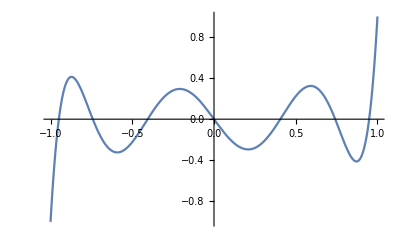

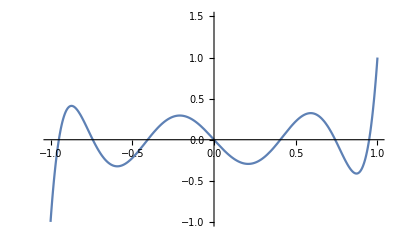

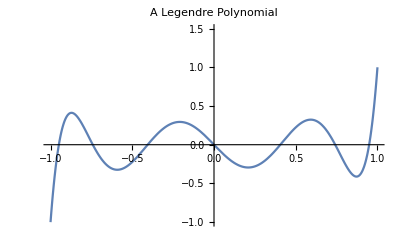

```mathematica
g0=Plot[LegendreP[7,x],{x,-1,1}]
Show[%,PlotRange->{-1,1.5}]
Show[%,PlotLabel->"A Legendre Polynomial"]
```

Wolfram 语言的所有图形都是表达式，起操控方式与其他表达式相同.这些操控不要求使用 Show.

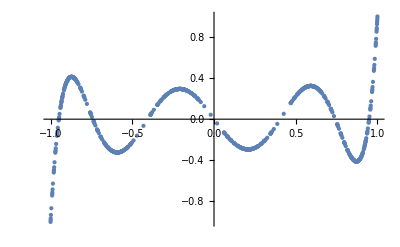

```mathematica
g0/.Line->Point
```

```mathematica
（2）组合图形
```

```mathematica
g1=Plot[x^2-9,{x,-2,5},PlotStyle->{Dashed,Red,Thick}]
g2=Plot[10Sin[x],{x,0,2Pi},PlotStyle->Yellow]
g3=Show[g1,g2]
```

```mathematica
图形范围与g1保持一致，完全显式可以修改为
```

```mathematica
g3=Show[g1,g2,PlotRange->All]

g4=Plot[BesselJ[0,x],{x,0,10}]
g5=Plot[BesselY[1,x],{x,1,10}]

g6=Show[g4,g5]
```

```mathematica
GraphicsGrid[{{g1,g2,g3},{g4,g5,g6}}]
GraphicsRow[{g3,g6}]
```

### 6. 二维数据绘图

ListPlot[{y1, …, yn}] 绘制点 {1, y1}, {2, y2}, ….

ListPlot[{{x1, y1}, …, {xn, yn}}] 为坐标为 {xi, yi} 的点生成二维散点图.

ListPlot[数据, Joined -> True] 画一条通过数据点的折线

ListLinePlot[{{xl，yl}，{x2，y2}，…}] 按选项连接数据点

List PolarPlot[data] 在极坐标系下画离散点列 data

```mathematica
y=RandomReal[{-1,1},100]
```

```mathematica
ListPlot[y]
```

```mathematica
ListPlot[y,Joined->True]
```

```mathematica
ListPlot[Table[{Sin[n],Sin[2 n]},{n,50}]]
```

```mathematica
ListPlot[Table[{x,Sin[x]},{x,0,2 Pi,0.1}],Filling->Axis,PlotLegends->{"Sin x"}]
```

```mathematica
ListPlot[Labeled[#,#]&/@Table[Prime[n],{n,10}],PlotStyle->PointSize[Medium]]
```

按顺序链接各点

```mathematica
ListLinePlot[Table[{Cos[k 2 Pi/7],Sin[k 2 Pi/7]},{k,0,21,3}],Frame->True,Axes->False]
```

```mathematica
ListPlot[Table[{Cos[k 2 Pi/7],Sin[k 2 Pi/7]},{k,0,21,3}],Joined->True,Frame->True,Axes->False]
```

## §7 .2 三维图形

### 1. 二元函数作图

Plot3D[f, {x, xmin, xmax}, {y, ymin, ymax}, 可选项] 产生函数 f 在 x 和 y 上的三维图形

Plot3D[{f1, f2, …}, {x, xmin, xmax}, {y, ymin, ymax}, 可选项] 绘制几个函数.

Plot3D[…, {x, y} ∈ reg, 可选项] 变量 {x, y} 从几何区域 reg 取值.

Plot3D[{…,w[fi],…},…] 绘制特征由符号封装 w 定义的 fi.

```mathematica
Plot3D[Sin[x+y],{x,-3,3},{y,-2,2}]
```

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2+9},{x,-2,2},{y,-2,2}]
```

```mathematica
reg=ImplicitRegion[x^2+y^2≤15,{x,y}];
Plot3D[{x^2+y^2,-x^2-y^2+9},{x,y}∈reg]
```

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2+9},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,z},x^2+y^2≤15]]
```

自变量的区域可以先定义好，也可以在Plot3D函数中用隐函数说明.

### 封裝函數

Annotation[fi, label] 为 fi 提供注解

Button[fi, action] 当点击曲线 fi 时计算 action

Callout[fi, label, pos] 把标注放在相关位置 pos

EventHandler[fi, events] 为 fi 定义一般事件句柄

Hyperlink[fi, uri] 使函数成为超链接

Labeled[fi, label, pos] 把标签放在相关位置 pos

Legended[fi, label] 在图例中标识函数

PopupWindow[fi, cont] 把弹出窗口附加在函数中

StatusArea[fi, label] 鼠标悬停时显示在状态区域

Style[fi, styles] 使用指定的样式显示函数

Tooltip[fi, label] 把提示条附加在函数上

选项                     默认值	                 说明

Axes                              True                                     是否绘制轴

BoundaryStyle         Automatic                          如何绘制曲面的边界线

BoxRatios                   {1, 1, 0.4}	                     有界 3 D box 比例

ClippingStyle            Automatic                          如何绘制曲面的剪切部分

ColorFunction          Automatic                          如何决定曲面的颜色

EvaluationMonitor  None                                    在每次函数计算时需要计算的表达式

Exclusions                  Automatic                          排除的 x、y 曲线

ExclusionsStyle        None                                    如何绘制排除曲线

Filling                           None                                    每个曲面下的填充

FillingStyle                 Opacity[0.5]                       填充使用的样式

MaxRecursion            Automatic                         递归子划分的最大数量

Mesh                             Automatic                         每个方向上绘制网格线的数量

MeshShading             None                                   如何设置网格线之间的阴影区域

MeshStyle                   Automatic                         网格线的样式

PlotLabels                  None                                   用于曲面的标签

PlotLegends               None                                   曲面的图例

PlotPoints                  Automatic                          每个方向上样本点的最初数量

PlotRange                 {Full, Full, Automatic}     包括 z 范围或其它值

PlotStyle                    Automatic                           每个曲面样式的图形指令

PlotTheme               $PlotTheme                       图的总体主题

ScalingFunctions    None                                     如何调整单独坐标

WorkingPrecision   MachinePrecision             内部计算使用的精度

(1) 去掉某些曲线上的函数图像

```mathematica
{Plot3D[x^2-y^2, {x, -5, 5}, {y, -5, 5}], Plot3D[x^2-y^2, {x, -5, 5}, {y, -5, 5}, Exclusions -> {x==0, y==0}]}
```

(2) 曲面标签

```mathematica
Plot3D[Labeled[Sin[x+Sin[y]], Sin[x+Sin[y]]], {x, -3, 3}, {y, -3,  3}]
```

```mathematica
Plot3D[ Sin[x+Sin[y]], {x, -3, 3}, {y, -3,  3}, PlotLabels->sin(x+sin y)]
```

将标签放在指定位置

```mathematica
Plot3D[Labeled[Sin[x + Sin[y]],"label", {0, 0}], {x, -3, 3}, {y, -3, 3}]
```

还可以用PlotLenged提供图例

```mathematica
Plot3D[{x^2+y^2,  4(x^2+y^2)}, {x,-5,5},{y,-5,5},RegionFunction->Function[{x,y,z},x^2+y^2≤9],PlotLegends->"Expressions"]
```

(3) 边界曲线状态设定

```mathematica
Plot3D[Sin[x y], {x, -2, 3}, {y, -2, 3}, BoundaryStyle -> Directive[Green, Thick]]
```

(4)	曲面光滑程度

```mathematica
Grid[Table[ Plot3D[Sin[x y], {x, 0, 4}, {y, 0, 4}, PlotPoints -> pp,    MaxRecursion -> mr, Mesh -> None], {mr, {1, 3}}, {pp, {5, 15, 25}}]]
```

(5)	设定曲面的样式

```mathematica
Plot3D[{Sin[x + y^2], Cos[x + y]}, {x, -2, 2}, {y, -2, 2},  PlotStyle -> {Directive[Yellow, Specularity[White, 20]],  Directive[Blue, Opacity[0.4]]}]
```

(6)	坐标轴比例

```mathematica
{Plot3D[y^2 - x^2, {x, -4, 4}, {y, -4, 4}], Plot3D[y^2 - x^2, {x, -4, 4}, {y, -4, 4}, BoxRatios -> {1, 1, 2}]}
```

(7)	动态提示条

```mathematica
Plot3D[Tooltip[Sin[x+y]], {x, -2, 2}, {y, -2, 2}]
```

(8)	曲面填充

```mathematica
Plot3D[{Sin[x+y], Sin[x+y] + 1}, {x, 0, 2 Pi}, {y, 0, 2 Pi}, Filling -> {1 -> {Bottom, Yellow}, 2 -> {Top,Blue }}]
```

（9） 增加表面的反射

```mathematica
Plot3D[Sin[x^2+y],{x,-2,2},{y,-2,2},PlotStyle->Directive[Orange,Specularity[White,40]],Mesh->None,PlotPoints->25]
```

### 2.三维参数作图

ParametricPlot3D[{fx, fy, fz}, {u, umin, umax}] 产生三维空间曲线的参数化图形.

ParametricPlot3D[{fx, fy, fz}, {u, umin, umax}, {v, vmin, vmax}] 产生三维空间曲面的参数化图形.

ParametricPlot3D[{{fx, fy, fz}, {gx, gy, gz}, …}, …] 绘制几个对象.

ParametricPlot3D[…, {u, v} ∈ reg]   从几何区域 reg 中取得参数 {u, v}.

```mathematica
ParametricPlot3D[{Sin[u], Cos[u], u/5}, {u, 0, 20}]
```

```mathematica
ParametricPlot3D[{r, Exp[-r^2 Cos[r]^2] Cos[t],  Exp[-r^2 Cos[r]^2] Sin[t]}, {r, -1, 1}, {t, 0, 2 Pi}]
```

```mathematica
ParametricPlot3D[{(8 + 3*Cos[v])*Cos[u], (8 + 3 Cos[v])*Sin[u],   7*Sin[v]}, {u, 0, 3*Pi/2}, {v, Pi/2, 2*Pi},  PlotStyle -> {LightBlue}]
```

```mathematica
ParametricPlot3D[{{4 + (3 + Cos[v]) Sin[u], 4 + (3 + Cos[v]) Cos[u], 4 + Sin[v]}, {8 + (3 + Cos[v]) Cos[u], 3 + Sin[v], 4 + (3 + Cos[v]) Sin[u]}}, {u, 0, 2 Pi}, {v, 0, 2 Pi}]
```

```mathematica
r[t_,v_]=2+0.5 v Cos[t/2];
ParametricPlot3D[{r[t,v]Cos[t],r[t,v] Sin[t],0.5 v Sin[t/2]} ,{t,0,2 Pi},{ v,-1,1}]
```

用透明度来显示隐藏的特点

```mathematica
ParametricPlot3D[{1.16^v Cos[v] (1+Cos[u]),-1.16^v Sin[v] (1+Cos[u]),-2 1.16^v (1+Sin[u])},{u,0,2 Pi},{v,-15,6},Mesh->None,PlotStyle->Opacity[0.6],PlotRange->All,PlotPoints->25]
```

### 3.球坐标作图

SphericalPlot3D[r, {θ, θmin, θmax}, {ϕ, ϕmin, ϕmax}]
生成三维球坐标图形，球体半径由特定球体坐标范围确定.

SphericalPlot3D[{r1, r2, …}, {θ, θmin, θmax}, {ϕ, ϕmin, ϕmax}]
生成多个三维球坐标图形.

```mathematica
SphericalPlot3D[ 1 + 2 Cos[2 θ], {θ, 0, Pi}, {ϕ, 0, 2 Pi}]
```

```mathematica
SphericalPlot3D[{1, 2, 3}, {θ, 0, Pi}, {ϕ, 0, 3 Pi/2}]
```

### 4.旋转面

RevolutionPlot3D[fz, {t, tmin, tmax}]  高 fz 和半径 t 生成旋转曲面图.

RevolutionPlot3D[fz, {t, tmin, tmax}, {θ, θmin, θmax}]
方位角 θ 在 θmin 和 θmax 之间变化.

RevolutionPlot3D[{fx, fz}, {t, tmin, tmax}]
通过绕 z 轴旋转 x, z 坐标 {fx, fz} 的参数曲线生成曲面.

RevolutionPlot3D[{fx, fz}, {t, tmin, tmax}, {θ, θmin, θmax}]
方位角 θ 在 θmin 到 θmax 之间变化.

RevolutionPlot3D[{fx, fy, fz}, {t, tmin, tmax}, …]
通过旋转 x、y、z 坐标 {fx, fy, fz} 的参数坐标得到曲面.

```mathematica
RevolutionPlot3D[x^3+2x-5, {x,1,3}]
```

```mathematica
RevolutionPlot3D[{2+Sin[t],Cos[t]},{t,0,2Pi},{θ, 0, 5Pi/3}]
```

```mathematica
RevolutionPlot3D[{{t,Cos[t]^2},{Sin[t],t}},{t,0,2Pi}]
```

### 5.三维数据作图

ListPlot3D[{{f11, …, f1n}, …, {fm1, …, fmn}}]
生成一个表示高度值数组 （i, j, fij） 的曲面.

ListPlot3D[{{x1, y1, f1}, …, {xk, yk, fk}}]
在 {xi, yi} 位置生成一个高度值为 fi 的曲面.

ListPlot3D[{data1, data2, …}]
绘制对应于每个 datai 的曲面.

```mathematica
data1=RandomReal[{0,5},{20,30}];
ListPlot3D[data1]
```

```mathematica
data2=Table[Sin[i+j^2], {i,0,2Pi,0.1},{j,0,2Pi,0.1}];
ListPlot3D[data2]
```

ListPointPlot3D[{{x1, y1, z1}, {x2, y2, z2}, …}] 坐标为 {xi, yi, zi} 点的三维散点图.

ListPointPlot3D[array] 绘制高度值为二维数组的点的三维散点图.

ListPointPlot3D[{data1, data2, …}] 绘制几组点，默认情况下使用不同颜色.

```mathematica
data3= Flatten[
   Table[{r Cos[t], r Sin[t], Sin[r]}, {r, 0, 10, 0.5}, {t, 0, 2 Pi, 0.1}], 1];
ListPointPlot3D[data3]
```

## §7 .4 等值线和密度图

### 1. 二元函数等值线

ContourPlot[f, {x, xmin, xmax}, {y, ymin, ymax}]
生成关于 x 和 y 的函数 f 的等高线图.

ContourPlot[f == g, {x, xmin, xmax}, {y, ymin, ymax}]
绘制 f = g 的等高线.

ContourPlot[{f1 == g1, f2 == g2, …}, {x, xmin, xmax}, {y, ymin, ymax}]
绘制多个等高线.

ContourPlot[…, {x, y} ∈ reg]
将变量 {x, y} 选在几何区域 reg 中.

说明：(1)ContourPlot 亦称为等值线、等位线、等值集 (level set) 或下等值集 (sublevel set).当给定函数 f 时，ContourPlot 构建对应于等值集 （其中 f[x, y] 具有恒定的值 c1、c2 等） 的等值线.
(2) 默认情况下，等值线之间的区域被以有利于识别数值位于 ci 和 ci + 1 之间的区域的方式着色.
 (3)当给定方程 f == g 时，ContourPlot 显示满足方程的 {x, y} 曲线. 不对区域进行着色；来自多个方程的曲线可以以任意方式相交，着色因此变得毫无意义. 它可视化的是集合 .

选项	                     默认值	                    说明
AspectRatio                  1	                             高宽比
BoundaryStyle            None                          如何绘制 RegionFunction 边界
BoxRatios                     Automatic                有效的三维边界框比率
ClippingStyle               None                          如何绘制 PlotRange 剪切的值
ColorFunction             Automatic                 如何对等高线之间的区域着色
ContourLabels            Automatic                 如何标记等高线的层次
Contours                       Automatic                  要用多少个等高线或哪几个等高线
ContourShading         Automatic                  如何设置等高线之间的阴影
ContourStyle               Automatic                  等高线的样式
Exclusions                    Automatic                  排除的 x, y 曲线
ExclusionsStyle          None                           如何在排除曲线处绘制
Frame                           True                             是否在图形周围绘制边框
FrameTicks                 Automatic                   边框刻度标记
LightingAngle             None                            模拟光源的有效角度
PlotLegends               None                            等高线区域的图例
PlotPoints                   Automatic                   每个方向上样本点数的初始值
PlotRange             {Full, Full, Automatic}     要包括的 f 或其它值的范围

设定图例

```mathematica
ContourPlot[Sin[x]*Cos[y], {x, 0, 4 Pi}, {y, 0, 4 Pi}, PlotLegends -> Automatic]
```

设定颜色

```mathematica
ContourPlot[Sin[x y], {x, 0, 3}, {y, 0, 3},  ColorFunction -> "Rainbow"]
```

标注等值线

```mathematica
ContourPlot[Sin[x^2 + y], {x, -1, 1}, {y, -1, 1}, ContourLabels -> True]
```

设定等值线样式

```mathematica
ContourPlot[Sin[x +y^2], {x, 0, 3}, {y, 0, 3},  ContourStyle -> {Red, Directive[Red, Dashed]}, PlotLegends -> Automatic]
```

```mathematica
Table[ContourPlot[Re[f[x + I y]], {x, -Pi, Pi}, {y, -Pi, Pi}, 
  PlotLabel -> f, 
  ColorFunction -> "Rainbow"], {f, {ArcSin, ArcCos, ArcCsc, ArcSec, 
   ArcTan, ArcCot}}]
```

可以画隐函数表示的曲线

```mathematica
ContourPlot[x^4+y^2-3x^2+9x==0, {x,-4,4},{y,-6,6}]
ContourPlot[{Abs[Sin[x+y^2]] == 0.5,  Abs[Cos[x+y^2]] == 0.5}, {x, -3, 3}, {y, -3, 3},  PlotLegends -> "Expressions"]
```

### 2. 三元函数等值面

ContourPlot3D[f, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]
生成关于 x、y 和 z 的函数 f 的三维等高图.

ContourPlot3D[f == g, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]
绘制f = g  的等值面.

ContourPlot3D[…, {x, y, z} ∈ reg]   将变量 {x, y, z} 置于几何区域 reg 中.

```mathematica
ContourPlot3D[x^3 + 2 y^2 - z^2, {x, -5, 5}, {y, -5, 5}, {z, -5, 5},Contours->6]
```

```mathematica
ContourPlot3D[
 x^4 + y^4 + z^4 + 2 (x^2 + y^2 + z^2)^2 - 3 (x^2 + y^2 + z^2) == 3, {x, -2, 2}, {y, -2, 2}, {z, -2, 2}, Mesh -> None,  ContourStyle -> Directive[Orange, Opacity[0.8], Specularity[White, 30]]]
```

```mathematica
ContourPlot3D[ x^2 + y^2 - z^2 == 1, {x, -2, 2}, {y, -2, 2}, {z, -2, 2},  AxesEdge -> {{-1, -1}, {1, -1}, {-1, -1}}, Ticks -> None,  AxesLabel -> {x, y, z}, PlotLabel -> x^2 + y^2 - z^2 == 1,  ColorFunction -> Function[{x, y, z, f}, ColorData["Rainbow"][z]] ]
```

```mathematica
ContourPlot3D[x^2 + y^2 + z^2, {x, -1, 1}, {y, -1, 1}, {z, -1, 1}, ContourStyle -> Opacity[0.5], Mesh -> None,  ColorFunction -> (Hue[#4/4] &)]
```

### 3. 数据等值线图

ListContourPlot[{{f11, …, f1n}, …, {fm1, …, fmn}}] 根据值 fij 的数组生成等高线图.

ListContourPlot[{{x1, y1, f1}, …, {xk, yk, fk}}] 根据点 {xi, yi} 指定的值fi生成等高线.

```mathematica
Table[ListContourPlot[RandomReal[1, {10, 10}],   InterpolationOrder -> k, 
  PlotLegends -> Automatic], {k, {0, 1, 2, 3}}]
```

```mathematica
data2 = Table[ With[{r = RandomReal[{0, 3}], t = RandomReal[{0, 2 Pi}]}, {r Cos[t], r Sin[t],  Sin[r^2]}], {10^4}];
ListDensityPlot[data2, PlotRange -> All]
```

### 4. 二元函数密度图

DensityPlot[f, {x, xmin, xmax}, {y, ymin, ymax}]  绘制函数 f 的密度图.

DensityPlot[f, {x, y} ∈ reg]  令变量 {x, y} 在几何区域 reg 中.

```mathematica
DensityPlot[Sin[i]+Cos[j],{i,-16,16},{j,-16,16},ColorFunction->Hue]

{DensityPlot[Sin[x+y]Cos[x y],{x,-3Pi,3Pi},{y,-3Pi,3Pi}], ContourPlot[Sin[x+y]Cos[x y],{x,-3Pi,3Pi},{y,-3Pi,3Pi}]}
```

```mathematica
DensityPlot[Sin[x y], {x, 0, 3}, {y, 0, 3},  ColorFunction -> "SouthwestColors", PlotPoints -> 35,  PlotLegends -> Automatic]
```

```mathematica
InverseTrigFunctions={ArcSin,ArcCos,ArcSec,ArcCsc,ArcTan,ArcCot };
Table[DensityPlot[Re[f[(x+I y)^3]],{x,-2,2},{y,-2,2},ColorFunction->"Pastel",ExclusionsStyle->{None,Purple},Mesh->None,PlotLabel->Im[f[(x+I y)^3]],Ticks->None],{f, InverseTrigFunctions}]
```

## §7 .5 用图元作图

### 1. 二维图形元素作图

Graphics[primitives, options]  表示一个二维图形.

二维图形元素有

AASTriangle[α, β, a]       角边角三角形

Arrow[{{x1, y1}, …}]	箭头

ASATriangle[α, c, β]       角边角三角形

BezierCurve[{pt1, pt2, …}]	Bézier 曲线

BSplineCurve[{pt1, pt2, …}]	B 样条曲线

Circle[{x, y}, r]         圆

Circumsphere[{pt1, …}]	由三个点指定的外接圆

ConicHullRegion[…]	线性椎体

Disk[{x, y}, r]填充圆盘

FilledCurve[{seg1, seg2, …}]	填充曲线

GraphicsComplex[pts, prims]	图形对象的复合体

GraphicsGroup[{g1, g2, …}]	可作为群组选择的对象

HalfLine[{pt1, pt2}]    半无限长的直线，或称射线

HalfPlane[{pt1, pt2}, v]	半无限平面

InfiniteLine[{pt1, pt2}]	无限长直线

Inset[obj, …]    插入对象

JoinedCurve[{seg1, seg2, …}]	连接的曲线段

Line[{pt1, …}]线段

Locator[{x, y}]   动态定位器

Parallelogram[pt, {v1, v2}]	平行四边形

Point[{x, y}]       点

Polygon[{pt1, …}]     多边形

Raster[array]     灰色或颜色方块的数组

Rectangle[{xmin, ymin}, {xmax, ymax}]	矩形

SASTriangle[a, γ, b]    边角边三角形

Simplex[{pt1, …}]  单纯形

SSSTriangle[a, b, c]    边边边三角形

Text[expr, {x, y}]   文本

Triangle[{pt1, …}]    三角形

```mathematica
图形指令可选项
```

AbsoluteDashing[{w1, …}]      指定绝对虚线

AbsolutePointSize[d]               指定绝对点的尺寸

AbsoluteThickness[w]             指定绝对线宽

Arrowheads[specs]                   指定箭头

CapForm[type]                           线帽指定

CMYKColor[c, m, y, k]               指定颜色

Dashing[{w1, …}]                       指定虚线

Directive[g1, g2, …]                   复合图形指令

EdgeForm[g]                               指定绘制边

FaceForm[g]                                指定绘制面

GrayLevel[i]                                 灰度指定

Hue[h]                                            色调指定

JoinForm[type]                          线连接指定

Opacity[a]                                     透明度指定

PointSize[d]                                 点尺寸指定

RGBColor[r, g, b]                        颜色指定

Texture[obj]                                纹理指定

Thickness[w]                               线宽指定

图形指令通常作用于之后所有图形，只对应一个图元的指令应与图元函数放在一个大括号中. 指令可以指定面的颜色和透明度, 颜色、粗细和虚线指令会影响线条、箭头和边.

(1) 带箭头折线

```mathematica
tab = Table[{n, (-1)^n}, {n, 6}];
Graphics[{Thick, Red, Line[tab], Arrow[{{5, -1}, {6, 1}}]},  Background -> None, Axes -> True]
```

(2)	正五角星

```mathematica
v=Table[ {Cos[t+Pi/2],Sin[t+Pi/2]},{t,0,2 Pi,2 Pi/5}]
Graphics[GraphicsComplex[v,{Point[{1,2,3,4,5,6}],Red,Thick,Line[{1,3,5,2,4,1}]}]]
```

GraphicsComplex[{pt1, pt2, …}, primitives] 实际上用相应的数据 pti 替换坐标整数 i.

在 Graphics 和 Graphics3D 中，GraphicsComplex 视为一个单一的图形基元. data 可以是图形基元和指令的任意嵌套列表.

```mathematica
v = {{1, 0}, {0, 1}, {-1, 0}, {0, -1}}
{Graphics[GraphicsComplex[v, Polygon[{1, 3, 4, 2, 1}]]], 
 Graphics[GraphicsComplex[v, Line[{2, 3, 1, 4}]]]}
```

(3)	圆与圆盘

```mathematica
Graphics[{Circle[{0, 0}, 2], Circle[{1, 1}, 2, {-Pi/3, 3 Pi/4}], Line[{{1, 1}, {1 + 2 Cos[-Pi/3], 1 + 2 Sin[-Pi/3]}}], Line[{{1, 1}, {1 + 2 Cos[3 Pi/4], 1 + 2 Sin[3 Pi/4]}}]},  Axes -> True]

Graphics[{Yellow, Disk[], {Green, Disk[{1, 0}]}, EdgeForm[Dashed], Disk[{2, 0}]}]
```

(4) 图像画在圆盘中

```mathematica
Graphics[{LightGray, Disk[], Inset[Plot[Tan[x], {x, -3, 3}]]}, 
 ImageSize -> Small]
```

(5) 格式设定例子

```mathematica
Graphics[Circle[], Axes -> True, AxesStyle -> {Directive[Dashed, Red], Blue}]
```

```mathematica
Graphics[Circle[], Axes -> True, GridLines -> Automatic,  GridLinesStyle -> Directive[Red, Dotted]]
```

```mathematica
Graphics[ Table[{Hue[t/20], Circle[{Cos[2 Pi t/20], Sin[2 Pi t/20]}]}, {t, 20}]]
```

(6) 用栅格作为背景

```mathematica
r = Raster[ Table[{i, j}, {i, 20}, {j, 20}], {Scaled[{0, 0}], Scaled[{1, 1}]}, {1, 20}];
Plot[{Sin[x], Cos[x]}, {x, 0, 10}, Prolog -> r, PlotStyle -> Thick]
```

### 2. 三维图元作图

Graphics3D[primitives, options]

Arrow[{pt1, pt2}]箭头

Ball[{x, y, z}, …]填充球

Cone[{pt1, pt2}, r]填充锥体

Cube[{x, y, z}, …]填充的立方体

Cuboid[{xmin, ymin, zmin}, …]填充立方体

Cylinder[{{x1, x2, x3}, …}, …]填充圆柱体

Dodecahedron[{x, y, z}, …]填充十二面体

GraphicsComplex[pts, prims]图形对象的复合体

GraphicsGroup[{g1, g2, …}]被视为群组的对象

Hexahedron[{pt1, …}]填充六面体

Icosahedron[{x, y, z}, …]填充二十面体

InfinitePlane[{pt1, pt2, pt2}]无限平面

Inset[obj, …]插入对象

JoinedCurve[{seg1, seg2, …}]连接的曲线段

Line[{pt1, …}]直线

Octahedron[{x, y, z}, …]填充八面体

Point[{x, y, z}]点

Polygon[{pt1, …}]多边形

Polyhedron[{pt1, …}]多面体

Prism[{pt1, …}]棱柱

Pyramid[{pt1, …}]棱锥

Raster3D[array]由灰色或彩色单元组成的三维数组

Sphere[{x, y, z}, …]球体

Text[expr, {x, y, z}]文本

Tube[{pt1, …}]管

（1）	多面体

```mathematica
Table[Graphics3D[{LightBlue, Opacity[.8],   PolyhedronData[p, "GraphicsComplex"]}], {p, {"Dodecahedron",   "Icosahedron", "TruncatedIcosahedron"}}]
```

(2)图形组合

```mathematica
Graphics3D[{Blue, Cylinder[], Red, Sphere[{0, 0, 2}], Green,   Opacity[.3], Cuboid[{-2, -2, -2}, {2, 2, -1}]}]
```

(3)根据顶点坐标画多面体

```mathematica
v = {{-1/2, -1/2, 0}, {-1/2, 1/2, 0}, {0, 0, -(1/Sqrt[2])}, {0, 0, 1/Sqrt[2]}, {1/2, -1/2, 0}, {1/2, 1/2, 0}};
Graphics3D[ GraphicsComplex[v, Polygon[{{4, 5, 6}, {4, 6, 2}, {4, 2, 1}, {4, 1, 5}, {5, 1, 3}, {5, 3, 6}, {3, 1, 2}, {6, 3, 2}}]]]
```

(4)	样式设定

```mathematica
Table[Graphics3D[{Blue, Specularity[White, n], Sphere[]}], {n, {5, 20, 100}}]
```

边界曲线设定

```mathematica
{Graphics3D[Cylinder[]], Graphics3D[{EdgeForm[Thick], Cylinder[]}],  Graphics3D[{EdgeForm[Directive[Thick, Dashed, Blue]], Cylinder[]}]}
```

表面样式

```mathematica
Graphics3D[{FaceForm[Yellow, Blue], Cuboid[]}, PlotRange -> {{-1/4, 5/4}, {1/4, 5/4}, {-1/4, 5/4}}]
```

## §7 .6 特殊作图命令

### 1. 根据数据作图

(1) 柱形图 与直方图

柱状图比较数据的大小, X轴为分类数据。柱状图上的每根柱子是可以随意排序的，有的情况下需要按照分类数据的名称排列，有的则需要按照数值的大小排列. 柱状图柱子的宽度因为没有数值含义，所以宽度必须一致.

  直方图展示数据的分布， X轴为定量数据，因此，直方图上的每根柱子都是不可移动的，X轴上的区间是连续的、固定的。柱子宽度可不一,  在直方图中，柱子的宽度代表了区间的长度，根据区间的不同，柱子的宽度可以不同，但理论上应为单位长度的倍数。

BarChart[{y1, y2, …, yn}]         条形图，其中条形长度为 y1、y2、….

BarChart[{…, wi[yi, …], …, wj[yj, …], …}] 条形特征由符号封装 wk 定义.

BarChart[{data1, data2, …}]   从多个数据集 datai 得到一个条形图.

```mathematica
BarChart[{{3, 1, 2}, {2.5, 3, 4}, {1, 2}}, ChartLegends -> Automatic]
```

```mathematica
BarChart[Range[8], ChartStyle -> "DarkRainbow"]
```

非实数数据被认为是缺失的，通常在条形图中产生一个空隙

```mathematica
BarChart[{{1, Missing[], 3}, {4, 2, 1 + I, 2}, {foo, 2, 4}}]
```

数据可以含有单位，或转换成指定单位

```mathematica
BarChart[{Quantity[1, "Meters"], Quantity[1, "Meters"], 
  Quantity[2, "Meters"], Quantity[3, "Meters"], Quantity[5, "Meters"],
   Quantity[8, "Meters"]}, AxesLabel -> Automatic, 
 TargetUnits -> "Feet"]
```

Histogram[{x1, x2, …}]                      绘制值 xi 的直方图.

Histogram[{x1, x2, …}, bspec]           绘制组距规范为 bspec 的直方图.

Histogram[{x1, x2, …}, bspec, hspec] 根据规范 hspec 计算直方条的高度.

Histogram[{data1, data2, …}, …]   绘制多个数据集 datai 的直方图.

```mathematica
data1 = RandomVariate[NormalDistribution[0, 1], 500];
data2 = RandomVariate[NormalDistribution[4, 2], 500];
```

```mathematica
Histogram[{data1, data2}]
```

```mathematica
Histogram[data1, 15]    指定组数
```

```mathematica
Histogram[data1, {0.25}] 指定组距
```

```mathematica
Histogram[data2, {{1, 2, 3, 4, 5 , 6, 7}}]
```

以显式列表形式指定分组界限

```mathematica
Histogram[data2, {0, 9, 0.5}] 按步长分组
```

使用不同的高度规范

```mathematica
data = RandomVariate[NormalDistribution[0, 1], 200];
Table[Histogram[data, Automatic, h,   PlotLabel -> h], {h, {"Count", "Probability", "PDF",    "CumulativeCount", "CDF", "SF"}}]
```

在上方标注数据

```mathematica
Histogram[RandomVariate[NormalDistribution[0, 1], 500],  LabelingFunction -> Above]
```

控制直方条的原点

```mathematica
Table[Histogram[RandomVariate[NormalDistribution[0, 1], 200],   BarOrigin -> o, PlotLabel -> o,   Ticks -> None], {o, {Bottom, Left, Top, Right}}]
```

### （2） 饼图和扇形图

PieChart[{y1, y2, …, yn}] 绘制一个饼图，其扇区角度与 y1、y2、… 成比例.

PieChart[{data1, data2, …}] 根据多个数据集 datai 绘制饼图.

PieChart3D[{data1, data2, …}] 根据多个数据集 datai 绘制一个三维饼图.

SectorOrigin选项，指定扇形的开始位置.

```mathematica
PieChart[{1, 2, 3, 4}]
```

```mathematica
PieChart[{{2, 2, 3}, {1,3,2}}]
```

```mathematica
PieChart[{{2, 2, 3}, {1,3,2}}, ChartLayout -> "Stacked"]
```

```mathematica
PieChart3D[{{1, 2, 3, 4}, {1, 1, 1}}]
```

SectionOrigin -> {{pos, sense}, r} 指定扇形应有内部半径 r, pos指定第一个扇形位置， sense = 1 逆时针， sense = -1 顺时针

```mathematica
Table[PieChart[{1, 2, 3}, 
  SectorOrigin -> {{k, -1}, r}], {r, {1, 2}}, {k, {0, Pi/2, Pi}}]
```

添加标签 图例

```mathematica
PieChart[{{1, 2, 3}, {2, 1}}, ChartLabels -> {"a", "b", "c"}]
```

```mathematica
PieChart[{{1, 2, 3}, {1, 2, 2, 1}}, ChartLegends -> {"a", "b", "c"}]
```

SectorChart[{{x1, y1}, {x1, y2}, …}]
制作一个扇形图表，其扇形角和 xi 成比例，并且有半径 yi.

SectorChart[{data1, data2, …}] 绘制多个数据集 datai 的一个扇形图表.

```mathematica
SectorChart[{{1, 1}, {1, 2}, {1, 3}}]
```

```mathematica
SectorChart[{{1, 1}, {1, 2}, {1, 3}}, SectorOrigin -> {Automatic, 1}]
```

```mathematica
SectorChart[{{{1, 1}, {2, 2}, {3, 3}}, {{7, 3}, {5, 2}, {3, 1}}}]
```

```mathematica
SectorChart[{{1, 1}, {1, 2}, {1, 3}}, ChartLabels -> {"a", "b", "c"}]
```

```mathematica
SectorChart[RandomReal[10, {10, 300, 2}],  ColorFunction -> "DeepSeaColors", PerformanceGoal -> "Speed",  ChartStyle -> EdgeForm[None]]
```

### 2. 画区域图

RegionPlot[pred, {x, xmin, xmax}, {y, ymin, ymax}] 画图来显示 pred 是 True 的区域.

RegionPlot[{pred1, pred2, …}, …] 绘制几个与 predi 对应的区域.
  pred 可表述为任何不等式的逻辑组合.

```mathematica
RegionPlot[x^2 + y^2 < 2 && x + y < 1, {x, -2, 2}, {y, -2, 2},  Axes -> True]
```

```mathematica
RegionPlot[{Sin[x] Sin[y] > 0.3, Cos[x] Cos[y] > 0.3}, {x, -5,   5}, {y, -5, 5}, PlotLegends -> "Expressions"]
```

```mathematica
RegionPlot[1 < x^2 + y^2 < 4, {x, -2, 2}, {y, -2, 2}, Mesh -> 8,  MeshStyle -> Directive[Red, Dashed]]
```

```mathematica
RegionPlot3D[{x + y + z < -2, x + y + z > 2}, {x, -2, 2}, {y, -2,   2}, {z, -2, 2}]
```

```mathematica
RegionPlot3D[ x^2 + y^2 + z^2 < 1 && x^2 + y^2 < z^2, {x, -1, 1}, {y, -1,   1}, {z, -1, 1}, PlotPoints -> 35, PlotRange -> All]
```

### 3. 向量图和流量图

VectorPlot[{vx, vy}, {x, xmin, xmax}, {y, ymin, ymax}]
生成以 x 和 y 的函数表示的矢量场 {vx, vy} 的矢量图.

VectorPlot[{{vx, vy}, {wx, wy}, …}, {x, xmin, xmax}, {y, ymin, ymax}]绘制多个矢量场.

VectorPlot[…, {x, y} ∈ reg] 令变量 {x, y} 位于几何区域 reg 内.

VectorPlot3D[{vx, vy, vz}, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]
生成以 x、y 和 z 的函数表示的矢量场 {vx, vy, vz} 的矢量图

VectorPlot3D[{field1, field2, …}, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]
绘制多个矢量图.

VectorPlot3D[…, {x, y, z} ∈ reg] 将变量 {x, y, z} 置于几何区域 reg 中.

例题

```mathematica
VectorPlot[{{x+y,y-x},{y,x+y}},{x,-3,3},{y,-3,3}]
{VectorPlot[{x, y}, {x, -3, 3}, {y, -3, 3}],VectorPlot[{y, -x}, {x, -3, 3}, {y, -3, 3}]}
```

```mathematica
VectorPlot[Evaluate[D[Cos[x +y],{{x,y}}]],{x,0,1},{y,0,1}]
```

```mathematica
VectorPlot3D[{z, x, x + y}, {x, -1, 1}, {y, -1, 1}, {z, -1, 1}]
```

选项

```mathematica
Table[VectorPlot[{Sin[y], -Cos[x]}, {x, -2, 2}, {y, -2, 2},   PlotLabel -> k,   VectorPoints -> k], {k, {5, Coarse, Automatic, Fine}}]
```

```mathematica
reg=MeshRegion[{{0,0},{5,-4},{2,0},{5,4}},Polygon[{1,2,3,4}]];
VectorPlot[{Sin[x+y],Cos[x y]},{x,y}∈reg, VectorPoints -> 30]
```

设定颜色

```mathematica
VectorPlot[{y, -x }, {x, -3, 3}, {y, -3, 3}, VectorScale -> Large,  VectorColorFunction -> "Rainbow"]
```

向量标记

```mathematica
VectorPlot[{{-1 - x^2 + y,  1 + x - y^2}, {-(1 + x - y^2), -1 - x^2 + y}}, {x, -3, 3}, {y, -3,   3}, VectorColorFunction -> None,  VectorStyle -> {{Orange, "Drop"}, {Blue, "Dart"}}]
```

组合图形

```mathematica
pts = Tuples[Range[-3, 3], 2];
VectorPlot[{-Sin[y], Cos[x]}, {x, -3, 3}, {y, -3, 3},  VectorMarkers -> Placed["Arrow", "Start"], VectorPoints -> pts,  Epilog -> {AbsolutePointSize[5], Black, Point[pts]}]
```

StreamPlot[{vx, vy}, {x, xmin, xmax}, {y, ymin, ymax}]
生成以 x 和 y 的函数表示的矢量场 {vx, vy} 的流线图.

StreamPlot[{{vx, vy}, {wx, wy}, …}, {x, xmin, xmax}, {y, ymin, ymax}]
绘制多个矢量场.

StreamPlot[…, {x, y} ∈ reg] 认为变量 {x, y} 位于几何区域 reg 中.

```mathematica
StreamPlot[{-1 - x^2 + y, 1 + x - y^2}, {x, -3, 3}, {y, -3, 3}]
```

将流线可视化为不间断的线条

```mathematica
StreamPlot[{-1 - x^2 + y, 1 + x - y^2}, {x, -3, 3}, {y, -3, 3},  StreamScale -> None]
```

指定过某点的流线样式

```mathematica
StreamPlot[{-1 + x^2 + y^2, 1 + x - y^2}, {x, -3, 3}, {y, -3, 3},  StreamColorFunction -> None,  StreamPoints -> {{{{1, 0}, Red}, {{-1, -1}, Green}, Automatic}}]
```

在数字赋值之前，使用 Evaluate 对矢量场进行符号式计算

```mathematica
StreamPlot[Evaluate[D[x^2  Sin[x y], {{x, y}}]], {x, 0, 1}, {y, 0, 1}]
```

### 4. 矩阵绘图

ArrayPlot[array]  生成一个图形，图形中数组的值以离散的方形阵列表示.

（1） 在默认情况下，ArrayPlot[array] 每页从上至下顺序设置连续的 array 行，从左至右设置连续的列，类似一个表或网格的通常格式
（2） 如果 array 含有 0 和 1，则 1 显示为黑色正方形，0 显示为白色正方形.
   ArrayPlot 缺省下以灰色输出，其中 0 值显示为白色，最大正或负值显示为黑色.

```mathematica
ArrayPlot[RandomReal[1, {20,10}]]
```

```mathematica
ArrayPlot[{{1, 0, 0.5, 0.3}, {0, 1, 0, 0.23}, {1, 0, 1, 0.7}}]
```

```mathematica
ArrayPlot[Table[Sin[x] + Cos[y], {x, -40, 40}, {y, -40, 40}]]
```

指定显示的颜色

```mathematica
ArrayPlot[{{1, Blue, 0, Pink}, {0, 1, 0, Yellow}, {1, 0, 1, Red}}]
```

```mathematica
ArrayPlot[Table[If[x == y, None, 1/(x - y)], {x, -2, 2}, {y, -2, 2}],  Background -> Cyan]
```

array可以用第四章矩阵的定义

```mathematica
ArrayPlot[ SparseArray[{Band[{1, 1}] -> 1, Band[{2, 1}] -> 0.7,   Band[{3, 1}] -> 0.5}, {10, 10}], Mesh -> True]
```

MatrixPlot[m] 绘制一个可视化描述矩阵中元素值的图形.

（1） 默认情况下，MatrixPlot[m] 向下纵向连续排列 m 行，将列横向连续排列，如同格式化普通的矩阵一样.
   （2） 默认情况下，MatrixPlot 中 0 值显示为白色，而负值则是使用 （冷色系） 蓝色表示，正值用 （暖色系） 红色表示.

```mathematica
MatrixPlot[{{1, 2, 3}, {1.*^-16, 0.00001, -0.00001}, {-2, -1, -3}}]
```

```mathematica
MatrixPlot[Table[Cos[x y/150.], {x, -50, 50}, {y, -50, 50}], 
 ColorFunction -> "Rainbow"]
```

```mathematica
6.	树形图
```

TreePlot              2007 版本中引入 (6.0) | 2019 版本中被更新 (12.0) ▪ 2020 (12.1)

TreePlot[g]     产生图 g 的树图.

TreePlot[{e1, e2, …}]  产生边为 ej 的树图.

TreePlot[{…, w[ei], …}]    绘制特征由符号封装 w 定义的 ei.

TreePlot[{vi 1 -> vj 1, …}] 使用规则 vi 1 -> vj 1 指定图 g.

TreePlot[m]   产生由邻接矩阵 m 表示的树图.

TreePlot[…, v -> pos] 将根 v 放在图的位置 pos.

以下封装可以用在边ei

Annotation[ei, label]提供注释

Button[ei, action]定义当点击元素时执行的行为

EventHandler[ei, …]定义元素的一般事件句柄

Hyperlink[ei, uri]把元素作为超链接

Labeled[ei, …]显示带有标签的元素

PopupWindow[ei, cont]在元素上附加弹出窗口

StatusArea[ei, label]当鼠标悬停在元素时显示在状态区

Style[ei, opts]使用指定的样式显示元素

Tooltip[ei, label]在元素上附加任意的提示条

#### 可用选项

DataRange                      Automatic                      生成顶点坐标的范围

DirectedEdges               False                                 是否把 Rule 诠释为 DirectedEdge

EdgeLabels                     None                                边的标签和位置

EdgeLabelStyle             Automatic                       边标签使用的样式

EdgeShapeFunction    Automatic                       产生边的图形状

EdgeStyle                        Automatic                       边的样式

GraphHighlight             {}	                                       突出显示的顶点和边

GraphHighlightStyle   Automatic                       突出显示的样式

LayerSizeFunction       (1)	                       每一层允许的高度

PerformanceGoal        Automatic                       试图最优化的性能方面

PlotStyle                         Automatic                       对顶点和边的整体图形指令

PlotTheme                     Automatic                       图的整体主题

VertexCoordinates       Automatic                       顶点的坐标

VertexLabels                   None                                 顶点的标签和位置

VertexLabelStyle           Automatic                       用于顶点标签的样式

VertexShape                    Automatic                      顶点的图形形状

VertexShapeFunction   Automatic                     产生顶点的图形形状

VertexSize                         Automatic                      顶点的大小

VertexStyle                       Automatic                     顶点的样式

(1) 给出边的规则

```mathematica
TreePlot[{1 -> 5, 2 -> 0, 3 -> 5, 4 -> 2, 5 -> 1, 6 -> 2, 7 -> 3, 
  8 -> 4, 9 -> 5, 4 -> 1}, VertexLabels -> Automatic]
```

(2) 给邻接矩阵

```mathematica
TreePlot[{{0, 1, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 1}, {0, 0, 0, 1, 0,   1}, {0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}}]
```

(3) 选取不同的根结点

```mathematica
Table[TreePlot[{1 -> 4, 1 -> 6, 1 -> 8, 2 -> 6, 3 -> 6, 8 -> 3,    4 -> 5, 7 -> 8}, Automatic, root,   VertexLabels -> Automatic], {root, {3, 6, 8}}]
```

(4) 根结点不同朝向

```mathematica
Table[TreePlot[{1 -> 4, 1 -> 6, 1 -> 8, 2 -> 6, 3 -> 6, 8 -> 3,    4 -> 5, 7 -> 8}, p], {p, {Top, Left, Bottom, Right, Center}}]
```

(5) 给结点标记

```mathematica
a=Framed["数学学院"]; b="基础数学";
c="计算数学"; d="应用数学";e="金融数学";
TreePlot[{a->b,a->c,a->d,a->e},VertexLabels->Placed[Automatic,Center]]
```

(6) 边有箭头方向

```mathematica
TreePlot[{1 -> 3, 2 -> 3, 3 -> 7, 5 -> 6, 6 -> 7, 6 -> 8},  DirectedEdges -> True, VertexLabels -> Automatic]
```

(6)	绘制2叉树

```mathematica
TreePlot[KaryTree[31, 2], Center]
```

#### TreeGraph 2010 版本中引入 (8.0) | 2015 版本中被更新 (10.3)

TreeGraph[{v1, v2, …}, {u1, u2, …}] 生成一个树，其中 ui 是 vi 的前驱.

TreeGraph[{e1, e2, …}] 产生一棵边为 ej 的树.

TreeGraph[{v1, v2, …}, {e1, e2, …}] 产生一棵顶点为 vi 边为 ej 的树.

TreeGraph[{…, wi[vi, …], …}, {…, wj[ej, …], …}]
产生一棵树，其中顶点和边的属性由符号封装 wk 定义.

TreeGraph[{vi -> vj, …}] 用规则 vi -> vj 指定树.

注意，只能生成树图

```mathematica
TreeGraph[{1 -> 2, 1 -> 3,  2 -> 4, 3-> 4}]
```

### 7. 图论

Graph[{e1, e2, …}]  产生具有边 ej 的图.

Graph[{v1, v2, …}, {e1, e2, …}]   产生具有顶点 vi 和边 ej 的图.

Graph[{…, wi[vi, …], …}, {…, wj[ej, …], …}]
产生具有由符号封装 wk 定义的顶点和边属性的图.

Graph[data]    由 data 生成图.

GraphPlot[g]   产生图 g 的图线.

GraphPlot[{e1, e2, …}]      绘制边为 ei 的图.

GraphPlot[{…, w[ei], …}] 绘制带有由符号封装 w 定义的特色的 ei.

GraphPlot[{vi 1 -> vj 1, …}] 使用规则 vik -> vjk 指定图 g.

GraphPlot[m] 使用邻接矩阵 m 指定图 g.

#### 说明：

（1） Graph[…] 总是转化为具有结构 Graph[vertices, edges, …] 的优化标准形式.

（2） u 和 v 之间的一条无向边可以由 u <-> v、u <-> v、UndirectedEdge[u, v] 或者 TwoWayRule[u, v] 给出. 字符 <-> 可以输入为 Esc ue Esc.
    从 u 到 v 的标记边可以通过 u  v、u  v、UndirectedEdge[u, v, t] 或 DirectedEdge[u, v, t] 给出.
    从 u 到 v 的一条有向边可以以 u -> v、u -> v、DirectedEdge[u, v] 或者 Rule[u, v] 给出. 字符 -> 可以输入为Esc de Esc.

#### 对于顶点，支持如下标准属性：

VertexLabels    顶点的标签和标签位置

VertexCoordinates     顶点的中心坐标

VertexShape         顶点的形状

VertexSize    顶点的大小

VertexStyle     顶点的样式

VertexShapeFunction        顶点的形状渲染函数

VertexWeight                      顶点的权值

#### 对于边，支持如下标准属性：

EdgeLabels      边的标签和标签位置

EdgeStyle           边的样式

EdgeShapeFunction    边的形状渲染函数

EdgeWeight              边的权值

（1） 设定结点标识

```mathematica
a="二元函数可微"; b="二元函数连续"; c="偏导数存在";d="偏导数连续";
Graph[{a->b, a->c, d->a},VertexShapeFunction->"Rectangle",VertexSize->0.4,VertexLabels->Placed[Automatic,Center]]
```

（2） 设定边的样式

```mathematica
Table[CompleteGraph[5,   EdgeStyle -> style], {style, {_ <-> 5 -> Red, Green,    Directive[Thick, Dashed]}}]
```

（3） 用邻接矩阵画图

```mathematica
GraphPlot[{{0, 1, 1, 0}, {0, 1, 1, 1}, {0, 1, 0, 1}, {0, 0, 1, 1}}, 
 VertexLabels -> Automatic]
```

（4） 立体图

```mathematica
GraphPlot3D[RandomInteger[1, {7, 7}]]
```

## §7 .3 图形动画和声音播放

### 1. 函数动画演示

Manipulate[expr, {u, umin, umax}]
产生一个带有控件的 expr 的版本，该控件允许对 u 值进行交互式操作.

Manipulate[expr, {u, umin, umax, du}] u 值在 umin 和 umax 之间以步长 du 变化

Manipulate[expr, {{u, uinit}, umin, umax, …}] u 的初始值设置为 uinit.

Manipulate[expr, {{u, uinit, ulbl}, …}]  以 ulbl 作为 u 的控件标签.

Manipulate[expr, {u, {u1, u2, …}}] 允许 u 取离散值 u1, u2, ….

Manipulate[expr, {u, …}, {v, …}, …] 使控件可以操纵每个 u, v, ….

```mathematica
Manipulate[Plot[Sin[a* x],{x,0,2Pi}],{a,1, 5}]
Manipulate[Factor[x^n -y^n], {n, 10, 100, 1}]
```

(1) Manipulate 可用于构建有任意数量控件的交互式模型.如要控制有多个参数的模
型， 只需引入新的参数及其相应的参数规范.

```mathematica
Manipulate[ Plot[ Sin[a*x + ϕ], {x, 0, 2 Pi}], {a, 1, 5}, {ϕ, 1, 10}]
```

(2) Manipulate 可用于为参数提供离散的数值列表， 而非数值的连续范围.例如， Sin 指令可被替换为一个新参数 function, 然后可给出选择列表作为 function 的参数规范

```mathematica
Manipulate[Plot[function[a* x+ϕ],{x,0,2 Pi}],{a,1,5},{ϕ,1,10},{function,{Sin,Cos,Tan}}]
Manipulate[ Plot[function[a*x + ϕ], {x, 0, 2 Pi}], {a, 1, 5}, {ϕ, 1, 10}, {function, {Sin, Cos, Tan, Csc, Sec, Cot}}]
```

函数较多时，自动选择下拉菜单，如果你想强制Mathematica 使用某特定的控件类型， 可将 ControlType 选项设置为 Setter、 Slider、RadioButtonBar 等值

```mathematica
{Manipulate[Plot[f[x], {x, 0, 2 Pi}], {f, {Sin, Cos, Tan, Cot}}],  Manipulate[ Plot[f[x], {x, 0, 2 Pi}], {f, {Sin, Cos, Tan, Cot}, 
   ControlType -> PopupMenu}]}
```

(3) 控件添加标签 : 标签输入格式为
    {{parameter, initial value, "parameter label''}, minimum, maximum}

```mathematica
Manipulate[ Plot[Sin[2Pi a x + b], {x, 0, 6}], {{a, 2, "频率"}, 1, 4}, {{b, 0, "相位"}, 
  0, 10}]
```

```mathematica
Manipulate[Plot[Sin[f* x+ ps],{x,0,2Pi},
PlotLabel->"sin("<>ToString[f] <>" x+ "<>ToString[ps]<> ")"],
{{f,1,"frequency"},1,5,Appearance-> "Labeled"},
{{ps,1,"phase shift"},1, 6, Appearance-> "Labeled"}]
```

（4） 注意指定绘图范围

```mathematica
Manipulate[Plot[x^n Sin[x], {x, 0, 10}], {n, 1, 4}]
```

```mathematica
Manipulate[ Plot[n  x Sin[x], {x, 0, 2 Pi}, PlotRange -> {-20, 10}], {n, 1, 4}]
```

（5） 控件位置和分组

```mathematica
Manipulate[ ParametricPlot[{a1 Sin[n1 x], a2 Cos[n2 x]}, {x, 0, 20 Pi},   PlotRange -> 1, PerformanceGoal -> "Quality"],  Style["x", Bold, Medium], {{n1, 1, "Frequency"}, 1,  4}, {{a1, 1, "Amplitude"}, 0, 1}, Delimiter,  Style["y", Bold, Medium], {{n2, 5/4, "Frequency"}, 1,   4}, {{a2, 1, "Amplitude"}, 0, 1}, ControlPlacement -> Left]
```

```mathematica
Manipulate[Plot3D[Sin[a x y],{x,-2, 2},{y,-2, 2}],{a,1,5}]
```

Mathematica 的默认行为是当控件移动时最优化其行为， 然后当控件被松开时再优化其外观.这让用户和控件间有一个快速交互， 并在行为结束时给出一个好的渲染结果.但是， 如果渲染比快速交互更重要， 使用例如 PerformanceGoal 的选项可以很方便地调整其行为.

PerformanceGoal -> "Quality"

```mathematica
Manipulate[Plot3D[Sin[a x y],{x,-2, 2},{y,-2, 2}, PerformanceGoal->"Quality"],
{a,1, 5}]
```

#### Animate

Animate[expr, {u, umin, umax}]
生成一个 expr 的动画，在该动画中 u 从 umin 向 umax 连续变化.

Animate[expr, {u, umin, umax, du}] 使 u 以 du 的步长变化.

Animate[expr, {u, {u1, u2, …}}] 使 u 为不连续值 u1、u2、….

Animate[expr, {u, …}, {v, …}, …] 改变所有变量 u ， v， ….

#### 选项及 默认值

AnimationDirection      Forward                   动画的方向

AnimationRate               Automatic               使变量变化的速率

AnimationRepetitions  Infinity                      停止以前的运行次数

AnimationRunning         True                         动画是否运行

AnimationRunTime         0	                自动画上次启动运行所经过的时间

AnimationTimeIndex     Automatic             动画的时间索引，其中0为开始

AppearanceElements     Automatic            包含的控制元素

BaseStyle                            {}	                动画器的基本样式规范

DefaultDuration               5.	                以秒为单位的缺省持续时间

Deinitialization                 None                       Animate 输出被删除时计算的表达式

DisplayAllSteps                False                      是否强制显示所有不连续的步长

Exclusions                           {}	                将被排除的特定值

Initialization                       None                     首次生成输出时计算的表达式.

LabelStyle                         {}	               标签区域的样式规范

RefreshRate                       Automatic            缺省的每秒钟刷新次数

ShrinkingDelay                 Automatic            如果显示的对象变小，收缩前需要延迟多长时间

```mathematica
Animate[Plot[Sin[x + a], {x, 0, 10}], {a, 0, 5}]
```

运行后直接演示动画，除非加入选项AnimationRunning -> False

```mathematica
Table[Animate[u^2, {u, 0, 1}, AnimationRepetitions -> a, AnimationRunning -> False], {a, 1, 3}]
```

控制动画循环次数

```mathematica
Animate[Graphics[{Circle[], PointSize[0.03],    Point[{Cos[t], Sin[t]}]}], {t, 0, 2 Pi, 0.1},  AnimationRunning -> False]
```

### 2. 列表动画演示 ListAnimate

ListAnimate[{expr1, expr2, …}] 生成一个动画，其帧为连续的 expri.
   ListAnimate[list, fps] 显示每秒 fps 个帧.

```mathematica
d=Table[Plot3D[Sin[x y*t],{x,0,3},{y,0,3},PlotRange->{-1,1},Mesh->True],{t,0,3,0.1}];
```

```mathematica
ListAnimate[d]
```

```mathematica
ListAnimate[{Style["\[MathematicaIcon]", Large], "string",   Framed[x + y], Graphics[Rectangle[], ImageSize -> 20]}]
```

### 3. 声音与语言

Play[f, {t, tmin, tmax}] 以声音的波形形式播放一个函数, 它的振幅以关于时间的函数 f 给出，时间 t 位于 tmin 和 tmax 之间、并以秒为单位.

Play[{f1, f2}, {t, tmin, tmax}] 产生立体声音. 首先给出左声道.

Play[{f1, f2, …}, …] 在任意多个声道上产生声音.

```mathematica
Play[(3 + Cos[30 t])*Sin[3500 t + 2 Sin[50 t]], {t, 0, 2}]
```

```mathematica
m=512;
f[m_,t_]:=Play[{Sin[512*2^(m/12)*2 Pi*x],Sin[509*2^(m/12)*2Pi*x]},{x,0,t}];
```

```mathematica
Show[{f[0, 1], f[2, 1], f[4, 1], f[5, 1], f[7, 1], f[9, 1], f[11, 1],   f[12, 1]}]
```

Sound[primitives] 表示一个声音.

Sound[primitives, t] 指定声音持续 t.

Sound[primitives, {tmin, tmax}] 指定声音应该从时间 tmin 扩展到时间 tmax 播放.

SoundNote[pitch] 表示和指定音高相符的一个音符.

SoundNote[pitch, t] 音符持续的时间长度为 t.

SoundNote[pitch, {tmin, tmax}] 音符持续的时间间隔从 tmin 到 tmax.

SoundNote[pitch, tspec, "style"] 设置指定风格的音符.

SoundNote[pitch, tspec, "style", opts] 用指定选项渲染音符.

SoundNote[] 在默认情况下，表示用钢琴演奏的中央 C 音，演奏时长为 1 秒.

```mathematica
Sound[SoundNote["C", 1, "Violin"]]
```

```mathematica
Sound[SoundNote[{"C", "G"}, 1, "Harpsichord"]]
```

```mathematica
Sound[{SoundNote[], SoundNote[4], SoundNote[7], SoundNote[12]}]
```

```mathematica
Sound[{SoundNote["C", 0.2], SoundNote[None, 0.2],   SoundNote["G", 0.3]}]
```

```mathematica
Sound[SoundNote[#, 1, RandomChoice[{"Piano", "Cello", "Tuba"}]] & /@   RandomInteger[12, 30], 4]
```

使用函数 Sound[ Play[ ], Play[ ]， •••] 播放在一起的多个声音

```mathematica
Sound[{Play[Sin[300 t Sin[20 t]], {t, 0, 1}],   Play[Sin[2000 t], {t, 1, 2}],   Play[Sin[2000 (1 + Round[2 t, 0.1]) t], {t, 2, 4}],   Play[Sign[Sin[1000 t]], {t, 0, 1}]}]
```

Speak[expr] 播放 expr 的语音表示.

Speak["string"] 播放 "string" 中的文本.

Speak[expr] 对数学表达式、程序、图形和其它结构起作用.

Speak[HoldForm[expr]] 播放 expr 的 持有形式，并不计算表达式.

```mathematica
Speak["Mathematica在各行各业有广泛的应用"]
```

```mathematica
Speak[Sin[x]^2 + Cos[x]^2]
```

```mathematica
SpokenString[Sin[x]^2 + Cos[x]^2]
```

```mathematica
Button["press ", Speak["It is wonderful"]]
```

### 4. 图形输入输出及图形处理

文件导入 Import[sourse]
ImageConvolve[image, ker]，对图像进行滤波处理, 给出 image 与内核 ker 的卷积.

```mathematica
g=Import["ExampleData/rose.gif"]
```

```mathematica
Import["ExampleData/rose.gif", "ImageSize"]
```

```mathematica
EdgeDetect[g]
```

```mathematica
Rasterize[g, RasterSize->80]
```

文件导出 Export["file", 图形]

```mathematica
g=Plot[Sin[x] + Sin[Sqrt[2] x], {x, 0, 10}]
Export["sinplot.jpg", g]
```

# 第8章 自定义函数

## §8.1 自定义函数

### 8.1.1 定义函数

```mathematica
有关定义函数的简单形式和实例如下
```

f[x_]:=expr定义函数f(x),  x 表示变量

f[x]=expr定义指定对象f[x]的值， x 表示某一具体对象

f[x_]=.清除 f[x_]的定义

Clear[f]清除f的所有定义?f显式f的定义

例题：观察函数定义和调用

```mathematica
f[x_] := x^2
f[1 + a]
f[2 x + x^2]
f[5]
Expand[f[x + y + 1]]
```

```mathematica
g[x]=x^2
g[a]
g[3]
```

g[x]=x^2表明当特定的表达式 g[x]出现时用x^2代替.但这定义对g[a],g[3]等表达式不起作用.为了定义自变量可以用任意值代入的函数，可以通过定义模式g[x_]来实现.

用户定义函数时使用的函数名仅仅是一个符号.因此，应该确保使用的名称不以大写字母开头， 以避免与 Mathematica 的内部函数混淆.用户还应当在同一进程当中,不使用前面已用过的名称.

```mathematica
f[x_,y_]:=x+y
f[3,2]
f[3]
```

当用户使用完一个定义函数时,最好清除该函数定义.否则， 当在同一进程的后面使用同名函数用以不同的目的时， 将会遇到麻烦.用户可以用 Clear[f]清除函数或符号 f 的定义.

Mathematica 中，允许对定义的不同函数取相同的函数名，系统根据模式即调用对象判断应该调用哪个函数，对于函数名和模式都相同的函数只能有一个定义，按定义次序为准， 后面的定义覆盖前面的函数定义.

```mathematica
f[x_]:=x^2+1/;x>=0
f[x_]:=Exp[x]/;x<0
```

```mathematica
f[-3]
f[2]
Plot[f[x], {x, -2, 2}]
```

两个或多个变量的函数也可以用类似方式加以定义

```mathematica
f[x_,y_]:=x^2+Cos[y]
f[x_,x_]:=x+2x^2
f[2,3]
f[3,3]
f[u,v]+f[w,w]
```

例题：输入实数 a, b, c，输出平面 z = ax +by + c 在椭球 x^2/9+y^2/16+z^2/25=1 内的面积

```mathematica
f[a_,b_,c_]:=Sqrt[1+a^2+b^2]*NIntegrate[Boole[x^2/9+y^2/16+(a*x+b*y+c)^2/25≤1],{x,-5,5},{y,-4,4}];
```

```mathematica
f[1,2,3]
```

### 8.1.2 立即赋值与延迟赋值

Mathematica 中有两种赋值形式： lhs =rhs 和 lhs := rhs， 其主要区别是什么时候计算; 的值.

lhs=rhs 是立即赋值， 即rhs是在赋值时立即计算，

lhs :=rhs 则是延时赋值， 即赋值时并不计算 rhs ， 而是在需要lhs的值时才进行计算.

1.例题：观察立即赋值和延迟赋值的调用结果

```mathematica
dex[x_]:=Expand[(1+x)^2]
ex[x_]=Expand[(1+x)^2]
ex[y+2]
dex[y+2]
```

例题：需要立即赋值的场合

```mathematica
h[x_]:=D[Log[Sin[x]]^2,x]
h[1+a]
hd[x_]=D[Log[Sin[x]]^2,x]
hd[1+a]
Plot[h[x],{x,0,Pi}]
Plot[hd[x],{x,0,Pi}]
```

用:=定义的函数中， 调用时函数的值就会被反复计算.但在一些计算中，需要将同一组函数值使用多次， 这时就可以让 Mathematica 记住这些函数以节省时间.
f[x_]:=f[x]=rhs

例题：需要保存函数定义的情形

```mathematica
fb[1]=1;
fb[2]=1;
fb[n_]:=fb[n-1]+fb[n-2]
```

```mathematica
fb[20]//Timing
```

```mathematica
fb[n_]:=fb[n]= fb[n-1]+fb[n-2]
fb[30] // Timing
```

使用过程如下： 当调用fb时,先计算fb[n-1]+ fb[n-2],再将结果保存到 fb[n], 运算时，使用能保存已有值的函数是一个好方法, 在
计算 f[30]时，需反复递推， 如需要反复计算 f[5]多次， 故此时记住 f[5]的值下次直接找出就比反复计算要好.在记住了一些函数值时， 査找就比计算快， 但这需要占用内存， 通常当重复计算的代价很大时保存函数值，且需要保存的函数不宜太多.

3.	= 和:= 不仅用来定义函数,还用来给变量赋值,x=value 立即求 value 的值,并将其赋于 x,而 x:=value 不立即求值， 每次使用 x 时才计算其值.

例题：观察变量延迟赋值的运算情况

```mathematica
a=1;
ir=a+2;
dr:=a+2
{ir,dr}
```

```mathematica
a=3;
{ir,dr}
```

可以用延时赋值 t := rhs 来设置在不同环境下有不同值的变量， 当每次需要t的值时， 就用与 rhs有关变量的当前值来计算它的值.

### 8.1.3 保存函数定义

Save[" file" ,symbol ] 将一个符号的完整定义存人一个文件

Save[" file.94, {object ,object2,.85 }]   保存一些对象的定义

例题 将函数f ，g, h 的定义写入temp 文件

```mathematica
f[x_]:=Sin[x];
Save["temp",f]
```

```mathematica
g[x_,y_]:=x+y
h[x_]:=Integrate[l/(l+x^2),x]
Save["temp", {g ,h}]
```

```mathematica
FilePrint["temp"]
```

Save 将文件 temp 存在当前默认目录下，可用 Directory[] 査看 temp

在新打开的笔记本中可以调用保存的函数：

```mathematica
Directory[]
```

```mathematica
<<temp
f[t]
g[a,b]
h[t]
```

### 8.1.4 函数运算

1 .函数名是表达式

```mathematica
Clear[f,g]
```

```mathematica
f[x] + f[x^2] /. f -> g
InverseFunction[f][x]
ff[f_,x_]:=f[Sin[x]]+f[x+1]
ff[Exp,x]
```

2.函数的重复调用

Nest[ f ,x ,n ]   f[x] 复合n次

NestList[f,x,n]   产生列表{s,f[x],f[f[x]],f[f[f[x]]],厎

Nest[f,x,4]

NestList[Cos, 1.0, 10]

FixedPoint[ f ,x ],    将f[x]迭代到结果不变为止

FixedPointList[f,x]   产生f[x]的迭代序列{x,f[x],f[f[x]],…瓆,直到结果不变为止

```mathematica
Clear[f]
```

```mathematica
f[x_]:=(x+3/x)/2
```

```mathematica
FixedPoint[f,0.6]
```

```mathematica
NestList[f,1.0,10]
```

```mathematica
g[x_]:=Sqrt[2+x]
FixedPointList[g,1.5]
```

### 3.函数作用于列表和其他表达式

#### （1）Apply

Apply[f,{a,b,...]                   f 作用于列表 f[a,b,.85]

f@@expr 或 Apply[f,expr]        用 f 作用于表达式的顶层.

Apply[f,expr,levelspec]           f 作用于表达式的指定层.

Apply[f]                      表示 Apply的运算符形式，它可以应用于表达式.

```mathematica
Exp[{x,y,z}]
```

```mathematica
Apply[f,{x,y,z}]
f@@{x, y, z}
```

```mathematica
f@@{{a, b, c}, {x, y, z}}
```

```mathematica
Apply[f, <|1 -> a, 2 -> b, 3 -> {c}|>]
```

可以指定f 作用于列表的不同层

```mathematica
Apply[f,{{a,b,c},{d,e}},{1}]
```

```mathematica
Apply[f,{{a,b,c},{d,e}},{0,1}]
```

```mathematica
Apply[f,{{{{{a}}}}},2]
```

```mathematica
Apply[f,{{{{{a}}}}},{0,2}]
```

```mathematica
Apply[f,{{{{{a}}}}},{0,Infinity}]
```

#### （2）Map

当有一系列元素时，经常需要将一个函数分别作用于每一项中，这可以用Map来实现。

Map[f,expr] 或 f/@expr      将 f 应用到 expr 中第一层的每个元素.

Map[f,expr,level]           将 f 应用到 level 指定的 expr 的部分中.
f 作用到 expr 的第 1 层到第 n 层   level=n
f 只对 expr 的第 n 层作用 level={n}

TreeForm[expr]          按树的层次形式输岀表达式

```mathematica
Map[f,{a,b,c}]
```

```mathematica
f/@ {a, b, c }
```

```mathematica
Map[Sqrt,g[x^2,x^3]]
```

```mathematica
Map[f, a + b+ c]
```

```mathematica
TreeForm[a + b + c]
```

```mathematica
Function[x, x^2] /@ {1, 2, 3, 4}
```

```mathematica
Map[f, {{a, b}, {c, d, e}}, {2}] (*作用到第2层*)
```

```mathematica
Map[f, {{a, b}, {c, d, e}}, 2]  (*作用到第1-2层*)
```

```mathematica
Map[f, {{{{{a}}}}}, 3]
```

不论表达式的 head 为何种形式，都可使用 Map

```mathematica
TreeForm[x^2 + Sin[x+y]]
```

```mathematica
Map[f, x^2 +Sin[x+y], 2]
```

```mathematica
TreeForm[%]
```

#### (3)MapAll

MapAll[f,expr]或 f//@expr        将 f 作用到 expr 的每个子表达式上.

```mathematica
f//@{{a, b}, {c}, {{d}}}
```

```mathematica
MapAll[f, x^2 + y^2]
```

```mathematica
temp=a+b^y^z;
{Map[Sin,temp,{2}], Map[Sin,temp,{3}]}
{Map[Sin,temp,2], Map[Sin,temp,3]}
```

#### (4)MapAt

MapAt[f,expr,n] f作用于expr中位置n上的元素. 如果n为负数,从末尾开始计数.

MapAt[f,expr,{i,j,...]  将 f 作用于 expr 中位置 {i,j,厎 上的元素.

MapAt[f,expr,{{i1,j1,...},{i2,j2,...},...] 将 f 作用于expr中指定的几个位置上的元素.

```mathematica
MapAt[f, {a, b, c, d,e }, 2]
```

```mathematica
MapAt[f, {a, b, c, d,e}, {{1}, {4},{5}}]
```

```mathematica
MapAt[f, {{a, b, c}, {d, e}}, {1,2}]
```

```mathematica
MapAt[f, {{a, b, c}, {d, e}}, {All, 2}]
```

```mathematica
MapAt[f, a + b + c + d, 2]
```

```mathematica
MapAt[f, x^2 + y^2, {{1, 1}, {2, 2}}]
```

## §8.2 模式替换

### 1.模式

Mathematica 中用大量的模式来代表各类表达式， Mathematica 模式的标志是￿￿，其基本规则是代表任意表达式.例如 f[x_ ]表示形如f[ anything ]的表达式，并且将表达式 angthing 命名为 x 以便在变换规则中引用. 可以将.94_.94放到表达式的任何位置， 得到与能以任何方式填充的表达式匹配的模式。由于 Mathematica 中的许多运算可用于一类表达式，所以模式就十分有效。
模式的主要功能在于 Wolfram 语言中的许多操作不仅可以对单个表达式实现，也可以对代表某类表达式的模式进行操作.

(1)用模式给出一类表达式的变换规则：

```mathematica
f[a] + f[b] /. f[x_] -> x^2
```

(2)用模式在指定类中找出表达式的位置：

```mathematica
Position[{f[a], g[b], f[c]}, f[x_]]
```

(3)只有与模式匹配的表达式会执行操作

```mathematica
f[{a, b}] + f[a*b] /. f[{x_, y_}] -> p[x + y]
```

例题：
           f[n_]                     变量名为 n 的 f
           f[n_,m_]               变量名为 n 和 m 的 f
           x^n_                     指数为 n 的 x 的幂
           x_^n_                   任何次幂的表达式
           a_+b_                   两个表达式的和
          {a1_,a2_}             两个表达式组成的列表
          f[n_,n_]               有两个相同 变量的 f

Wolfram 语言的模式代表一类给定结构 的表达式. 当一个表达式的结构与模式的结构相同时，这个表达式就可以用在模式中. 如果数学上完全相同的两个表达式，当它们的结构不同时，也不能用同一个模式来表示.

### 2.模式命名

对象如 x_ 表示任何表达式，并将此表达式命名为 x. 
一个要点是，当使用 x_ 时，Wolfram 语言要求在特定表达式中具有 x 名的表达式是相同的.因此，f[x_,x_] 表示 f 的两个变量完全相同. 而 f[_,_] 可以表示形如 f[x,y] 的表达式，其中该表达式中的变量 x 和 y 不必相同.

```mathematica
{f[a, a], f[a, b]} /. f[x_, x_] -> p[x]
```

在 Wolfram 语言中，不仅可以对一个空位命名，而且可以对模式中的任何部分命名，

x:pattern 表示命名为 x 的模式.

在变换规则中，可以将这种机制用到模式的任何部分以便在变换规则的右端使用.
_	            任何表达式
x_              命名为 x 的任何表达式
x:pattern	     与 pattern 匹配的名为 x 的表达式

```mathematica
f[a^b] /. f[x : _^n_] -> p[x, n]
```

```mathematica
{f[g[3], g[3]], f[g[4], g[2]]} /. f[x : g[_], x_] -> r[x]  (*_ 命名为x， *)
```

### 3.寻找与模式匹配的表达式

Cases[list,form]                   给出与 form 匹配的 list 中的元素

Count[list,form]	    给出与 form 匹配的 list 中元素的个数

Position[list,form,{1}]	    给出与 form 匹配的 list 中的元素的位置

Select[list,test]                     给出使 test 的值为 True 的 list 中的元素

Pick[list,sel,form]	    给出使 sel 的相应元素与 form 匹配的 list 中的元素

```mathematica
Cases[{(1 + a)^2,   1 + 2 a + a^2, (1 + Sin[b])^2, (1 + x^3)^2, (1 + x + y)^2}, (1 + x_)^2]
Count[{3, 4, x, x^2, x^3}, x^_]
```

像 Cases 这样的函数不仅可以用于列表，而且可以用于任何表达式，可以指定项所在的层.

Cases[expr,lhs->rhs]	    在 expr 中寻找与 lhs 匹配的元素，并对其进行变换

Cases[expr,lhs->rhs,lev]    测试指定层 lev 上表达式 expr 的项

Count[expr,form,lev]	    给出指定层 lev 上与模式 form 匹配的项数

Position[expr,form,lev]	    给出指定层 lev 上与模式 form 匹配的项的位置

```mathematica
Position[{4, 4+x^a, x^b, 6+x^5}, x^_, All, 2]
```

```mathematica
Cases[{3, 4, x, x^2, x^3}, x^n_ -> n]
```

DeleteCases[expr,form]	     删除表达式 expr 中与 form 匹配的元素

DeleteCases[expr,form,lev]	 删除表达式 expr 的指定层 lev 中与 form 匹配的项

```mathematica
DeleteCases[{3, 4, x, x^2, x^3}, x^n_]
```

```mathematica
DeleteCases[{3, 4, x, 2 + x^2, 3 + 5x}, _Integer, All]
```

```mathematica
DeleteCases[{3, 4, x, 2 + x^2, 3 + 5 x}, _Integer, {2}]
```

```mathematica
TreeForm[{3,4,x,2+x^2,3+5 x}]
```

### 4.模式替换

lhs->rhs 或 lhs→rhs     表示将 lhs 转换为 rhs 的规则.

规则是一种通用的结构，可以表示表达式之间的转换、子代、对应关系和其他关系, 
可以用 Replace 等指令来应用规则,
 lhs = rhs 赋值指定无论何时都应使用规则 lhs -> rhs

以模式名称出现在 lhs 中的符号被看作规则中的局部符号.当符号出现在 lhs 中 /; 条件的右边以及 lhs 中任意位置上，甚至其它的范围结构内时，这都是成立的.

```mathematica
Sin[x] /. Sin -> Arctan
```

```mathematica
x /. {x -> 1, x -> 3, x -> 7}  (*应用第一个规则*)
```

```mathematica
x /. {{x -> 1}, {x -> 3}, {x -> 7}} (* 分别应用每个规则 *)
```

```mathematica
l + x^(1/2) + x^2 /. x^n_ -> g[m]  (*用模式把变量和匹配的部分结合在一起*)
```

```mathematica
Sin[2x]+Sin[2y z]+Sin[z]/. Sin[2x_]->2Sin[x]Cos[x]
```

```mathematica
x /. {y -> 2, z -> 3}(*如果没有相匹配的规则，则返回原来的表达式*)
```

为模式替换取名并保存到变量中， 调用更方便。

```mathematica
s=Sin[x_]->2 Sin[x/2] Cos[x/2]
```

```mathematica
Sin[2x]+Sin[2y z]+Sin[z]/.s
```

### 5. 立即变换和延迟变换

lhs->rhs  在定义规则时rhs被求值

lhs:>rhs 或 lhs  :>rhs  在定义规则时 rhs 不求值， 调用规则时才求值
（字符 :> 可以输入为 :> 或 ∖[RuleDelayed].）

```mathematica
x:>RandomReal[]
```

```mathematica
{x,x,x}/.x:>RandomReal[]
```

```mathematica
n=1;{x,x,a,b,x,x,c,d}/.x:>n++
```

```mathematica
f[x]->Expand[(1+x)^2]
g[x_]:>Expand[(1+x)^2]
```

```mathematica
f[a+b]/.f[x_]->Expand[(1+x)^2]
g[a+b]/.g[x_]:>Expand[(1+x)^2]
```

### 6. 调用规则

将模式替换应用到具体的函数定义或其他表达式中需要调用替换规则，一般有以下调用方式.

Replace[expr,rules]应用一个规则或规则列表来转换整个表达式 expr

Replace[expr,rules,level]应用规则到 expr 中由 level指定的部分

ReplaceAll[expr,rules]
Expr/.rules应用一个规则或规则列表尽可能转换一个表达式 expr 的每个子部分

ReplaceRepeated[expr,rules]
expr//.rules重复执行替换直至 expr 不再改变.

ReplaceList[expr,rules]
以所有可能的方式应用一个规则或规则列表转换整个表达式 expr，并返回取得的结果列表.

```mathematica
{x,x^2,y,z}/.x->{a,b}
```

```mathematica
ReplaceAll[{x,x^2,y,z},x->{a,b}]
```

例题：比较两种调用 /.   //.

```mathematica
rules={Log[x_ y_]:>Log[x]+Log[y],Log[x_^k_]:>k Log[x]};
```

```mathematica
Log[Sqrt[a (b c^d)^e]]/.rules
```

```mathematica
Log[Sqrt[a (b c^d)^e]]//.rules
```

```mathematica
{f[f[x]], f[x], g[f[x]], f[g[f[x]]]} //. f[x_] -> x
```

```mathematica
{f[f[x]], f[x], g[f[x]], f[g[f[x]]]}/. f[x_] -> x
```

使用 //. 算符时，应该非常小心以避免出现无限循环. 例如，命令 x//.x->x+1 就将导致一个无限循环

调用规则前是否进行计算

```mathematica
Hold[{f[f[x]], f[x], g[f[x]], f[g[f[x]]]} ] //. f[x_] :> x + x
Hold[{f[f[x]], f[x], g[f[x]], f[g[f[x]]]} ] //. f[x_] -> x + x
```

```mathematica
ReplaceList[a + b + c, x_ + y_ -> g[x, y]]
```

## §8.3 给模式附加条件

### 1. 模式中的表达式类型限制

可以通过头部来区分不同￿类型￿的表达式，如整数的头部为 Integer，而列表的头部为 List.

x_h	          具有头部 h 的表达式

x_Integer       整数型

x_Real	          实数型

x_Complex    复数型

x_List	          列表型

x_Symbol      符号型

```mathematica
{a, 4, 5, Exp[2]} /. x_Integer -> p[x]
```

```mathematica
d[x_^n_Integer]:=n x^(n-1)
```

```mathematica
d[x^4]+d[(a+b)^3]+d[x^(2.0)]
```

### 2. Mathematica中提供了对模式进行限制的一般方法.

pattern/;condition	    当条件满足时，模式才匹配

lhs:>rhs/;condition	    当条件满足时，才使用规则

lhs:=rhs/;condition	    当条件满足时，才使用定义

在 Wolfram 语言中有一类函数去测试表达式的性质. 这类函数后有一个 Q，表明它们在.93提问.94.

IntegerQ[expr]整数      EvenQ[expr]偶数

OddQ[expr]奇数          PrimeQ[expr]素数

NumberQ[expr]任何数     NumericQ[expr]数字型

PolynomialQ[expr,{x1,x2,.85}]关于 x1, x2, .85 的多项式

VectorQ[expr]表示向量的列表

MatrixQ[expr]表示矩阵的集合的列表

VectorQ[expr,NumericQ],  MatrixQ[expr,NumericQ]
所有元素都是数字的向量和矩阵VectorQ[expr,test]

MatrixQ[expr,test]对所有元素 test 的函数值都为 True 的向量和矩阵

ArrayQ[expr,d]深度与 d 匹配的完全数组

```mathematica
{2.3, 4, 7/8, a, b}/.(x_/;NumberQ[x])->x^2
```

```mathematica
mi[list_] := list^2 /; VectorQ[list, IntegerQ]
```

```mathematica
{mi[{2, 3}], mi[{2.1, 2.2}], mi[{a, b}]}
```

```mathematica
{6, -7, 3, 2, -1, -2} /. x_ /; x < 0 -> w
```

pattern/;condition 通过所涉及模式名满足的条件确定是否可以匹配.

pattern?test 通过检查函数 test 在表达式的值来确定是否可以匹配.

用 ? 比 /; 更方便.
运算符 ? 有一个高的优先级. 这样 _^_?t 是 _^(_?t)，而不是 (_^_)?t

```mathematica
p[x_?NumberQ] :=Sin[x^2]
```

```mathematica
p[4.5] + p[3/2] + p[u]
```

```mathematica
Cases[{1, 2, 3.5, x, y, 4}, _?NumberQ]
```

```mathematica
MatchQ[{1, E, Pi}, {__?Positive}]
```

Except[c]与任何非 c 表达式匹配的模式

Except[c,patt]与 patt 匹配但非 c 的模式

patt1|patt2|￿      多种形式的模式

```mathematica
Cases[{a, Sin[1], 0, 1, 2, x^2},Except[_Integer]]
```

```mathematica
{1, x, x^2, x^3, a^x} /. (x | x^_) -> q
```

```mathematica
h[a | b] := Sin[a]
```

```mathematica
Clear[f,h,g]
```

```mathematica
{h[a], h[b], h[x]}
```

## §8.4. 参数数目可变函数

1.	模式 f[x_,y_] 仅代表恰有两个变量的函数. 有时还需要建立具有任意数目的自变量的函数.这可以通过多重空位来实现. 一个空位 x_ 表示一个 Wolfram 语言表达式，两个空位 x__ 表示多个表达式.

_单一表达式
x_名为 x 的表达式
__一个或多个表达式序列
x__名为 x 的表达式列
x__h头部为 h 的表达式列
___零个或多个表达式序列
x___名为 x 的零个或多个表达式序列
x___h头部为 h 的零个或多个表达式序列

例题：定少用多

```mathematica
f[x__]:=p[x,x,x]
f[a,b,c]
```

```mathematica
g[x__]:=x+x*x
g[a,b,c,d]
```

```mathematica
h[a___,x_,b___,x_,c___]:=hh[x]*h[a,b,c]
h[2,3,2,5,3,1]
```

2.	可选变量与默认变量
有时需要定义具有默认值的函数. 即省略某些变量时，其值就用设定的默认值代替. 模式 x_:v 就表示省略时值为 v 表示的变量.

x_:v	   省略时值用 v 代替的表达式

x_h:v	   具有头部 h 和默认值 v 的表达式

x_.	   具有设定默认值的表达式

```mathematica
j[x_,y_:1,z_:2]:=E^(-x)(y^2+z^2)
j[3]
```

一些 Wolfram 语言常用函数的变量具有系统设定的默认值，此时不能明确给出 x_:v 中的默认值，而是可用 x_. 来使用其系统设定的默认值.
x_+y_.	  y 的默认值为 0
x_y_.	      y 的默认值为 1
x_^y_.	  y 的默认值为 1

利用 x_. 可以使一个模式与几个不同的表达式匹配，当需要与多个结构不同但数学形式相同的表达式匹配时这种方式特别方便.

```mathematica
{f[a], f[a + b]} /. f[x_ + y_.] -> p[x, y]
```

```mathematica
{g[a^2], g[a + b]} /. g[x_^n_] -> p[x, n]
```

```mathematica
{g[a^2], g[a + b]} /. g[x_^n_.] -> p[x, n]
```

```mathematica
lin[a_. + b_. x_, x_] := p[a, b]
```

```mathematica
lin[1 +5 x, x]
```

## §8.5 函数的属性与属性定义

1.	在 Mathematica 中不仅可以定义函数的运算规则， 还可以设置函数的属性。
函数的属性对函数的运算规则和调用时对模式匹配有直接的作用和影响

Attributes[f]	           列出赋予 f 的属性

SetAttributes[f,attr]	   给 f 赋予属性 attr

ClearAttributes[f,attr]	   清除 f 的属性 attr

```mathematica
Attributes[Plus]
Attributes[Sqrt]
```

一个符号 f 的可能属性的完整列表是：

Constant        f的所有导数为0

Flat          	f 是可结合的 f[f[a,b],c]与f[a,b,c]等价

HoldAll	        f 的所有参数都不参与运算

HoldAllComplete	f 的参数完全与运算隔离

HoldFirst     	f 的第一个参数不参与运算

HoldRest     	除第一个参数外的 f 的其它参数不参与运算

Listable	  f 自动线性作用于整个列表

Locked	        f 的属性不能被更改

NHoldAll     	f 的参数不受N 的影响

NHoldFirst	    f 的第一个参数不受 N 的影响

NHoldRest	    除第一个参数外的 f 的其它参数不受 N 的影响

NumericFunction	参数是数时，f 的值也假定为一个数

OneIdentity	    f[a]、f[f[a]]等在模型匹配中与 a 等价

Orderless	    f 可交换

Protected	    f 的值不能被更改

ReadProtected	f 的值不能被读出

SequenceHold	f 的参数中的 Sequence 对象不被展平

```mathematica
SetAttributes[q, Orderless]
```

```mathematica
q[b,a,c]
f[q[a, b], q[b, c]] /. f[q[x_, y_], q[x_, z_]] -> p[x, y, z]
```

Wolfram 语言在进行匹配时，也考虑到了可结合性，如模式 g[x_+y_] 可以和 g[a+b+c] 匹配，此时 x→a 并且 y→(b+c).

```mathematica
g[a+b+c]/.g[x_,y_]->p(x,y)
```

如果没有其他限制时，Wolfram 语言把 x_ 与和式中的第一个元素匹配：

```mathematica
g[a+b+c+d]/.g[x_,y_]->p(x,y)
Replacelist[g[a+b+c],g[x_,y_]->p(x,y)]
```

例题：满足结合律的函数

```mathematica
SetAttributes[h,Flat]
```

```mathematica
h[a,b,a,b]/.h[x_,x_]->rp[x]
```

```mathematica
h[a,b,b,c]/.h[x_,x_]->rp[x]
```

如果要增加某函数的性能，那么先要去掉保护属性。作出变换规则或定义后，再恢复内部函数的保护属性.

```mathematica
Log[a b c]
```

```mathematica
Unprotect[Log]
Log[x_ y_]:=Log[x]+Log[y]
Log[x_^n_]:=n Log[x]
Protect[Log]
```

```mathematica
Log[a b c]
```

```mathematica
Log[a^2 b^2 c^(1/3)]
```

例题：定义简单的积分函数

```mathematica
int[y_+z_,x_]:=int[y,x]+int[z,x];int[c_ y_,x_]:=c int[y,x]/;FreeQ[c,x]
```

```mathematica
int[c_,x_]:=c x/;FreeQ[c,x]
int[x_^n_.,x_]:=x^(n+1)/(n+1)/;FreeQ[n,x]&&n≠-1
int[1/(a_.x_+b_.),x_]:=Log[a x+b]/a/;FreeQ[{a,b},x]
int[Exp[a_.x_+b_.],x_]:=Exp[a x+b]/a/;FreeQ[{a,b},x]
```

```mathematica
int[a x+b x^2+3,x]
```

```mathematica
int[a x+b x^2+3,x]
```

```mathematica
int[1/(2 p x-1),x]
```

Wolfram 系统一旦运算了表达式的头部，就会查看该头部是否是具有属性的符号.
   如果符号具有 Orderless、Flat 或 Listable属性，则 Wolfram 系统在运算表达式的元素之后，将立即执行与这些属性关联的转换.

标准运算过程的下一步是将 Wolfram 系统所知道的定义用于正在运算的表达式.
   Wolfram 系统首先尝试使用您创建的定义，如果没有适用的定义，再尝试使用内置定义.
   如果 Wolfram 系统找到适用的定义，它将对表达式执行相应的转换.结果是另一个表达式.

#### 标准运算过程.

■ 运算表达式的头部.■ 依次运算每个元素.■ 应用与属性 Orderless、Listable 和 Flat 关联的转换.■ 应用您给出的定义.■ 应用内置定义.■ 运算结果.

2. 在运算过程中可以用.93Trace[expr] .94跟踪 Mathematica 计算 expr 的工作过
程。下列为计算表达式的跟踪形式：

Trace[expr] 产生计算 expr 过程中的所有表达式的一个列表.

Trace[expr, form] 仅包括匹配 form 的表达式.

Trace[expr, s] 包括所有使用和符号 s 相关联的变换规则的计算.

```mathematica
a=7;
Trace[2 a x+a^2+x^2]
```

2 ax + a^2 + x^2 内部形式  为 Plus[Times[2, a, x], Power[a, 2], Power[x^2]]

## §8 .6 纯函数

body & 或 Function[body] 是一个纯 （或￿匿名￿） 函数.形式参数是 # （或 #1）、#2等.

Function[x, body] 具有一个形式参数的纯函数

Function[{x1, x2, ...}, body]具有多个形式参数的纯函数.

Function[params, body, attrs] 是一个纯函数，在计算时被认为具有属性 attrs.

说明：

（1） 当 Function[body] 或 body & 用到参数集合上时，# （或 #1） 由第一个参数代替，#2 由第二个代替，以此类推.#0 由函数本身代替.

（2） 如果给出的参数比函数中 # i 数目更多的话，剩余的参数被忽略.

（3） ## 表示提供的所有参数的序列.## n 表示从数字 n 开始的参数.

（4） Function 有属性 HoldAll.仅在形式参数被自变量替换后计算函数体.

（5） Function 结构可以以任意方式嵌套.每种方式都可以当作作用域结构处理

（6） 在 Function[params, body, attrs] 中，attrs 可以是一个属性或属性列表.例题：纯函数定义

(1) 1 个参数

```mathematica
Function[u,Cos[u]+u Sin[u]][x]
```

```mathematica
Function[Cos[#]+# Sin[#]][x]
```

```mathematica
(Cos[#]+# Sin[#])&[x]
```

（2） 两个参数

```mathematica
Function[{u,v},u Cos[v]+Log[u+v]][x,y]
```

```mathematica
(# Cos[#2]+Log[#+#2])&[x,y]
```

```mathematica
f=(# Cos[#2]+Log[#+#2])&
f[3,2]
```

(3) 将纯函数映射到列表

```mathematica
{#,#^2}&/@{x,y,z}
```

(4) 从纯函数中创建一个矩阵

```mathematica
MatrixForm[Array[(#+#2^2&),{3,4}]]
```

(5) 按数组的第二个元素排序

```mathematica
Sort[{{a,2},{c,1},{d,3}},#1[[2]]<#2[[2]]&]
```

(6) 函数名直接运算

```mathematica
Sec'
```

Sec[#1] Tan[#1]&

(7) ## 表示所有参数

```mathematica
f[X,##,Y,##]&[a,b,c]
```

```mathematica
g[X,##2,Y,##3,Z,##4]&[a,b,c,d]
```

(8) 创建一个具有 Listable 属性的纯函数

```mathematica
Function[{u},g[u],Listable][{a,b,c}]
```

```mathematica
Function[{u},g[u]][{a,b,c}]
```

# 第9章 程序设计

在上一章中，我们用形如￿f[x_]:= expr.94的 Mathematica 语句自定义一个函数。 该语句本质上是一个表达式。 Mathematica 的程序设计实际上也就是自定义函数的过程， 只不过是表达式的繁简程度有所不同而已。 一个表达式序列也称为一个复合表达式， 序列中各表达式用分号（；） 分隔。在 Mathematica 的各种语句中， 任何一个表达式的位置都能放一个复合表达式。 运行时按照顺序依次求各表达式的值， 并以最后一个表达式的值作为整个复
合表达式的值。 如果用一个复合表达式自定义一个函数， 要将这一串表达式用圆
括号括起来，最后一个表达式的值作为函数的值。

与一般结构化程序设计语言类似， Mathematica 提供了具有条件判断结构和
循环控制结构的语句，同时也保留了转向控制语句。

## 9.1 条件语句

在程序上和数学上， Mathematica 提供了 If、 Which 和 Switch 这 3 种条件语句。 
它们常用在程序设计中， 也可用于交互式行文命令中。

### 1. If语句

If[condition,t,f]    如果 condition 计算为 True 则给出 t，若计算为 False 则给出 f.

If[condition,t,f,u]   如果 condition 既不计算为 True 也不计算为 False 则给出 u.

```mathematica
abs[x_]:=If[x<0, -x, x]
```

```mathematica
abs[{-2,0,5}]
```

```mathematica
f[x_,y_]:=If[x >0&&y >0, x +y, x -y]
```

```mathematica
f[4,-3]
```

```mathematica
f[2, u] (*无法判断真假*)
```

```mathematica
f[x_,y_]:=If[x >0&&y >0, x +y, x -y, x y]
```

```mathematica
f[2,u]
```

例题：生成50个 [0,1]内随机数，判断该随机数是否小于0.5,如果小于 0.5,则将此随机数显示出来， 否则显示￿*￿

```mathematica
Table[If[(p = RandomReal[]) < 0.5, p, "*"], {n, 50}]
```

例题：定义函数f(x)=Piecewise[{{x+Sin x, x<0}, {xSin x, 0≤x<2}, {xCos x, x≥2}}]并画出其在[-3,3]上的图形.

```mathematica
f[x_] := If[x < 0, x + Sin[x], If[x >= 2, x Cos[x], x Sin[x]]]

Plot[f[x], {x, -3, 3}]
```

### 2. Which 语句.

格式1：Which[条件1, 表达式1, 条件2, 表达式2,￿ 条件n, 表达式n,]	
功能:由条件 1 开始按顺序依次判断相应的条件是否成立， 若第一个成立的条件为条件k,则执行对应的表达式 k. 如所有条件都为假， 值为 Null， 作为整个结构的值

格式 2: Which[条件 1， 表达式 1，.85， 条件 n， 表达式 n， True, 表达式(n+1)]
功能:由条件 1 开始按顺序依次判断相应的条件是否成立， 若第一个成立的条件为条件k，则执行对应的 表达式k， 若直到条件 n 都不成立时，则返回表达式(n+1)

例题：定义分段函数 h(x)=-1 | x<-π/2
Sin x | -π/2≤x≤π/2
1 | x>π/2

```mathematica
h[x_]:= Which[x < -Pi/2, -1, x <= Pi/2, Sin[x], True, 1]
```

```mathematica
{h[-2], h[-1],h[0],h[1],h[2] , h[z]}
```

```mathematica
Plot[h[x],{x,-Pi,Pi}]
```

例题 定义函数 u(x)=Piecewise[{{-x, x<0}, {sinx, 0≤x<6}, {x/3
0, 16≤x<20
其他}}]，计算x=15,-12,5,18处的函数值.

```mathematica
u[x_]:=Which[x<0,-x,x<6,Sin[x],x<16,0,x<20,x/3,True,0]
{u[15],u[-12],u[5],u[18]}
u[x_]:=Which[x<0,-x,0<=x&&x<6,Sin[x], ,16<=x&&x<20,x/3,True,0]
```

例题：任给向量,定义一个可以计算下面三种矢量范数的函数

```mathematica
norm[x_,p_]:=Which[p==1,Sum[Abs[x][[i]],{i,1,Length[x]}], p==2, Sqrt[Sum[x[[i]]^2, {i,1,Length[x]}]], p==Infinity,Max[Abs[x]]]
Table[norm[{1, 2, 0, -5, 3}, p], {p, {1, 2, Infinity}}]
```

### 3. Switch语句

Switch[表达式，模式 1,语句 1，模式2,语句2 模式 n,语句 n ]	
先计算表达式， 然后按模式 1 ,模式 2,…的顺序依次比较与表达式结果相同的模式， 找到的第一个相同的模式，则将此模式对应的语句计算计算结果作为 Switch 语句的结果.Switch 语句是根据表达式的执行结果来选择对应的执行语句， 它类似于一般计算机语言的Case 语句•

```mathematica
r[x_] := Switch[Mod[x, 3], 0, a, 1, b, 2, c]
r[4136]
```

### 4. 其他条件语句

Mathematica 中具有条件判断和分支选择结构的函数还有 Piecewise、 Cases、Count、 Position、Select 等

Piecewise[{{val1,cond1},{val2,cond2},...]
表示一个分段函数，在定义域内的条件 condi 值为 vali.

Piecewise[{{val1,cond1},...,val]
如果没有条件 condi，则取默认值 val. val 的默认值是 0.
condi 通常是不等式，比如, 依次判断条件 condi，直到其中的一个条件为 True.如果前面提到的所有条件 condi 都为 False，则把与第一个为 True 的条件 condi 相对应的值 vali，作为分段函数的函数值返回.

```mathematica
Plot[Piecewise[{{x^2,x<0},{x^(1/2), x>=0}}],{x,-2,5}]
```

```mathematica
D[Piecewise[{{x^2,x<0},{x^(1/2), x>=0}}],x]
```

利用 pw 来输入 { ，接着使用ctrl+,ctrl+Return 输入其他分支情况：

```mathematica
f[x_]:=Piecewise[{{Sin[x], 0<x<=Pi}, {2x-2Pi, Pi<x<2Pi}, {-x, x≤0}}]
```

```mathematica
Plot[f[x],{x,-2,2Pi}]
```

## 9.2 循环语句

Mathematica 中有 3 种常用的循环语句，它们是 Do、 While 和 For 语句

### 1. Do语句

Do[expr,n]                      对 expr 计算 n 次.

Do[expr,{i,imax}]                 将变量 i 从 1 递增到 imax（步长为 1），计算 expr.

Do[expr,{i,imin,imax}]             从 i=imin 开始.

Do[expr,{i,imin,imax,di}]           使用步长 di.

Do[expr,{i,{i1,i2,...}]               使用列表中的值 i1、i2、￿

Do[expr,{i,imin,imax},{j,jmin,jmax},   对于每个 i，循环地根据不同的 j 等，计算 expr.

```mathematica
Do[Print[RandomInteger[10]],3]
Do[Print[{i,j}], {i,2},{j,2}] (*两重循环的次序*)
```

Do[expr,spec1,spec2] 实际上等价于 Do[Do[expr,spec2],spec1].

例题 找出 300 至 1000 之间同时能被 17 和 7 整除的自然数

```mathematica
Do[If[Mod[i, 17] == 0 && Mod[i, 7] == 0, Print[i]], {i, 300, 1000}]
```

例题 找出方程5 x^2+7y+z/4=150满足x+y+z<100的正整数解.

```mathematica
Do[z= 4 (150 - 5 x^2 - 7 y);  If[x+y+z<100&&z>0,   Print["x=", x, "  y=", y, "  z=", z]], {x, 1, 100}, {y, 1, 100}]
```

例题:用牛顿迭代法计算 √11

```mathematica
x = 5.0; Do[x = (x + 11/x)/2, 10]; x
```

例题 数值排序（选择排序法）

```mathematica
list = RandomSample[Range[10], 10]
Do[If[list[[i]] > list[[j]], list[[{i, j}]] = list[[{j, i}]]], {i, Length[list]}, {j, i + 1, Length[list]}]; list
```

### 2. While 语句

While[test,body]若 test=True，运算循环体 body，直到 test=False退出循环.

例题：用割线法求解方程x^3 - 2 x^2 + 7 x + 4 = 0 的根,要求误差| x_k-x_(k- 1) |< 10^-12， 割线法的公式是 x_(k+1)=x_k-(f(x_k)(x_k-x_(k-1)))/(f(x_k)-f(x_(k-1))),    x_0=-1, x_1=1

```mathematica
f[x_]:=x^3-2x^2+7x+4;
x0=-1;x1=1;
While[Abs[x0-x1]>10^(-12),x2=x1-(x1-x0) f[x1]/(f[x1]-f[x0]);x0=x1;x1=x2]
N[x1,12]
```

### 3. For循环语句

For[start,test,incr,body]
以 start为初值，然后重复计算 body 和 incr，直到 test 不能给出 True.  incr为循环变量修正，body为循环体。
先计算初值，接下来计算的序列是 test、body、incr. 只要 test 失败立即退出 For 循环。在使用 For 语句编写程序的过程中， 一定要注意 For 语句的用法， Mathematica 中的 For 和 While 和 C 语言中的 For 和 While 的工作方式大致相同， 但逗号和分号的作用在 Mathematica 中和在 C 语言中正好相反，用逗号作为 For 的各个部分的分隔符，用分号作为程序各个部分的分隔符。

例如：求 1+2+…+100

```mathematica
For[ s =0;n =l, n <=100, n++,  s+=n];  s
```

```mathematica
For[s =0;n =l, n <=100 ,n++; s+=n]; s (* 错误的程序 *)
```

```mathematica
For[ s =0,n = l, n <=100；n++, s+=n];s (* 错误的程序 *)
```

例题 编制 10 以内整数加法自测程序
用随机函数 Random[ Integer , {0, 10}] 产生[0 ,10] 内的任意两个整数 s 和 t, 屏幕提示算式 t + s = , 用户键入一个计算结果y, 如果结 果正确 , 显示“真棒！” , 否 则 显示“请再算一次” , 等 待重 新 输入 , 直到 结果正确 , 每次给出 10 个算式

```mathematica
For[i=1, i<=3, i++ , 
t = Random[Integer, {0, 10}]; s = Random[Integer, {0, 10}];
  Print[t, "+", s, "="];
 y = Input[]; While[y != t + s, Print[t, "+", s, "=", y, "请再算一次"];
  Print[t, "+", s, "="]; y = Input[]];
 Print[t, "+", s, "=", y, "真棒"]]
```

注意：While、For语句中没有隐含的局部变量。

```mathematica
n=100;For[n=E,n<=10,n+=Pi,Print[n]]; n
```

特殊赋值语句

语句说明x++, x--在使用 x 的数值后 x+1（x-1）赋值给x

++x,--x在使用 x 前将 x 增(减)1

x+=y, x-=y, (x=x+y,   x=x-y) ,    x*=y, x/=y   (X=x*y,   x=x/y)

例题：三角形的自相似

```mathematica
a[1]={0,0};
a[2]={2,0};
a[3]={1,2Sqrt[3]};
b[0]=Table[Random[Real,2],{2}];k=0;g[n_]:=Do[i=Random[Integer,{1,3}];b[k+1]=(b[k]+a[i])/2;k=k+1,{n}];n=Input[];
g[n];
x=Table[b[i],{i,2,n}];ListPlot[x]
```

## 9.3 转向语句

在自定义函数的时候， 经常会遇到需要提前结束程序并返回结果的情形;在设
计一些具有循环结构的运算的时候， 也经常会需要跳岀循环， 这时， 可以使
Mathematica 中的一些控制程序转向的语句。

函数                 说 明

Return[expr]结束程序运行， 返回结果 expr,expr 的缺省值为 Null

Break[]结束最内层的 Do,For.While 语句

Continue[ ]略过余下语句， 开始新一轮 Do、 For、 While 循环

Label[tag]Goto[tag]为 Goto 语句设置标号设下一语句入口为 tag

Throw[value],Catch[expr]    运算 expr，直到遇到 Throw[value]，然后返回 value1.

1. Return[expr] 退出一个函数定义内的控制结构，并给出整个函数的 expr 值, 但是仅退出调用它的最内层结构

```mathematica
f[x_] := (If[x > 5, Return[a]]; x)
g[x_] := (Do[If[x > 5, Return[a]], {3}]; x)
```

```mathematica
f[7]
```

```mathematica
f[3]
```

2.  Break[ ]  退出最临近的内循环结构 Do、For 或 While.

```mathematica
Do[Print[i]; If[i > 2, Break[]], {i,0, 10}]
```

```mathematica
For[i = 1, i <= 10, i++, If[i > 2, Break[]]]; i
```

```mathematica
i = 1;
While[i <= 10, If[i > 2, Break[]]; i++]; i
```

3. Continue[ ]  退出一个过程式程序中的 Do，For 或 While 的最近封装.

```mathematica
t=1;
Do[t*=k;Print[t];If[k<3,Continue[]];t+=2,{k,5}]
```

```mathematica
For[i = 1, i <= 4, i++, If[i == 3, Continue[]]；Print[i]]
```

4. 利用 Label[ ]与 Goto[ ]语句， 可以实现在一个复合表达式内部的跳转

```mathematica
f[a_]:=Module[{x=1.0,xp},Label[begin]; If[Abs[xp-x]<10^(-8),Goto[end]];xp=x; x=(x+a/x)/2; Goto[begin];Label[end];x]
f[3]
```

5. Throw 和 Catch 提供一种灵活的方式来控制 Wolfram 语言中的运算过程. 基本思想是，每当遇到一个 Throw 时，运算都将停止，并且 Wolfram 语言立即就近返回到适当的外层 Catch. 如果在运行时不生成 Throw，则 Catch[expr.85] 总是返回 expr 的值

```mathematica
Catch[Do[Print[i]; If[i !>4, Throw[i]], {i, 10}]]
```

找到列表中第一个负数

```mathematica
Catch[If[# < 0, Throw[#]] & /@ {3, -2, 0, -1, 5, 6}]
```

```mathematica
f[x_] := Catch[
  Which[x <= 0, Throw["无定义"], True, 1/Sqrt[x]]]
{f[2], f[0],f[-2]}
```

## 9.4 程序模块

Mathematica 一般假设变量是全局变量.即每次使用 x 等名字时， Mathematica 总认为在调用同一对象，然而在编程时， 不需要将所有变量都作为全局变量.例如在两个不同的程序中， x 可用来指代两个不同的变量 .此时,每个程序中的 x 都必须作为局部变量. 

Mathematica 主要有以下几种程序模块。

(1)Module[{x,y,...},expr]   指定在 expr 中出现的符号 x、y、.85 应被当作局部值.

(2)Module[{x=x0,...},expr] 用来定义 x, .85 的初始值.

(3)DynamicModule[{x,y,...},expr]表示一个对象，可保持 expr 中所有Dynamic 对象在计算过程中符号 x、y、.85 的局部值. 在默认情况下， DynamicModule 中指定的符号甚至在整个 Mathematica 进程中都不会改变其值.

(4)DynamicModule[{x=x0,y=y0,...,expr]为 x、y、.85 指定初始值.

(5)Block[{x,y,...},expr]     指定用符号 x、y、.85 的局部值计算 expr.

(6)Block[{x=x0,...},expr]   给 x、 .85 赋初始局部值.

(7)With[{x=x0,y=y0,...},expr]指定expr中出现的符号 x,y,.85 应当由 x0,y0,.85 替换.

具体示例：
1.    Module

```mathematica
t=10;
Module[{t} , t= 8;Print[t]]
   t
```

t 在模块内， 所以它的处理与全局变量 t 无关全局变量 t 的值还是 10。
Mathematica 中模块的基本工作方式非常简单.任何模块每一次使用时， 就产生一个新符号去代表它的每一个局部变量.新符号的名字被唯一地给定， 它不能跟任何其它名字冲突.命名的方法是在给定的局部变量后加 $m ，m是唯一的序号。

```mathematica
Module[ {t} , Print[t]]
Module[{t , u} ,Print[t]; Print[ u]]
```

```mathematica
t=10;
f[v_]:=Module[{t},t=(1+v)^2;t=Expand[t]]
f[a+b]
t
```

在一个模块中定义局部变量时， Mathematica 开始并不对它赋值.即使在模块外定义了该变量的全局值,都能以纯符号的方式使用该变量.模块外部使用全局值.

```mathematica
Expand[(1+t)^3]
```

对模块中任何一个变量都可以定义初始值， 这些初始值总是在模块执行之前进行计算 .即使定义了X 是模块的局部变量，在赋初始值时可以用全局变量的值

```mathematica
Module[{t = 6, u = t},{t, u^2}]
```

在定义/;conditions 时经常需要引入临时变量，并且定义的右端也需要使用这些临时变量.Mathematica 允许将定义的右端和条件包含在模块之中.

```mathematica
h[x_] := Module[{t}, Sin[t] - 1 /; (t = x - 4) > 1]
```

```mathematica
{h[2], h[2Pi]}
```

2.With 结构可以建立局部常数. 仅当它们在结构体中不作为局部变量出现时，With 替换 expr 中的符号.

```mathematica
w[x_]:=With[{t=x+1},t^3+2t+1]
w[a]
```

可以将 Module 和 With 混用.一般原则是某一变量最里面的 With 起作用.

```mathematica
Module[{t=8} ,With[{t = 9} ,2t]]
```

3. 在 Module[{ x} , body ] 中的变量 x 总是有一个唯一符号，模块每次调用时这符号不
同， 且与全局符号x 也有区别.Block[ { x }, body ] 中的 x 是一个全局的符号.这个块的作用是让x有局部值.进入这个块时x的值在退出该块时恢复， 而在块执行时， x 可以取任意值.

```mathematica
Clear[x,y,a]
```

```mathematica
x=15
Block[{x=a+1}, x^2+3]
```

```mathematica
m=i^2
Block[{i=a},i+m]
Module[{i=a},i+m]
```

Mathematics 的Block 可以暂时改变值的一种环境.在Block执行过程中用变量的当前值计算表达式，不论表达式是该Block语句中body的一部分或是在计算中某一处产生的情况都是如此. Block[ vars , body ] 不注意表达式 body 的形式， 而是在 body 的全局计算过程中使用的局部值.
ModuIe[ vars ,body ]的作用是在模块作为 Mathematica 的代码被执行时处理表达式 body 的形式，当任何明vars显地出现在代码中时， 就被当作局部变量

```mathematica
Clear[f,g,x,t]
```

```mathematica
f[x_]:=Block[{t},Integrate[Exp[x*t],{t,0,1}]] ;
g[x_]:=Module[{t},Integrate[Exp[x*t],{t,0,1}]];
```

```mathematica
{f[x],g[x],f[t],g[t]}
```

例题：绘制雪花曲线

```mathematica
snow[initial_List]:=Block[ {tmp={},i,L=Length[initial], sa=Sin[60Degree],ca=Cos[60Degree],T={{ca,-sa},{sa,ca}}},
For[i=1,   i<L, i++, 
c=initial[[i]]*2/3+initial[[i+1]]/3;
e=initial[[i]]/3+initial[[i+1]]*2/3;
d=c+T.(e-c);
tmp=Join[tmp,{initial[[i]],c,d,e,initial[[i+1]]}]];
Return[tmp]]
```

```mathematica
pt={{0,0},{1,0},{0.5,-Sqrt[3]/2},{0,0}};
```

```mathematica
Show[Graphics[Line[Nest[snow,pt,5]]]]
```

例题：生成g (z) = z^2 +c对应的Julia, Mandelbrot分形图

序列z_n=(z_(n-1))^2+c， Julia集是使迭代 z = f(z)不收敛的初值 z。的集合。 从 z_0=0开始迭代，曼德尔布罗特集就是使序列不收敛的所有复数 c 的集合

```mathematica
g[z0_,c_]:=Module[{i=1,z=z0,w=z0^2+c},While[(++i)<50&&0.000001<Abs[w-z]<1000000,z=w;
w=z^2+c];i];
```

```mathematica
DensityPlot[g[x+y*I,-1.25],{x,-1,1},{y,-1,1},PlotPoints->100]
```

```mathematica
JuliaSetPlot[-1.25]
```

```mathematica
MandelbrotSetPlot[]
```

```mathematica
MandelbrotSetPlot[{-0.65+0.47 I,-0.4+0.72 I},MaxIterations->200,ColorFunction->"RedBlueTones",PlotLegends->Automatic]
```

## 9.5 程序调试

如果遇到 Mathematica 程序运行时间过长或陷入死循环， 则可以通过菜单项 Evaluation 或热键来暂停或终止程序的运行。点击菜单项计算—终止计算(Evaluation—Abort Evaluation)之后， 系统会退出全部表达式运算， 返回 $ Aborted。 点击菜单项.93 Evaluation-►Quit Kernel-►Local.94之后， 系统会结束 Mathematica 的后台内核程序。

点击菜单项￿，计算 —调试控制器(Evaulation —Debugger).94 可以供用户追踪程序之用。

除了使用菜单项之外，还可以插入调试的语句，常用的调试语句有

Abort[]终止程序运行， 返回 $ Aborted

Interrupt[]暂停程序运行，并弹出对话框

Exit或 Ouit[]结束 Mathematica 的后台内核程序

Check[expri ，expr2]先对 expn 求值，若捕捉异常信息， 再对 expr2求值

CheckAbort[expn ， expr2]先对 expr, 求值， 若捕捉 Abort， 再对 expr2求值

AbortProtect[expr]若捕捉 Abort， 在对 expr 求值完毕之后终止程序运

```mathematica
fpit[f_, start_, limit_] := FixedPoint[Function[{x}, If[Abs[x] > limit, Abort[], f[x]]], start, 10^6]
fpit[1 + 1/# &, 1., 100]
fpit[Exp, 1., 100]
```

可以使用 Abort[ ] 在程序中实现.93紧急停止.94. 但在几乎所有情况下，都应尽量使用诸如 Return 和 Throw之类的函数，这些函数使行为受到更多控制.

如果中止发生在 Wolfram 语言表达式的运算过程中，Wolfram 语言通常会放弃对整个表达式的求值，并返回值 $Aborted.
但是，您可以使用函数 CheckAbort .93捕获.94中止行为. 如果在 CheckAbort[expr,failexpr] 中的 expr 运算期间发生中止，则 CheckAbort 返回 failexpr，但中止不会继续传播.

```mathematica
Clear[a,b,c,x]
```

```mathematica
CheckAbort[Abort[]; 1, 2] + x (*捕捉计算中某一部分的异常结束使其余的计算继续进行*)
CheckAbort[Print[a]; Abort[]; Print[b], Print[c]]
```

## 9.6 程序包

Wolfram 语言的一个重要特性在于其是一个可扩充系统. Wolfram 语言中已建立了一定数量的数学和其他功能. 然而，使用 Wolfram 语言，能添加更多的函数.
对许多种运算，Wolfram 语言标准版中建立的函数已经足够用了. 然而，当用户在一个特殊专业领域中讨论时，会需要使用特定函数，而这在 Wolfram 语言中是没有的.
在这种情况下，用户或许能在 Wolfram 语言程序包中找到所需的函数. Wolfram 语言程序包是用 Wolfram 语言写成的文件. 这些文件是由 Wolfram 语言定义集合组成，使 Wolfram 语言能进行特殊应用领域的工作.

程序包就是一些功能相近的函数和语句的集合， 按照某种方式组合在一起以便用户使用，相当于面向对象程序设计中的类. 当 Mathematica 启动的时候， 系统会自动加载一些软件包。 通过系统变量 $ Packages,我们可以知道哪些程序包已经被加载。通过系统变量 $ Path.我们可以知道这些程序包的位置。

```mathematica
$ Packages
$ Path
```

当 Mathematica 刚被执行时， 有许多很专业化的函数和程序并没有被上载进系统.如果需
要它们的话,那就必须单独从 Mathematica 的硬盘目录中上载 .这些文件的形式为文件名.m
￿<<package             读入一个 Wolfram 语言程序包


程序包为纯文本格式， 通常后缀名.93 .m.94， 具有一般的形式为

```mathematica
BeginPackage[.93 程序包名.94 ]
f::=.93说明.94， ••• ( * 引入作为输出的目标 *)
Begin[.93Private.94]( * 开始程序包的私有上下文 *)
......( * 包的主体 *)
End[ ]  (* 结束自身的上下文 * )
EndPackage[ ] ( * 程序包结束标志，并将该程序包放到全局上下文路径的最前面 * )

程序包中的 f::usage 语句定义了函数 f 的使用信息，通常是对函数的描述和用法的说明.
```

```mathematica
BeginPackage["Mypackage"]
area::usage = "计算矩形的面积";
length::usage = "计算矩形周长";
area[x_, y_] := x *y 
length[x_, y_] := 2 *(x + y)
EndPackage[] :
 << Mypackage.m
```

例题：计算一组数据的算术平均值 、几何平均值 、中差、方差和标准差.

```mathematica
BeginPackage["Statistics"]
mean::usage="计算算术平均值";
geomean::usage="?计算几何平均值?";
median::usage="计算中位数";
var::usage="计算方差";
stdev::usage="计算标准差";
mean[x_]:=Total[x]/Length[x]
geomean[x_]:= Apply[Times,x]^(1/Length[x])
median[x_]:= Module[{n = Length[x],s =Sort[x]},
  If[OddQ[n],s[(n +1)/2],(s[[n/2]]+s[[n/2 +1]])/2]]
var[x_]:=mean[(x-mean[x])^2]
stdev[x_]:=Sqrt[var[x]]
EndPackage[ ]
```

将文件保存为"Statistics.m"

在新打开的.nb文件中输入
<< .94路径\ ￿即可使用包中的公共定义.私有定义仅在包内使用，不在外部公开.